## Load packages

```mathematica
$RenameFeynCalcObjects={"MetricTensor"->"FCMetricTensor","Factor1"->"FCFactor1","Factor2"->"FCFactor2","Factor3"->"FCFactor3"};
SetDirectory[NotebookDirectory[]]
<<FeynCalc`
<<LiteRed2`
```

/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop

FeynCalc 10.0.0 (stable version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

**************** LiteRed v2.024β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Mon 22 Apr 2024 15:04:05
Read from:/home/kpapad/.Mathematica/Applications/LiteRed2/LiteRed2024.m (CRC32:1463099024,{3930760867, 3144333369, 2439625558})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
Needs["MultivariateApart`"]
```

MultivariateApart -- Multivariate partial fractions. By Matthias Heller (maheller@students.uni-mainz.de) and Andreas von Manteuffel (vmante@msu.edu). Version 2021-01-18. Please see ?MultivariateApart and ?MultivariateApart`* for help.

```mathematica
Quit[]
```

## Warm up: Generate the Scalar 1 Loop Integrand

```mathematica
F[a_,idx1_,idx2_]:=FV[l[a],idx1]PolarizationVector[l[a],idx2]-FV[l[a],idx2]PolarizationVector[l[a],idx1]
```

```mathematica
FPNum=(Contract[FV[v[1],Subscript[μ, 1]]F[1,Subscript[μ, 1],Subscript[μ, 2]]F[2,Subscript[μ, 2],Subscript[μ, 3]]FV[v[1],Subscript[μ, 3]]])^2//Expand;
FPNum//TraditionalForm
```

(ε̄(l(1))·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(1)])^2+(OverBar[l(2)]·ε̄(l(1)))^2 (OverBar[l(1)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[l(2)]·ε̄(l(1))) (ε̄(l(1))·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·ε̄(l(1))) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[l(1)]·ε̄(l(2))) (ε̄(l(1))·ε̄(l(2))) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2+(OverBar[l(1)]·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2 (ε̄(l(1))·OverBar[v(1)])^2+(OverBar[l(1)]·OverBar[l(2)])^2 (ε̄(l(1))·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)])^2+2 (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·ε̄(l(1))) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])+2 (OverBar[l(1)]·OverBar[l(2)]) (ε̄(l(1))·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])

### Do the polarisation sum

```mathematica
Pair[Momentum[l[1]],Momentum[l[1]]]=0;
Pair[Momentum[l[2]],Momentum[l[2]]]=0;
Pair[Momentum[l[1]],Momentum[v[2]]]=0;
Pair[Momentum[l[2]],Momentum[v[2]]]=0;
Pair[Momentum[q],Momentum[v[1]]]=0;
Pair[Momentum[q],Momentum[v[2]]]=0;
Pair[Momentum[q],Momentum[l[1]]]=1/2 Pair[Momentum[q],Momentum[q]];
Pair[Momentum[q],Momentum[q]]=Power[q,2];
Pair[Momentum[v[1]],Momentum[v[2]]]=y1;
Pair[Momentum[v[1]],Momentum[v[1]]]=1;
Pair[Momentum[v[2]],Momentum[v[2]]]=1;
Pair[Momentum[Polarization[l[1],I]],Momentum[l[1]]]=0;
Pair[Momentum[Polarization[l[2],I]],Momentum[l[2]]]=0;
Pair[Momentum[Polarization[l[1],I]],Momentum[Polarization[l[1],I]]]=0;
Pair[Momentum[Polarization[l[2],I]],Momentum[Polarization[l[2],I]]]=0;
```

glue leg 1

```mathematica
Uncontract[FPNum,Polarization[l[1],I],Pair->All,CartesianPair->All];
FCCanonicalizeDummyIndices[%,LorentzIndexNames->{μ,ν}];
%/.Pair[LorentzIndex[xx_],Momentum[Polarization[l[1],ⅈ]]]->MT[xx,f[xx]]//Contract;
%/.f[xx_]->xx;
GluedL1=%*FourVector[v[2],Subscript[α, 1]]FourVector[v[2],Subscript[α, 2]]*(1/2*(MT[Subscript[α, 1],μ]MT[Subscript[α, 2],ν]+MT[Subscript[α, 1],ν]MT[Subscript[α, 2],μ]-2/(d-2)MT[Subscript[α, 1],Subscript[α, 2]]MT[μ,ν]))//Contract;
```

```mathematica
GluedL1//TraditionalForm
```

1/2 (2 ((OverBar[l(2)]·OverBar[v(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(1)])^2+(OverBar[l(2)]·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(2)])^2-2 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)])^2+(OverBar[v(1)]·OverBar[v(2)])^2 (OverBar[l(1)]·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2+(OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2 (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2 (ε̄(l(2))·OverBar[v(1)])+2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])+2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]))-(2 ((OverBar[l(1)]·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2+(OverBar[l(1)]·OverBar[l(2)])^2 (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])))/(d-2))

Check gauge invariance of the second leg

```mathematica
GluedL1/.Momentum[Polarization[l[2],Complex[0,1]]]->Momentum[l[2]]
```

0

glue leg 2

```mathematica
Uncontract[GluedL1,Polarization[l[2],I],Pair->All,CartesianPair->All];
FCCanonicalizeDummyIndices[%,LorentzIndexNames->{μ,ν}];
%/.Pair[LorentzIndex[xx_],Momentum[Polarization[l[2],ⅈ]]]->MT[xx,f[xx]]//Contract;
%/.f[xx_]->xx;
GluedL2=%*FourVector[v[2],Subscript[α, 1]]FourVector[v[2],Subscript[α, 2]]*(1/2*(MT[Subscript[α, 1],μ]MT[Subscript[α, 2],ν]+MT[Subscript[α, 1],ν]MT[Subscript[α, 2],μ]-2/(d-2)MT[Subscript[α, 1],Subscript[α, 2]]MT[μ,ν]))//Contract;
```

```mathematica
LoopProbeAmp=GluedL2//.Pair[Momentum[l[2]],xx_]->Pair[Momentum[q-l[1]],xx]//ExpandScalarProduct;
```

```mathematica
toSp={Pair[Momentum[aa_],Momentum[bb_]]:>dot[aa,bb]};
```

```mathematica
LoopProbeAmp=LoopProbeAmp/.toSp/.dot[l[1],v[2]]->0//Expand
```

q^4/(4 (-2+d)^2)-(q^4 y1^2)/(2 (-2+d))+(q^4 y1^4)/4+(q^2 sp[l[1],v[1]]^2)/(-2+d)^2-q^2 y1^2 sp[l[1],v[1]]^2+sp[l[1],v[1]]^4-sp[l[1],v[1]]^4/(-2+d)

```mathematica
LoopProbeAmp=LoopProbeAmp*1/dot[l[1],v[1]]^2*1/q^2//Expand
```

1/(-2+d)^2-y1^2+q^2/(4 (-2+d)^2 sp[l[1],v[1]]^2)-(q^2 y1^2)/(2 (-2+d) sp[l[1],v[1]]^2)+(q^2 y1^4)/(4 sp[l[1],v[1]]^2)+sp[l[1],v[1]]^2/q^2-sp[l[1],v[1]]^2/((-2+d) q^2)

```mathematica
Collect[LoopProbeAmp,q]
```

1/(-2+d)^2-y1^2+q^2 (1/(4 (-2+d)^2 sp[l[1],v[1]]^2)-y1^2/(2 (-2+d) sp[l[1],v[1]]^2)+y1^4/(4 sp[l[1],v[1]]^2))+(sp[l[1],v[1]]^2-sp[l[1],v[1]]^2/(-2+d))/q^2

```mathematica
1/(4 (-2+d)^2 dot[l[1],v[1]]^2)-y1^2/(2 (-2+d) dot[l[1],v[1]]^2)+y1^4/(4 dot[l[1],v[1]]^2)//Together//Factor
```

((-1-2 y1^2+d y1^2)^2)/(4 (-2+d)^2 sp[l[1],v[1]]^2)

```mathematica
(dot[l[1],v[1]]^2-dot[l[1],v[1]]^2/(-2+d))/q^2//Simplify
```

((-3+d) sp[l[1],v[1]]^2)/((-2+d) q^2)

We can see that this maches the bibliography presented in [arxiv:2302.00498].

## Generate the Spinning 1 loop Integrand

### Constrains

```mathematica
Pair[Momentum[l[1]],Momentum[l[1]]]=0;
Pair[Momentum[l[2]],Momentum[l[2]]]=0;
Pair[Momentum[l[1]],Momentum[v[2]]]=0;
Pair[Momentum[l[2]],Momentum[v[2]]]=0;
Pair[Momentum[q],Momentum[v[1]]]=0;
Pair[Momentum[q],Momentum[v[2]]]=0;
Pair[Momentum[a],Momentum[v[1]]]=0;
Pair[Momentum[a],Momentum[v[2]]]=0;
Pair[Momentum[a],Momentum[a]]=y2;(*change this for the differential equation method*)
Pair[Momentum[b],Momentum[b]]=yb;
Pair[Momentum[q],Momentum[l[1]]]=1/2 Pair[Momentum[q],Momentum[q]];
Pair[Momentum[q],Momentum[q]]=y4;
Pair[Momentum[v[1]],Momentum[v[2]]]=y1;
Pair[Momentum[v[1]],Momentum[v[1]]]=1;
Pair[Momentum[v[2]],Momentum[v[2]]]=1;
Pair[Momentum[Polarization[l[1],I]],Momentum[l[1]]]=0;
Pair[Momentum[Polarization[l[2],I]],Momentum[l[2]]]=0;
Pair[Momentum[Polarization[l[1],I]],Momentum[Polarization[l[1],I]]]=0;
Pair[Momentum[Polarization[l[2],I]],Momentum[Polarization[l[2],I]]]=0;
```

### Define the relevant tree amplitudes

```mathematica
F[a_,idx1_,idx2_]:=FV[l[a],idx1]PolarizationVector[l[a],idx2]-FV[l[a],idx2]PolarizationVector[l[a],idx1]
FPNum=(Contract[FV[v[1],Subscript[μ, 1]]F[1,Subscript[μ, 1],Subscript[μ, 2]]F[2,Subscript[μ, 2],Subscript[μ, 3]]FV[v[1],Subscript[μ, 3]]])^2//Expand;
FPNum//TraditionalForm
```

(ε̄(l(1))·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(1)])^2+(OverBar[l(2)]·ε̄(l(1)))^2 (OverBar[l(1)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[l(2)]·ε̄(l(1))) (ε̄(l(1))·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·ε̄(l(1))) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[l(1)]·ε̄(l(2))) (ε̄(l(1))·ε̄(l(2))) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2+(OverBar[l(1)]·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2 (ε̄(l(1))·OverBar[v(1)])^2+(OverBar[l(1)]·OverBar[l(2)])^2 (ε̄(l(1))·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)])^2+2 (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·ε̄(l(1))) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])+2 (OverBar[l(1)]·OverBar[l(2)]) (ε̄(l(1))·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])

define the spinning Compton tree

```mathematica
G[x_]:=Sinh[x]/x
S[id1_,id2_]:=LC[id1,id2][v[2],a]
w[leg_,idx_]:=Cosh[Pair[Momentum[l[leg]],Momentum[a]]]FourVector[v[2],idx]-I*G[Pair[Momentum[l[leg]],Momentum[a]]]Contract[FourVector[l[leg],ν]S[idx,ν]]
```

check gauge invariance

```mathematica
w[1,μ]FourVector[l[1],μ]//Contract//TraditionalForm
```

0

define the mass factor so that I don’t miss it in the end. Each 3 point contributes an  factor, so the overall power of the m2 is 4. The four point tree contributes a factor of . The delta function due to the velocity cut on contributes a factor of   and so, the overall mass factor if .

```mathematica
masFactor=m[2]^3*m[1]^2;
```

### Do the polarization sum

glue the l1 leg

```mathematica
Uncontract[FPNum,Polarization[l[1],I],Pair->All,CartesianPair->All];
FCCanonicalizeDummyIndices[%,LorentzIndexNames->{μ,ν}];
%/.Pair[LorentzIndex[xx_],Momentum[Polarization[l[1],ⅈ]]]->MT[xx,f[xx]]//Contract;
%/.f[xx_]->xx;
GluedL1=%*FourVector[v[2],Subscript[α, 1]]w[1,Subscript[α, 2]]*(1/2*(MT[Subscript[α, 1],μ]MT[Subscript[α, 2],ν]+MT[Subscript[α, 1],ν]MT[Subscript[α, 2],μ]-2/(d-2)MT[Subscript[α, 1],Subscript[α, 2]]MT[μ,ν]))//Contract;
```

```mathematica
GluedL1//TraditionalForm
```

cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2 y1^2+cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[l(2)])^2 (ε̄(l(2))·OverBar[v(1)])^2 y1^2-2 cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) y1^2-2 cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(2)]) y1+2 cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) y1-(ⅈ (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2 sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])+(ⅈ (ϵ̄)^(ā OverBar[l(1)]ε̄(l(2))OverBar[v(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2 sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])-(ⅈ (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[l(2)])^2 (ε̄(l(2))·OverBar[v(1)])^2 sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])+(ⅈ (ϵ̄)^(ā OverBar[l(1)]OverBar[l(2)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])^2 sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])+(2 ⅈ (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])-(ⅈ (ϵ̄)^(ā OverBar[l(1)]ε̄(l(2))OverBar[v(2)]) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])-(ⅈ (ϵ̄)^(ā OverBar[l(1)]OverBar[l(2)]OverBar[v(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])-(cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)-(cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[l(2)])^2 (ε̄(l(2))·OverBar[v(1)])^2)/(d-2)+cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(2)])^2+(2 cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]))/(d-2)-(ⅈ (ϵ̄)^(ā OverBar[l(1)]ε̄(l(2))OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(2)]) sinh(ā·OverBar[l(1)]))/(ā·OverBar[l(1)])+(ⅈ (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(2)]) sinh(ā·OverBar[l(1)]))/(ā·OverBar[l(1)])+(ⅈ (ϵ̄)^(ā OverBar[l(1)]OverBar[l(2)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) sinh(ā·OverBar[l(1)]))/(ā·OverBar[l(1)])-(ⅈ (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) sinh(ā·OverBar[l(1)]))/(ā·OverBar[l(1)])

Check gauge invariance in leg 2

```mathematica
GluedL1/.Momentum[Polarization[l[2],Complex[0,1]]]->Momentum[l[2]]
```

0

```mathematica
Uncontract[GluedL1,Polarization[l[2],I],Pair->All,CartesianPair->All];
FCCanonicalizeDummyIndices[%,LorentzIndexNames->{μ,ν}];
%/.Pair[LorentzIndex[xx_],Momentum[Polarization[l[2],ⅈ]]]->MT[xx,f[xx]]//Contract;
%/.f[xx_]->xx;
GluedL2=%*FourVector[v[2],Subscript[α, 1]]*w[2,Subscript[α, 2]]*(1/2*(MT[Subscript[α, 1],μ]MT[Subscript[α, 2],ν]+MT[Subscript[α, 1],ν]MT[Subscript[α, 2],μ]-2/(d-2)MT[Subscript[α, 1],Subscript[α, 2]]MT[μ,ν]))//Contract;
```

```mathematica
Loop4PointNum=GluedL2//.Momentum[l[2]]->Momentum[q-l[1]]//ExpandScalarProduct;
%//TraditionalForm
```

1/4 y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) y1^4+1/4 y4^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^4-(y2 y4^3 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^4)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))+(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄-OverBar[l(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1^3)/(2 (ā·q̄-ā·OverBar[l(1)]))-(ⅈ y4^2 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄-OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1^3)/(4 (ā·q̄-ā·OverBar[l(1)]))+(ⅈ y4 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄-OverBar[l(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·OverBar[l(1)]) y1^3)/(2 (ā·OverBar[l(1)]))-(ⅈ y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1^3)/(4 (ā·OverBar[l(1)]))-y4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2 y1^2-(y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) y1^2)/(2 (d-2))-1/4 y4^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2-1/2 y4 (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2-(y4 (ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(2 (ā·q̄-ā·OverBar[l(1)]))-(y4 (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(2 (ā·OverBar[l(1)]))+(5 y2 y4^2 (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))+(y2 y4^3 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))-(ⅈ cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄-OverBar[l(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^3 sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(ā·q̄-ā·OverBar[l(1)])+(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄-OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(2 (ā·q̄-ā·OverBar[l(1)]))-(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄-OverBar[l(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(2 (d-2) (ā·q̄-ā·OverBar[l(1)]))+(ⅈ y4^2 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄-OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(4 (d-2) (ā·q̄-ā·OverBar[l(1)]))-(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄-OverBar[l(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^3 sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])+(ⅈ y4 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·OverBar[l(1)]) y1)/(2 (ā·OverBar[l(1)]))-(ⅈ y4 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄-OverBar[l(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·OverBar[l(1)]) y1)/(2 (d-2) (ā·OverBar[l(1)]))+(ⅈ y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1)/(4 (d-2) (ā·OverBar[l(1)]))-(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^4)/(d-2)+cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^4+(y4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/(d-2)^2+(y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]))/(4 (d-2)^2)+((ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 (ā·q̄-ā·OverBar[l(1)]))+((ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 (ā·OverBar[l(1)]))-(y2 y4 (OverBar[l(1)]·OverBar[v(1)])^4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))+1/2 (OverBar[l(1)]·OverBar[v(1)])^4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)])+1/4 y4 (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)])-(y2 y4^2 (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))

```mathematica
Loop4PointNum=Loop4PointNum/.Eps[Momentum[a],Momentum[l[1]],Momentum[q-l[1]],Momentum[v[2]]]->Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]]-Eps[Momentum[a],Momentum[l[1]],Momentum[l[1]],Momentum[v[2]]]/.Eps[Momentum[a],Momentum[q-l[1]],Momentum[v[1]],Momentum[v[2]]]->Eps[Momentum[a],Momentum[q],Momentum[v[1]],Momentum[v[2]]]-Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]]//Expand;
%//TraditionalForm
```

1/4 y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) y1^4+1/4 y4^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^4-(y2 y4^3 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^4)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))+(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1^3)/(2 (ā·q̄-ā·OverBar[l(1)]))-(ⅈ y4^2 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1^3)/(4 (ā·q̄-ā·OverBar[l(1)]))+(ⅈ y4^2 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1^3)/(4 (ā·q̄-ā·OverBar[l(1)]))+(ⅈ y4 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·OverBar[l(1)]) y1^3)/(2 (ā·OverBar[l(1)]))-(ⅈ y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1^3)/(4 (ā·OverBar[l(1)]))-y4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2 y1^2-(y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) y1^2)/(2 (d-2))-1/4 y4^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2-(y4 (ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(2 (ā·q̄-ā·OverBar[l(1)]))-(y4 (ā·q̄) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(2 (ā·OverBar[l(1)]))+(5 y2 y4^2 (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))+(y2 y4^3 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))-(ⅈ cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^3 sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(ā·q̄-ā·OverBar[l(1)])+(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(2 (ā·q̄-ā·OverBar[l(1)]))-(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(2 (ā·q̄-ā·OverBar[l(1)]))-(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(2 (d-2) (ā·q̄-ā·OverBar[l(1)]))+(ⅈ y4^2 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(4 (d-2) (ā·q̄-ā·OverBar[l(1)]))-(ⅈ y4^2 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(4 (d-2) (ā·q̄-ā·OverBar[l(1)]))-(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^3 sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])+(ⅈ y4 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·OverBar[l(1)]) y1)/(2 (ā·OverBar[l(1)]))-(ⅈ y4 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·OverBar[l(1)]) y1)/(2 (d-2) (ā·OverBar[l(1)]))+(ⅈ y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1)/(4 (d-2) (ā·OverBar[l(1)]))-(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^4)/(d-2)+cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^4+(y4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/(d-2)^2+(y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]))/(4 (d-2)^2)+((ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 (ā·q̄-ā·OverBar[l(1)]))+((ā·q̄) (OverBar[l(1)]·OverBar[v(1)])^4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 (ā·OverBar[l(1)]))-(y2 y4 (OverBar[l(1)]·OverBar[v(1)])^4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))+1/4 y4 (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)])-(y2 y4^2 (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))

```mathematica
LoopIntegrand=Loop4PointNum*1/Pair[Momentum[l[1]],Momentum[v[1]]]^2*1/y4//Expand;
%//TraditionalForm
```

(y4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^4)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-(y2 y4^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^4)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)+(y4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) y1^4)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)+(ⅈ cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1^3)/(2 (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)]))-(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1^3)/(4 (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)+(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1^3)/(4 (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)+(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1^3)/(2 (ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)]))-(ⅈ y4 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1^3)/(4 (ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)-cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) y1^2-((ā·OverBar[l(1)]) sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(2 (ā·q̄-ā·OverBar[l(1)]))-((ā·q̄) sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(2 (ā·OverBar[l(1)]))+(5 y2 y4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))-(y4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)+(y2 y4^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)-(y4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) y1^2)/(2 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)-(ⅈ cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(y4 (ā·q̄-ā·OverBar[l(1)]))+(ⅈ cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(2 (ā·q̄-ā·OverBar[l(1)]))-(ⅈ cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(2 (ā·q̄-ā·OverBar[l(1)]))-(ⅈ cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(2 (d-2) (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)]))+(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(4 (d-2) (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)-(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(4 (d-2) (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)-(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·OverBar[l(1)]) y1)/(y4 (ā·OverBar[l(1)]))+(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1)/(2 (ā·OverBar[l(1)]))-(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1)/(2 (d-2) (ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)]))+(ⅈ y4 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1)/(4 (d-2) (ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)-(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/((d-2) y4)+(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/y4+(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]))/(d-2)^2+((ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 y4 (ā·q̄-ā·OverBar[l(1)]))+((ā·q̄) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 y4 (ā·OverBar[l(1)]))-(y2 (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))-(y2 y4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))+1/4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)])+(y4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]))/(4 (d-2)^2 (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
LoopIntegrand=LoopIntegrand/.Sinh[Pair[Momentum[a],Momentum[l[1]]]]->Pair[Momentum[a],Momentum[l[1]]]*Cosh[σ[1]*Pair[Momentum[a],Momentum[l[1]]]]/.Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]]->(Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]])*Cosh[σ[2]*(Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]])];
%//TraditionalForm
```

(y1^4 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) q^4)/(8 (OverBar[l(1)]·OverBar[v(1)])^2)-(y1^2 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) q^4)/(8 (OverBar[l(1)]·OverBar[v(1)])^2)-5/8 y1^2 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) q^2+1/8 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) q^2+(y1^4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-(y1^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) q^2)/(2 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)+(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) q^2)/(4 (d-2)^2 (OverBar[l(1)]·OverBar[v(1)])^2)-(ⅈ y1^3 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)+(ⅈ y1 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) q^2)/(4 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)-(ⅈ y1^3 cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)+(ⅈ y1 cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) q^2)/(4 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)+(ⅈ y1^3 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-(ⅈ y1 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) q^2)/(4 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)+(y1^4 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-(y1^2 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-1/2 y1^2 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·OverBar[l(1)])^2+1/2 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (OverBar[l(1)]·OverBar[v(1)])^2-y1^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)])+(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]))/(d-2)^2+1/2 ⅈ y1 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)])+1/2 ⅈ y1 cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)])-1/2 ⅈ y1 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)])-1/2 y1^2 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄) (ā·q̄-ā·OverBar[l(1)])+1/4 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)])+(ⅈ y1^3 cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]))/(2 (OverBar[l(1)]·OverBar[v(1)]))-(ⅈ y1 cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]))/(2 (d-2) (OverBar[l(1)]·OverBar[v(1)]))+(ⅈ y1^3 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]))/(2 (OverBar[l(1)]·OverBar[v(1)]))-(ⅈ y1 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]))/(2 (d-2) (OverBar[l(1)]·OverBar[v(1)]))+(cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·OverBar[l(1)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)/(2 q^2)-(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/((d-2) q^2)+(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/q^2+(cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄) (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/(2 q^2)-(ⅈ y1 cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]))/q^2-(ⅈ y1 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]))/q^2

```mathematica
tensorIntegrals=Table[LoopIntegrand[[Position[LoopIntegrand,Eps][[ii]][[1]]]],{ii,Length@Position[LoopIntegrand,Eps]}];
%//Total//TraditionalForm
```

(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) y1^3)/(2 (OverBar[l(1)]·OverBar[v(1)]))+(ⅈ cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) y1^3)/(2 (OverBar[l(1)]·OverBar[v(1)]))-(ⅈ q^2 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) y1^3)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-(ⅈ q^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) y1^3)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)+(ⅈ q^2 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) y1^3)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)+1/2 ⅈ cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) y1+1/2 ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) y1-1/2 ⅈ cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) y1-(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) y1)/q^2-(ⅈ cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) y1)/q^2-(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) y1)/(2 (d-2) (OverBar[l(1)]·OverBar[v(1)]))-(ⅈ cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) y1)/(2 (d-2) (OverBar[l(1)]·OverBar[v(1)]))+(ⅈ q^2 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) y1)/(4 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)+(ⅈ q^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) y1)/(4 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)-(ⅈ q^2 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) y1)/(4 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
forLiteRed={Pair[Momentum[xx_],Momentum[yy_]]:>dot[xx,yy],Eps[Momentum[aa_],Momentum[bb_],Momentum[cc_],Momentum[dd_]]->Eps[aa,bb,cc,dd]};
```

```mathematica
tensorIntegrals/.forLiteRed//Total
```

1/2 ⅈ y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[a,q,v[1],v[2]]+(ⅈ q^2 y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[a,q,v[1],v[2]])/(4 (-2+d) dot[l[1],v[1]]^2)-(ⅈ q^2 y1^3 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[a,q,v[1],v[2]])/(4 dot[l[1],v[1]]^2)-(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[a,l[1],q,v[2]])/(2 (-2+d) dot[l[1],v[1]])+(ⅈ y1^3 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[a,l[1],q,v[2]])/(2 dot[l[1],v[1]])-(ⅈ y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[a,l[1],q,v[2]])/(2 (-2+d) dot[l[1],v[1]])+(ⅈ y1^3 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[a,l[1],q,v[2]])/(2 dot[l[1],v[1]])-(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] dot[l[1],v[1]] Eps[a,l[1],q,v[2]])/q^2-(ⅈ y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] dot[l[1],v[1]] Eps[a,l[1],q,v[2]])/q^2+1/2 ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[a,l[1],v[1],v[2]]-1/2 ⅈ y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[a,l[1],v[1],v[2]]+(ⅈ q^2 y1 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[a,l[1],v[1],v[2]])/(4 (-2+d) dot[l[1],v[1]]^2)-(ⅈ q^2 y1^3 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[a,l[1],v[1],v[2]])/(4 dot[l[1],v[1]]^2)-(ⅈ q^2 y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[a,l[1],v[1],v[2]])/(4 (-2+d) dot[l[1],v[1]]^2)+(ⅈ q^2 y1^3 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[a,l[1],v[1],v[2]])/(4 dot[l[1],v[1]]^2)

#### deal with the scallar part first

```mathematica
rest=Complement[List@@LoopIntegrand,tensorIntegrals]//Total;
rest//TraditionalForm
```

(y1^4 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) q^4)/(8 (OverBar[l(1)]·OverBar[v(1)])^2)-(y1^2 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) q^4)/(8 (OverBar[l(1)]·OverBar[v(1)])^2)-5/8 y1^2 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) q^2+1/8 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) q^2+(y1^4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-(y1^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) q^2)/(2 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)+(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) q^2)/(4 (d-2)^2 (OverBar[l(1)]·OverBar[v(1)])^2)+(y1^4 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-(y1^2 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-1/2 y1^2 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·OverBar[l(1)])^2+1/2 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (OverBar[l(1)]·OverBar[v(1)])^2-y1^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)])+(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]))/(d-2)^2-1/2 y1^2 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄) (ā·q̄-ā·OverBar[l(1)])+1/4 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)])+(cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·OverBar[l(1)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)/(2 q^2)-(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/((d-2) q^2)+(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/q^2+(cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄) (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/(2 q^2)

```mathematica
forLiteRed={Pair[Momentum[xx_],Momentum[yy_]]:>dot[xx,yy]};
```

```mathematica
rest=rest/.forLiteRed
```

(Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]])/(-2+d)^2-y1^2 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]]+1/8 q^2 y2 yb Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]]-5/8 q^2 y1^2 y2 yb Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]]-1/2 y1^2 Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] dot[a,q] (dot[a,q]-dot[a,l[1]])+1/4 Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] (dot[a,q]-dot[a,l[1]]) dot[a,l[1]]-1/2 y1^2 Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] dot[a,l[1]]^2+(q^2 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]])/(4 (-2+d)^2 dot[l[1],v[1]]^2)-(q^2 y1^2 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]])/(2 (-2+d) dot[l[1],v[1]]^2)+(q^2 y1^4 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]])/(4 dot[l[1],v[1]]^2)-(q^4 y1^2 y2 yb Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]])/(8 dot[l[1],v[1]]^2)+(q^4 y1^4 y2 yb Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]])/(8 dot[l[1],v[1]]^2)-(q^2 y1^2 Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] (dot[a,q]-dot[a,l[1]]) dot[a,l[1]])/(4 dot[l[1],v[1]]^2)+(q^2 y1^4 Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] (dot[a,q]-dot[a,l[1]]) dot[a,l[1]])/(4 dot[l[1],v[1]]^2)+(Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]] dot[l[1],v[1]]^2)/q^2-(Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]] dot[l[1],v[1]]^2)/((-2+d) q^2)+1/2 y2 yb Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] dot[l[1],v[1]]^2+(Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] dot[a,q] (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]]^2)/(2 q^2)+(Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] dot[a,l[1]]^2 dot[l[1],v[1]]^2)/(2 q^2)

```mathematica
rest*Exp[I*dot[b,q]]//TrigToExp//Expand;
Cases[%,Exp[___],Infinity]//DeleteDuplicates//ExpandAll
```

{ⅇ^(-dot[a,q]+ⅈ dot[b,q]),ⅇ^(dot[a,q]+ⅈ dot[b,q]),ⅇ^(dot[a,q]-2 dot[a,l[1]]+ⅈ dot[b,q]),ⅇ^(-dot[a,q]+2 dot[a,l[1]]+ⅈ dot[b,q]),ⅇ^(ⅈ dot[b,q]-dot[a,l[1]] σ[1]-dot[a,q] σ[2]+dot[a,l[1]] σ[2]),ⅇ^(ⅈ dot[b,q]+dot[a,l[1]] σ[1]-dot[a,q] σ[2]+dot[a,l[1]] σ[2]),ⅇ^(ⅈ dot[b,q]-dot[a,l[1]] σ[1]+dot[a,q] σ[2]-dot[a,l[1]] σ[2]),ⅇ^(ⅈ dot[b,q]+dot[a,l[1]] σ[1]+dot[a,q] σ[2]-dot[a,l[1]] σ[2])}

```mathematica
sectors={-dot[a,q]+ⅈ dot[b,q]:>ⅈ dot[b[1],q],2 dot[a,l[1]]:>ⅈ dot[a[1],l[1]],dot[a,q]+ⅈ dot[b,q]:>ⅈ dot[b[2],q],-2 dot[a,l[1]]:>ⅈ dot[a[2],l[1]],ⅈ dot[b,q]-dot[a,q] σ[2]:>ⅈ dot[b[3],q],-dot[a,l[1]] σ[1]+dot[a,l[1]] σ[2]:>ⅈ dot[a[3],l[1]],ⅈ dot[b,q]+dot[a,q] σ[2]:>ⅈ dot[b[4],q],-dot[a,l[1]] σ[1]-dot[a,l[1]] σ[2]:>ⅈ dot[a[4],l[1]],dot[a,l[1]] σ[1]+dot[a,l[1]] σ[2]:>ⅈ dot[a[5],l[1]],dot[a,l[1]] σ[1]-dot[a,l[1]] σ[2]:>ⅈ dot[a[6],l[1]]};
```

```mathematica
exponentials=%58//.sectors
```

{ⅇ^(ⅈ dot[b[1],q]),ⅇ^(ⅈ dot[b[2],q]),ⅇ^(ⅈ dot[a[2],l[1]]+ⅈ dot[b[2],q]),ⅇ^(ⅈ dot[a[1],l[1]]+ⅈ dot[b[1],q]),ⅇ^(ⅈ dot[a[3],l[1]]+ⅈ dot[b[3],q]),ⅇ^(ⅈ dot[a[5],l[1]]+ⅈ dot[b[3],q]),ⅇ^(ⅈ dot[a[4],l[1]]+ⅈ dot[b[4],q]),ⅇ^(ⅈ dot[a[6],l[1]]+ⅈ dot[b[4],q])}

```mathematica
rest*Exp[I*dot[b,q]]//TrigToExp//Expand;
%//.Power[E,xx_]:>Power[E,Expand[xx]];
%//.sectors;
Collect[%,{ⅇ^(ⅈ dot[b[1],q]),ⅇ^(ⅈ dot[b[2],q]),ⅇ^(ⅈ dot[a[2],l[1]]+ⅈ dot[b[2],q]),ⅇ^(ⅈ dot[a[1],l[1]]+ⅈ dot[b[1],q]),ⅇ^(ⅈ dot[a[3],l[1]]+ⅈ dot[b[3],q]),ⅇ^(ⅈ dot[a[5],l[1]]+ⅈ dot[b[3],q]),ⅇ^(ⅈ dot[a[4],l[1]]+ⅈ dot[b[4],q]),ⅇ^(ⅈ dot[a[6],l[1]]+ⅈ dot[b[4],q]),dot[l[1],v[1]],dot[a,q] ,dot[a,l[1]],q,y1,y2}]
```

ⅇ^(ⅈ dot[a[1],l[1]]+ⅈ dot[b[1],q]) (1/(4 (-2+d)^2)-y1^2/4+(q^2 (1/(16 (-2+d)^2)-y1^2/(8 (-2+d))+y1^4/16))/dot[l[1],v[1]]^2+((1/4-1/(4 (-2+d))) dot[l[1],v[1]]^2)/q^2)+ⅇ^(ⅈ dot[b[1],q]) (1/(4 (-2+d)^2)-y1^2/4+(q^2 (1/(16 (-2+d)^2)-y1^2/(8 (-2+d))+y1^4/16))/dot[l[1],v[1]]^2+((1/4-1/(4 (-2+d))) dot[l[1],v[1]]^2)/q^2)+ⅇ^(ⅈ dot[a[2],l[1]]+ⅈ dot[b[2],q]) (1/(4 (-2+d)^2)-y1^2/4+(q^2 (1/(16 (-2+d)^2)-y1^2/(8 (-2+d))+y1^4/16))/dot[l[1],v[1]]^2+((1/4-1/(4 (-2+d))) dot[l[1],v[1]]^2)/q^2)+ⅇ^(ⅈ dot[b[2],q]) (1/(4 (-2+d)^2)-y1^2/4+(q^2 (1/(16 (-2+d)^2)-y1^2/(8 (-2+d))+y1^4/16))/dot[l[1],v[1]]^2+((1/4-1/(4 (-2+d))) dot[l[1],v[1]]^2)/q^2)+ⅇ^(ⅈ dot[a[3],l[1]]+ⅈ dot[b[3],q]) (q^2 ((y2 yb)/32-5/32 y1^2 y2 yb)-1/8 y1^2 dot[a,q]^2+(1/16+y1^2/8) dot[a,q] dot[a,l[1]]+(-1/16-y1^2/8) dot[a,l[1]]^2+(q^4 (-1/32 y1^2 y2 yb+1/32 y1^4 y2 yb)+q^2 (-y1^2/16+y1^4/16) dot[a,q] dot[a,l[1]]+q^2 (y1^2/16-y1^4/16) dot[a,l[1]]^2)/dot[l[1],v[1]]^2+((y2 yb)/8+dot[a,q]^2/(8 q^2)-(dot[a,q] dot[a,l[1]])/(8 q^2)+dot[a,l[1]]^2/(8 q^2)) dot[l[1],v[1]]^2)+ⅇ^(ⅈ dot[a[5],l[1]]+ⅈ dot[b[3],q]) (q^2 ((y2 yb)/32-5/32 y1^2 y2 yb)-1/8 y1^2 dot[a,q]^2+(1/16+y1^2/8) dot[a,q] dot[a,l[1]]+(-1/16-y1^2/8) dot[a,l[1]]^2+(q^4 (-1/32 y1^2 y2 yb+1/32 y1^4 y2 yb)+q^2 (-y1^2/16+y1^4/16) dot[a,q] dot[a,l[1]]+q^2 (y1^2/16-y1^4/16) dot[a,l[1]]^2)/dot[l[1],v[1]]^2+((y2 yb)/8+dot[a,q]^2/(8 q^2)-(dot[a,q] dot[a,l[1]])/(8 q^2)+dot[a,l[1]]^2/(8 q^2)) dot[l[1],v[1]]^2)+ⅇ^(ⅈ dot[a[4],l[1]]+ⅈ dot[b[4],q]) (q^2 ((y2 yb)/32-5/32 y1^2 y2 yb)-1/8 y1^2 dot[a,q]^2+(1/16+y1^2/8) dot[a,q] dot[a,l[1]]+(-1/16-y1^2/8) dot[a,l[1]]^2+(q^4 (-1/32 y1^2 y2 yb+1/32 y1^4 y2 yb)+q^2 (-y1^2/16+y1^4/16) dot[a,q] dot[a,l[1]]+q^2 (y1^2/16-y1^4/16) dot[a,l[1]]^2)/dot[l[1],v[1]]^2+((y2 yb)/8+dot[a,q]^2/(8 q^2)-(dot[a,q] dot[a,l[1]])/(8 q^2)+dot[a,l[1]]^2/(8 q^2)) dot[l[1],v[1]]^2)+ⅇ^(ⅈ dot[a[6],l[1]]+ⅈ dot[b[4],q]) (q^2 ((y2 yb)/32-5/32 y1^2 y2 yb)-1/8 y1^2 dot[a,q]^2+(1/16+y1^2/8) dot[a,q] dot[a,l[1]]+(-1/16-y1^2/8) dot[a,l[1]]^2+(q^4 (-1/32 y1^2 y2 yb+1/32 y1^4 y2 yb)+q^2 (-y1^2/16+y1^4/16) dot[a,q] dot[a,l[1]]+q^2 (y1^2/16-y1^4/16) dot[a,l[1]]^2)/dot[l[1],v[1]]^2+((y2 yb)/8+dot[a,q]^2/(8 q^2)-(dot[a,q] dot[a,l[1]])/(8 q^2)+dot[a,l[1]]^2/(8 q^2)) dot[l[1],v[1]]^2)

Found the following sectors

,

,

,

,

,

,

#### now its time for the tensor integrals

```mathematica
TensorIntegrals=1/2 ⅈ y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[Momentum[a],Momentum[q],Momentum[v[1]],Momentum[v[2]]]+(ⅈ q^2 y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[Momentum[a],Momentum[q],Momentum[v[1]],Momentum[v[2]]])/(4 (-2+d) dot[l[1],v[1]]^2)-(ⅈ q^2 y1^3 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[Momentum[a],Momentum[q],Momentum[v[1]],Momentum[v[2]]])/(4 dot[l[1],v[1]]^2)-(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]])/(2 (-2+d) dot[l[1],v[1]])+(ⅈ y1^3 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]])/(2 dot[l[1],v[1]])-(ⅈ y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]])/(2 (-2+d) dot[l[1],v[1]])+(ⅈ y1^3 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]])/(2 dot[l[1],v[1]])-(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] dot[l[1],v[1]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]])/q^2-(ⅈ y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] dot[l[1],v[1]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]])/q^2+1/2 ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]]-1/2 ⅈ y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]]+(ⅈ q^2 y1 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]])/(4 (-2+d) dot[l[1],v[1]]^2)-(ⅈ q^2 y1^3 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]])/(4 dot[l[1],v[1]]^2)-(ⅈ q^2 y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]])/(4 (-2+d) dot[l[1],v[1]]^2)+(ⅈ q^2 y1^3 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]])/(4 dot[l[1],v[1]]^2)/.Eps[Momentum[xx_],Momentum[yy_],Momentum[zz_],Momentum[ww_]]->Eps[xx,yy,zz,ww];
```

```mathematica
TensorIntegrals*Exp[I*dot[b,q]]//TrigToExp//Expand;
Cases[%,Exp[___],Infinity]//DeleteDuplicates//ExpandAll
```

{ⅇ^(-dot[a,l[1]]+ⅈ dot[b,q]-dot[a,q] σ[2]+dot[a,l[1]] σ[2]),ⅇ^(dot[a,l[1]]+ⅈ dot[b,q]-dot[a,q] σ[2]+dot[a,l[1]] σ[2]),ⅇ^(-dot[a,l[1]]+ⅈ dot[b,q]+dot[a,q] σ[2]-dot[a,l[1]] σ[2]),ⅇ^(dot[a,l[1]]+ⅈ dot[b,q]+dot[a,q] σ[2]-dot[a,l[1]] σ[2]),ⅇ^(dot[a,q]-dot[a,l[1]]+ⅈ dot[b,q]-dot[a,l[1]] σ[1]),ⅇ^(-dot[a,q]+dot[a,l[1]]+ⅈ dot[b,q]-dot[a,l[1]] σ[1]),ⅇ^(dot[a,q]-dot[a,l[1]]+ⅈ dot[b,q]+dot[a,l[1]] σ[1]),ⅇ^(-dot[a,q]+dot[a,l[1]]+ⅈ dot[b,q]+dot[a,l[1]] σ[1])}

```mathematica
sectors1=sectors;
sectors2={dot[a,l[1]] σ[1]-dot[a,l[1]]:>I*dot[a[7],l[1]],
dot[a,l[1]] σ[1]+dot[a,l[1]]:>I*dot[a[8],l[1]],
-dot[a,l[1]] σ[1]+dot[a,l[1]]:>I*dot[a[9],l[1]],
-dot[a,l[1]] σ[1]-dot[a,l[1]]:>I*dot[a[10],l[1]],
dot[a,l[1]] σ[2]-dot[a,l[1]]:>I*dot[a[11],l[1]],
dot[a,l[1]] σ[2]+dot[a,l[1]]:>I*dot[a[12],l[1]],
-dot[a,l[1]] σ[2]+dot[a,l[1]]:>I*dot[a[13],l[1]],
-dot[a,l[1]] σ[2]-dot[a,l[1]]:>I*dot[a[14],l[1]]};
```

```mathematica
sectors={sectors1,sectors2}//Flatten
```

{-dot[a,q]+ⅈ dot[b,q]:>ⅈ dot[b[1],q],2 dot[a,l[1]]:>ⅈ dot[a[1],l[1]],dot[a,q]+ⅈ dot[b,q]:>ⅈ dot[b[2],q],-2 dot[a,l[1]]:>ⅈ dot[a[2],l[1]],ⅈ dot[b,q]-dot[a,q] σ[2]:>ⅈ dot[b[3],q],-dot[a,l[1]] σ[1]+dot[a,l[1]] σ[2]:>ⅈ dot[a[3],l[1]],ⅈ dot[b,q]+dot[a,q] σ[2]:>ⅈ dot[b[4],q],-dot[a,l[1]] σ[1]-dot[a,l[1]] σ[2]:>ⅈ dot[a[4],l[1]],dot[a,l[1]] σ[1]+dot[a,l[1]] σ[2]:>ⅈ dot[a[5],l[1]],dot[a,l[1]] σ[1]-dot[a,l[1]] σ[2]:>ⅈ dot[a[6],l[1]],-dot[a,l[1]]+dot[a,l[1]] σ[1]:>ⅈ dot[a[7],l[1]],dot[a,l[1]]+dot[a,l[1]] σ[1]:>ⅈ dot[a[8],l[1]],dot[a,l[1]]-dot[a,l[1]] σ[1]:>ⅈ dot[a[9],l[1]],-dot[a,l[1]]-dot[a,l[1]] σ[1]:>ⅈ dot[a[10],l[1]],-dot[a,l[1]]+dot[a,l[1]] σ[2]:>ⅈ dot[a[11],l[1]],dot[a,l[1]]+dot[a,l[1]] σ[2]:>ⅈ dot[a[12],l[1]],dot[a,l[1]]-dot[a,l[1]] σ[2]:>ⅈ dot[a[13],l[1]],-dot[a,l[1]]-dot[a,l[1]] σ[2]:>ⅈ dot[a[14],l[1]]}

```mathematica
%73//.sectors
```

{ⅇ^(ⅈ dot[a[11],l[1]]+ⅈ dot[b[3],q]),ⅇ^(ⅈ dot[a[12],l[1]]+ⅈ dot[b[3],q]),ⅇ^(ⅈ dot[a[14],l[1]]+ⅈ dot[b[4],q]),ⅇ^(ⅈ dot[a[13],l[1]]+ⅈ dot[b[4],q]),ⅇ^(ⅈ dot[a[10],l[1]]+ⅈ dot[b[2],q]),ⅇ^(ⅈ dot[a[9],l[1]]+ⅈ dot[b[1],q]),ⅇ^(ⅈ dot[a[7],l[1]]+ⅈ dot[b[2],q]),ⅇ^(ⅈ dot[a[8],l[1]]+ⅈ dot[b[1],q])}

```mathematica
TensorIntegrals*Exp[I*dot[b,q]]//TrigToExp//Expand;
%//.Power[E,xx_]:>Power[E,Expand[xx]];
%//.sectors;
Collect[%,{ⅇ^(ⅈ dot[a[11],l[1]]+ⅈ dot[b[3],q]),ⅇ^(ⅈ dot[a[12],l[1]]+ⅈ dot[b[3],q]),ⅇ^(ⅈ dot[a[14],l[1]]+ⅈ dot[b[4],q]),ⅇ^(ⅈ dot[a[13],l[1]]+ⅈ dot[b[4],q]),ⅇ^(ⅈ dot[a[10],l[1]]+ⅈ dot[b[2],q]),ⅇ^(ⅈ dot[a[9],l[1]]+ⅈ dot[b[1],q]),ⅇ^(ⅈ dot[a[7],l[1]]+ⅈ dot[b[2],q]),ⅇ^(ⅈ dot[a[8],l[1]]+ⅈ dot[b[1],q]),Eps[a,l[1],q,v[2]],Eps[a,l[1],v[1],v[2]], Eps[a,q,v[1],v[2]],dot[l[1],v[1]],dot[a,q] ,dot[a,l[1]],q,y1,y2}]
```

ⅇ^(ⅈ dot[a[8],l[1]]+ⅈ dot[b[1],q]) (((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2)) Eps[a,l[1],q,v[2]]+((ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,l[1],v[1],v[2]])+ⅇ^(ⅈ dot[a[9],l[1]]+ⅈ dot[b[1],q]) (((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2)) Eps[a,l[1],q,v[2]]+((ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,l[1],v[1],v[2]])+ⅇ^(ⅈ dot[a[7],l[1]]+ⅈ dot[b[2],q]) (((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2)) Eps[a,l[1],q,v[2]]+((ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,l[1],v[1],v[2]])+ⅇ^(ⅈ dot[a[10],l[1]]+ⅈ dot[b[2],q]) (((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2)) Eps[a,l[1],q,v[2]]+((ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,l[1],v[1],v[2]])+ⅇ^(ⅈ dot[a[11],l[1]]+ⅈ dot[b[3],q]) (((ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,q,v[1],v[2]]+((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2)) Eps[a,l[1],q,v[2]]+(-(ⅈ y1)/8+(q^2 (-(ⅈ y1)/(16 (-2+d))+(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,l[1],v[1],v[2]])+ⅇ^(ⅈ dot[a[12],l[1]]+ⅈ dot[b[3],q]) (((ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,q,v[1],v[2]]+((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2)) Eps[a,l[1],q,v[2]]+(-(ⅈ y1)/8+(q^2 (-(ⅈ y1)/(16 (-2+d))+(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,l[1],v[1],v[2]])+ⅇ^(ⅈ dot[a[13],l[1]]+ⅈ dot[b[4],q]) (((ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,q,v[1],v[2]]+((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2)) Eps[a,l[1],q,v[2]]+(-(ⅈ y1)/8+(q^2 (-(ⅈ y1)/(16 (-2+d))+(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,l[1],v[1],v[2]])+ⅇ^(ⅈ dot[a[14],l[1]]+ⅈ dot[b[4],q]) (((ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,q,v[1],v[2]]+((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2)) Eps[a,l[1],q,v[2]]+(-(ⅈ y1)/8+(q^2 (-(ⅈ y1)/(16 (-2+d))+(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,l[1],v[1],v[2]])

```mathematica
Integrate[λ*x*Exp[λ*x],x]//Expand
```

ⅇ^(x λ) x-ⅇ^(x λ)/λ

```mathematica
λ*D[Integrate[Exp[λ*x],x],λ]//Expand
```

ⅇ^(x λ) x-ⅇ^(x λ)/λ

### Take the limit a->0 to verify that it reduces to the scalar amplitude.

```mathematica
%45/.Sinh[Pair[Momentum[a],Momentum[l[1]]]]/Pair[Momentum[a],Momentum[l[1]]]->1/.Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]]/(Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]])->1/.Momentum[a]->0//TraditionalForm
```

(q^2 (OverBar[l(1)]·OverBar[v(1)])^2)/(d-2)^2-(OverBar[l(1)]·OverBar[v(1)])^4/(d-2)+5/8 q^4 y1^2 y2 (OverBar[l(1)]·OverBar[v(1)])^2-1/8 q^4 y2 (OverBar[l(1)]·OverBar[v(1)])^2-q^2 y1^2 (OverBar[l(1)]·OverBar[v(1)])^2-1/2 q^2 y2 (OverBar[l(1)]·OverBar[v(1)])^4+(OverBar[l(1)]·OverBar[v(1)])^4-(q^4 y1^2)/(2 (d-2))+q^4/(4 (d-2)^2)-1/8 q^6 y1^4 y2+1/8 q^6 y1^2 y2+(q^4 y1^4)/4

```mathematica
%54/.y2->0/.Pair[Momentum[aa_],Momentum[bb_]]->dot[aa,bb]
```

q^4/(4 (-2+d)^2)-(q^4 y1^2)/(2 (-2+d))+(q^4 y1^4)/4+(q^2 sp[l[1],v[1]]^2)/(-2+d)^2-q^2 y1^2 sp[l[1],v[1]]^2+sp[l[1],v[1]]^4-sp[l[1],v[1]]^4/(-2+d)

```mathematica
%58 1/dot[l[1],v[1]]^2*1/q^2//Expand
```

1/(-2+d)^2-y1^2+q^2/(4 (-2+d)^2 sp[l[1],v[1]]^2)-(q^2 y1^2)/(2 (-2+d) sp[l[1],v[1]]^2)+(q^2 y1^4)/(4 sp[l[1],v[1]]^2)+sp[l[1],v[1]]^2/q^2-sp[l[1],v[1]]^2/((-2+d) q^2)

```mathematica
SameQ[%60,1/(-2+d)^2-y1^2+q^2/(4 (-2+d)^2 dot[l[1],v[1]]^2)-(q^2 y1^2)/(2 (-2+d) dot[l[1],v[1]]^2)+(q^2 y1^4)/(4 dot[l[1],v[1]]^2)+dot[l[1],v[1]]^2/q^2-dot[l[1],v[1]]^2/((-2+d) q^2)]
```

True

## Differential equations

### IBP

```mathematica
ClearAll[repIBPVar]
repIBPVar={a_[i_]:> ToExpression[StringJoin[ToString[a],ToString[i]]]/;a=!=List&&a=!=c&&a=!=e&&a=!=g};
```

```mathematica
SetDim[d];
Declare[{q,l1,v1,v2,a,b},Vector,{y1,y2,y3,y4,y5,y6,y7,y8,yb,t},Number]
SetConstraints[{v1,v2,a,b},sp[v1,v1]=1;sp[v2,v2]=1;sp[v1,v2]=y1;sp[a,a]=y2*(-sp[b,b]);sp[b,b]=yb;sp[b,a]=0;sp[b,v1]=0;sp[b,v2]=0;
sp[a,v1]=0;
sp[a,v2]=0;
];
```

Executing
a·a=-y2 yb;a·b=0;a·v1=0;a·v2=0;b·b=yb;b·v1=0;b·v2=0;v1·v1=1;v1·v2=y1;v2·v2=1;

```mathematica
dotIBPlistCut={{dot[l[1],l[1]],dot[q-l[1],q-l[1]],dot[l[1],v[2]],dot[q,v[1]],dot[q,v[2]],-t+dot[a,l[1]]+dot[b,q],dot[q,q],dot[a,l[1]],dot[a,q],dot[b,l[1]],dot[l[1],v[1]]}};
```

```mathematica
ds1=dotIBPlistCut[[1]]/.dot->sp/.repIBPVar
```

{l1·l1,(-l1+q)·(-l1+q),l1·v2,q·v1,q·v2,-t+a·l1+b·q,q·q,a·l1,a·q,b·l1,l1·v1}

```mathematica
ds1//Length
```

11

```mathematica
dotIBPlistCut2={{dot[l[1],l[1]],dot[q-l[1],q-l[1]],dot[l[1],v[2]],dot[q,v[1]],dot[q,v[2]],-t+dot[b,q],dot[q,q],dot[a,l[1]],dot[a,q],dot[b,l[1]],dot[l[1],v[1]]}};
```

```mathematica
ds2=dotIBPlistCut2[[1]]/.dot->sp/.repIBPVar
```

{l1·l1,(-l1+q)·(-l1+q),l1·v2,q·v1,q·v2,-t+b·q,q·q,a·l1,a·q,b·l1,l1·v1}

#### don’t run for using

```mathematica
NewDsBasis[fa1,ds1,{l1,q},SectorsPattern->{_,_,_,_,_,_,_,0,0,0,_},CutDs->{1,1,1,1,1,1,0,0,0,0,0},Directory->"IBP",SolvejSector->True]
```

fa1 is valid basis. The definitions of the basis will be saved in "IBP" directory.
    Ds[fa1] — denominators,
    SPs[fa1] — scalar products involving loop momenta,
    LMs[fa1] — loop momenta,
    EMs[fa1] — external momenta,
    Parameters[fa1] — parameters (invariants, masses, dimension),
    Toj[fa1] — rules to transform scalar products to denominators,
    CutDs[fa1] — flag vector of cut denominators.

Generating IBP…

Identities are generated.
    IBP[fa1] — integration-by-part identities,
    LI[fa1] — Lorentz invariance identities.

Analyzing sectors…

Found 252(4) zero(nonzero) sectors out of 256.
    ZeroSectors[fa1] — zero sectors,
    NonZeroSectors[fa1] — nonzero sectors,
    SimpleSectors[fa1] — simple sectors (no nonzero subsectors),
    BasisSectors[fa1] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[fa1] — a rule to nullify all zero j[fa1…],
    CutDs[fa1] — a flag list of cut denominators (1=cut).

Finding symmetries…

Found 0 mapped sectors and 4 unique sectors.
    UniqueSectors[fa1] — unique sectors.
    MappedSectors[fa1] — mapped sectors.
    SR[fa1][…] — symmetry relations for j[fa1,…] from UniqueSectors[fa1].
    jSymmetries[fa1,…] — symmetry rules for the sector js[fa1,…] in UniqueSectors[fa1].
    jRules[fa1,…] — reduction rules for j[fa1,…] from MappedSectors[fa1].
    SectorsMappings[fa1] gives the list of mappings of all sectors from MappedSectors[fa1] to UniqueSectors[fa1].

Solving sectors…

About to solve 4 unique sectors of fa1 basis.

Sector js[fa1,1,1,1,1,1,1,0,0,0,0,0]

Finished in 49 seconds.
    jRules[fa1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0] — reduction rules for the sector.
    MIs[fa1] — list of master integrals appended with 3 integrals (j[fa1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0], j[fa1, 1, 1, 1, 2, 1, 1, 0, 0, 0, 0, 0], j[fa1, 2, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0]).

Sector js[fa1,1,1,1,1,1,1,0,0,0,0,1]

Finished in 17 seconds.
    jRules[fa1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 1] — reduction rules for the sector.
    MIs[fa1] — list of master integrals appended with 1 integrals (j[fa1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 1]).

Sector js[fa1,1,1,1,1,1,1,1,0,0,0,0]

Finished in 13 seconds.
    jRules[fa1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0] — reduction rules for the sector.
    MIs[fa1] — list of master integrals appended with 1 integrals (j[fa1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0]).

Sector js[fa1,1,1,1,1,1,1,1,0,0,0,1]

Finished in 14 seconds.
    jRules[fa1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 1] — reduction rules for the sector.
    MIs[fa1] — list of master integrals appended with 1 integrals (j[fa1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 1]).

fa1

```mathematica
MIs[fa1]
```

{j[fa1,1,1,1,1,1,1,0,0,0,0,0],j[fa1,2,1,1,1,1,1,0,0,0,0,0],j[fa1,1,1,1,2,1,1,0,0,0,0,0],j[fa1,1,1,1,1,1,1,0,0,0,0,1],j[fa1,1,1,1,1,1,1,1,0,0,0,0],j[fa1,1,1,1,1,1,1,1,0,0,0,1]}

```mathematica
NewDsBasis[fb1,ds2,{l1,q},SectorsPattern->{_,_,_,_,_,_,_,0,0,0,_},CutDs->{1,1,1,1,1,1,0,0,0,0,0},Directory->"IBP",SolvejSector->True]
```

fb1 is valid basis. The definitions of the basis will be saved in "IBP" directory.
    Ds[fb1] — denominators,
    SPs[fb1] — scalar products involving loop momenta,
    LMs[fb1] — loop momenta,
    EMs[fb1] — external momenta,
    Parameters[fb1] — parameters (invariants, masses, dimension),
    Toj[fb1] — rules to transform scalar products to denominators,
    CutDs[fb1] — flag vector of cut denominators.

Generating IBP…

Identities are generated.
    IBP[fb1] — integration-by-part identities,
    LI[fb1] — Lorentz invariance identities.

Analyzing sectors…

Found 252(4) zero(nonzero) sectors out of 256.
    ZeroSectors[fb1] — zero sectors,
    NonZeroSectors[fb1] — nonzero sectors,
    SimpleSectors[fb1] — simple sectors (no nonzero subsectors),
    BasisSectors[fb1] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[fb1] — a rule to nullify all zero j[fb1…],
    CutDs[fb1] — a flag list of cut denominators (1=cut).

Finding symmetries…

Found 0 mapped sectors and 4 unique sectors.
    UniqueSectors[fb1] — unique sectors.
    MappedSectors[fb1] — mapped sectors.
    SR[fb1][…] — symmetry relations for j[fb1,…] from UniqueSectors[fb1].
    jSymmetries[fb1,…] — symmetry rules for the sector js[fb1,…] in UniqueSectors[fb1].
    jRules[fb1,…] — reduction rules for j[fb1,…] from MappedSectors[fb1].
    SectorsMappings[fb1] gives the list of mappings of all sectors from MappedSectors[fb1] to UniqueSectors[fb1].

Solving sectors…

About to solve 4 unique sectors of fb1 basis.

Sector js[fb1,1,1,1,1,1,1,0,0,0,0,0]

Finished in 3 seconds.
    jRules[fb1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0] — reduction rules for the sector.
    MIs[fb1] — list of master integrals appended with 1 integrals (j[fb1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0]).

Sector js[fb1,1,1,1,1,1,1,0,0,0,0,1]

Finished in 5 seconds.
    jRules[fb1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 1] — reduction rules for the sector.
    MIs[fb1] — list of master integrals appended with 1 integrals (j[fb1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 1]).

Sector js[fb1,1,1,1,1,1,1,1,0,0,0,0]

Finished in 1 seconds.
    jRules[fb1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0] — reduction rules for the sector.
    MIs[fb1] — list of master integrals appended with 0 integrals.

Sector js[fb1,1,1,1,1,1,1,1,0,0,0,1]

Finished in 1 seconds.
    jRules[fb1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 1] — reduction rules for the sector.
    MIs[fb1] — list of master integrals appended with 0 integrals.

fb1

```mathematica
MIs[fb1]
```

{j[fb1,1,1,1,1,1,1,0,0,0,0,0],j[fb1,1,1,1,1,1,1,0,0,0,0,1]}

### reduce the integrals 1: scalar part

```mathematica
jjRule={j[fa1,1,1,1,1,1,1,1,0,0,0,0]->(I √yb (π+2 EllipticE[y2])t^(2 (-5+d)))/(4*√(y1^2-1)),j[fa1,1,1,1,1,1,1,0,0,0,0,0]->-(I * EllipticK[y2] t^(2 (-4+d)))/(2*√(y1^2-1) √yb(-4+d)),j[fa1,2,1,1,1,1,1,0,0,0,0,0]->-(I*√yb (EllipticE[y2]+(-1+y2) EllipticK[y2])*t^(2 (-5+d)))/(2*√(y1^2-1))};
jRuleb={j[fb1,1,1,1,1,1,1,0,0,0,0,0]->-(I*Pi t^(2 (-4+d)))/(4*(-4+d) √(y1^2-1) √yb)};
```

```mathematica
tIntegrate[pw_]:=(4 ⅈ^(pw/.eps->0) eps π*Factorial[pw/.eps->0])
```

```mathematica
Get["/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/IBP/fa1"]
Get["/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/IBP/fb1"]
```

/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/IBP

/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/IBP

```mathematica
spRules={sp[aa_+bb_+cc_,aa_+bb_+cc_]->Distribute[sp[aa+bb+cc,aa+bb+cc]],sp[aa_+bb_,aa_+bb_]->Distribute[sp[aa+bb,aa+bb]],sp[-aa_,bb_]->-sp[aa,bb],sp[aa_,-bb_]->-sp[aa,bb]};
```

```mathematica
propsA=1/(dot[l[1],l[1]]dot[q-l[1],q-l[1]]dot[q,v[1]]dot[q,v[2]]dot[v[2],l[1]](-t+dot[a,l[1]]+dot[b,q]));
propsB=1/(dot[l[1],l[1]]dot[q-l[1],q-l[1]]dot[q,v[1]]dot[q,v[2]]dot[v[2],l[1]](-t+dot[b,q]));
```

```mathematica
part1=(1/(4 (-2+d)^2)-y1^2/4+(q^2 (1/(16 (-2+d)^2)-y1^2/(8 (-2+d))+y1^4/16))/dot[l[1],v[1]]^2+((1/4-1/(4 (-2+d))) dot[l[1],v[1]]^2)/q^2);
```

```mathematica
sector1a=propsA*part1/.SupIndex[q,2]->dot[q,q]/.dot->sp/.repIBPVar//.spRules//Expand
```

1/(4 (-2+d)^2 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-y1^2/(4 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(l1·v1)^2/(4 (-t+a·l1+b·q) l1·l1 l1·v2 q·q (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(l1·v1)^2/(4 (-2+d) (-t+a·l1+b·q) l1·l1 l1·v2 q·q (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(q·q)/(16 (-2+d)^2 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(y1^2 q·q)/(8 (-2+d) (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(y1^4 q·q)/(16 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)

```mathematica
secor1aReduced=sector1a/.Toj[fa1]//IBPReduce
```

1/(8 (-2+d)^2 (-1+y1) (1+y1) (-1+y2) y2)(12-10 d+2 d^2-24 y1^2+20 d y1^2-4 d^2 y1^2+12 y1^4-10 d y1^4+2 d^2 y1^4-22 y2+20 d y2-4 d^2 y2+38 y1^2 y2-32 d y1^2 y2+6 d^2 y1^2 y2-16 y1^4 y2+12 d y1^4 y2-2 d^2 y1^4 y2+6 y2^2-9 d y2^2+2 d^2 y2^2-30 y1^2 y2^2+24 d y1^2 y2^2-4 d^2 y1^2 y2^2-12 y1^4 y2^2+18 d y1^4 y2^2-8 d^2 y1^4 y2^2+d^3 y1^4 y2^2) j[fa1,1,1,1,1,1,1,0,0,0,0,0]-((-5+d) (-3+d) t^2 (-1+y1) (1+y1) j[fa1,1,1,1,1,1,1,1,0,0,0,0])/(8 (-4+d) (-2+d) (-9+2 d) y2 yb)-((-5+d) t^2 (-12+10 d-2 d^2+24 y1^2-20 d y1^2+4 d^2 y1^2-12 y1^4+10 d y1^4-2 d^2 y1^4+3 y2-8 d y2+2 d^2 y2-60 y1^2 y2+46 d y1^2 y2-8 d^2 y1^2 y2-24 y1^4 y2+34 d y1^4 y2-15 d^2 y1^4 y2+2 d^3 y1^4 y2) j[fa1,2,1,1,1,1,1,0,0,0,0,0])/(8 (-4+d) (-2+d)^2 (-9+2 d) (-1+y1) (1+y1) (-1+y2) y2 yb)

```mathematica
tIntegrate[-4eps]
```

4 eps π

```mathematica
Cases[secor1aReduced/.jjRule,Power[t,_],Infinity]/.d->4-2eps//Expand
```

{t^(-4 eps),t^(-4 eps),t^(-4 eps)}

```mathematica
t^(-4 eps)/.Power[t,pw_]:>tIntegrate[pw]
```

4 eps π

```mathematica
secor1aReduced=secor1aReduced/.jjRule/.d->4-2eps//Expand;
sector1aReducedFinite=%/.Power[t,pw_]:>tIntegrate[pw]/.eps->0//Simplify
```

(ⅈ π ((2-4 y1^2-y2+2 y1^4 (1+y2)) EllipticE[y2]+(-1+y2) (π (-1+y1^2)^2-(1-6 y1^2+4 y1^4) y2 EllipticK[y2])))/(32 (-1+y1) (1+y1) √(-1+y1^2) (-1+y2) y2 √yb)

```mathematica
(*sector1aReducedFinite=Series[secor1aReduced,{d,4,0}]//Normal*)
```

1/(2 (-1+y1) (1+y1) √(1-y1^2) (-1+y2) y2 √yb)ⅈ c π^(3/2) (-π+2 π y1^2-π y1^4+π y2-2 π y1^2 y2+π y1^4 y2+2 EllipticE[y2]-4 y1^2 EllipticE[y2]+2 y1^4 EllipticE[y2]-y2 EllipticE[y2]+2 y1^4 y2 EllipticE[y2]+y2 EllipticK[y2]-6 y1^2 y2 EllipticK[y2]+4 y1^4 y2 EllipticK[y2]-y2^2 EllipticK[y2]+6 y1^2 y2^2 EllipticK[y2]-4 y1^4 y2^2 EllipticK[y2])

```mathematica
Series[sector1aReducedFinite,{y2,0,0}]
```

-(3 ⅈ π^2 (-1+5 y1^2))/(128 √(-1+y1^2) √yb)+O[y2]^1

```mathematica
sector1b=propsB*part1/.SupIndex[q,2]->dot[q,q]/.dot->sp/.repIBPVar//.spRules//Expand
```

1/(4 (-2+d)^2 (-t+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-y1^2/(4 (-t+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(l1·v1)^2/(4 (-t+b·q) l1·l1 l1·v2 q·q (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(l1·v1)^2/(4 (-2+d) (-t+b·q) l1·l1 l1·v2 q·q (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(q·q)/(16 (-2+d)^2 (-t+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(y1^2 q·q)/(8 (-2+d) (-t+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(y1^4 q·q)/(16 (-t+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)

```mathematica
secor1bReduced=sector1b/.Toj[fb1]//IBPReduce
```

((9-3 d+90 y1^2-66 d y1^2+12 d^2 y1^2+45 y1^4-63 d y1^4+28 d^2 y1^4-4 d^3 y1^4) j[fb1,1,1,1,1,1,1,0,0,0,0,0])/(16 (-2+d)^2 (-1+y1) (1+y1))

```mathematica
Cases[secor1bReduced/.jRuleb,Power[t,_],Infinity]/.d->4-2eps//Expand
```

{t^(-4 eps)}

```mathematica
secor1bReduced=secor1bReduced/.jRuleb/.d->4-2eps//Expand
sector1bReducedFinite=%/.Power[t,pw_]:>tIntegrate[pw]/.eps->0//Simplify
```

(3 ⅈ π t^(-4 eps))/(64 (2-2 eps)^2 (-1+y1) (1+y1) √(-1+y1^2) √yb)-(3 ⅈ π t^(-4 eps))/(128 (2-2 eps)^2 eps (-1+y1) (1+y1) √(-1+y1^2) √yb)-(15 ⅈ π t^(-4 eps) y1^2)/(32 (2-2 eps)^2 (-1+y1) (1+y1) √(-1+y1^2) √yb)+(9 ⅈ π t^(-4 eps) y1^2)/(64 (2-2 eps)^2 eps (-1+y1) (1+y1) √(-1+y1^2) √yb)+(3 ⅈ eps π t^(-4 eps) y1^2)/(8 (2-2 eps)^2 (-1+y1) (1+y1) √(-1+y1^2) √yb)+(31 ⅈ π t^(-4 eps) y1^4)/(64 (2-2 eps)^2 (-1+y1) (1+y1) √(-1+y1^2) √yb)-(15 ⅈ π t^(-4 eps) y1^4)/(128 (2-2 eps)^2 eps (-1+y1) (1+y1) √(-1+y1^2) √yb)-(5 ⅈ eps π t^(-4 eps) y1^4)/(8 (2-2 eps)^2 (-1+y1) (1+y1) √(-1+y1^2) √yb)+(ⅈ eps^2 π t^(-4 eps) y1^4)/(4 (2-2 eps)^2 (-1+y1) (1+y1) √(-1+y1^2) √yb)

-(3 ⅈ π^2 (-1+5 y1^2))/(128 √(-1+y1^2) √yb)

```mathematica
part2=(q^2 ((y2 yb)/32-5/32 y1^2 y2 yb)-1/8 y1^2 dot[a,q]^2+(1/16+y1^2/8) dot[a,q] dot[a,l[1]]+(-1/16-y1^2/8) dot[a,l[1]]^2+1/dot[l[1],v[1]]^2(q^4 (-1/32 y1^2 y2 yb+1/32 y1^4 y2 yb)+q^2 (-y1^2/16+y1^4/16) dot[a,q] dot[a,l[1]]+q^2 (y1^2/16-y1^4/16) dot[a,l[1]]^2)+((y2 yb)/8+dot[a,q]^2/(8 q^2)-(dot[a,q] dot[a,l[1]])/(8 q^2)+dot[a,l[1]]^2/(8 q^2)) dot[l[1],v[1]]^2)/.dot[a,xx_]->I/f[σ[1],σ[2]] dot[a,xx]/.y2*yb->I^2/(f[σ[1],σ[2]])^2 y2*yb
```

(y1^2 dot[a,q]^2)/(8 f[σ[1],σ[2]]^2)-((1/16+y1^2/8) dot[a,q] dot[a,l[1]])/f[σ[1],σ[2]]^2-((-1/16-y1^2/8) dot[a,l[1]]^2)/f[σ[1],σ[2]]^2+dot[l[1],v[1]]^2 (-(y2 yb)/(8 f[σ[1],σ[2]]^2)-dot[a,q]^2/(8 f[σ[1],σ[2]]^2 q^2)+(dot[a,q] dot[a,l[1]])/(8 f[σ[1],σ[2]]^2 q^2)-dot[a,l[1]]^2/(8 f[σ[1],σ[2]]^2 q^2))+(-(y2 yb)/(32 f[σ[1],σ[2]]^2)+(5 y1^2 y2 yb)/(32 f[σ[1],σ[2]]^2)) q^2+(-((-y1^2/16+y1^4/16) dot[a,q] dot[a,l[1]] q^2)/f[σ[1],σ[2]]^2-((y1^2/16-y1^4/16) dot[a,l[1]]^2 q^2)/f[σ[1],σ[2]]^2+((y1^2 y2 yb)/(32 f[σ[1],σ[2]]^2)-(y1^4 y2 yb)/(32 f[σ[1],σ[2]]^2)) q^4)/dot[l[1],v[1]]^2

```mathematica
sectorRest=propsA*part2/.SupIndex[q,2]->dot[q,q]/.SupIndex[q,4]->dot[q,q]dot[q,q]/.dot->sp/.repIBPVar//.spRules//Expand
```

(a·l1)^2/(16 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(y1^2 (a·l1)^2)/(8 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(a·l1 a·q)/(16 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(y1^2 a·l1 a·q)/(8 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(y1^2 (a·q)^2)/(8 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(y2 yb (l1·v1)^2)/(8 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-((a·l1)^2 (l1·v1)^2)/(8 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 l1·v2 q·q (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(a·l1 a·q (l1·v1)^2)/(8 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 l1·v2 q·q (l1·l1-2 l1·q+q·q) q·v1 q·v2)-((a·q)^2 (l1·v1)^2)/(8 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 l1·v2 q·q (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(y2 yb q·q)/(32 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(5 y1^2 y2 yb q·q)/(32 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(y1^2 (a·l1)^2 q·q)/(16 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(y1^4 (a·l1)^2 q·q)/(16 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(y1^2 a·l1 a·q q·q)/(16 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(y1^4 a·l1 a·q q·q)/(16 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(y1^2 y2 yb (q·q)^2)/(32 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(y1^4 y2 yb (q·q)^2)/(32 f[σ1,σ2]^2 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)

```mathematica
sectorRestReduced=sectorRest/.f[σ1,σ2]->f[σ[1],σ[2]]/.Toj[fa1]//IBPReduce//Simplify
```

1/(32 (-3+d) (-7+2 d) y2 f[σ[1],σ[2]]^2)(1/(-1+y2)^2 t^2 (20-29 y2-18 y2^2+27 y2^3+2 d^3 y1^2 y2^3-y1^2 (20-29 y2+12 y2^2+45 y2^3)+d^2 y2 (2-5 y2+3 y2^2+y1^2 (-2+3 y2-19 y2^2))+4 d (-2+2 y2+4 y2^2-4 y2^3+y1^2 (2-2 y2+13 y2^3))) j[fa1,1,1,1,1,1,1,0,0,0,0,0]+((-5+d) (-2+d) (-1+d) t^4 (-1+y1) (1+y1) j[fa1,1,1,1,1,1,1,1,0,0,0,0])/((-4+d) (-9+2 d) yb)-((-5+d) t^4 (-23+10 y2+13 y2^2+4 d^3 y1^2 y2^2+y1^2 (23-10 y2-121 y2^2)-2 d^2 y2 (1-y2+y1^2 (-1+20 y2))+d (9-y2-8 y2^2+y1^2 (-9+y2+122 y2^2))) j[fa1,2,1,1,1,1,1,0,0,0,0,0])/((-4+d) (-9+2 d) (-1+y2)^2 yb))

```mathematica
sectorRestReduced=sectorRestReduced/.jjRule/.d->4-2eps//Expand;
sectorRestReducedFinite=%/.Power[t,pw_]:>tIntegrate[pw]/.eps->0//Simplify
```

(ⅈ π ((7 (-1+y2)^2+y1^2 (-7+14 y2-11 y2^2)) EllipticE[y2]+(-1+y2) (3 π (-1+y1^2) (-1+y2)-(-1+3 y2-2 y2^2+y1^2 (1-3 y2+4 y2^2)) EllipticK[y2])))/(16 √(-1+y1^2) (-1+y2)^2 y2 √yb f[σ[1],σ[2]]^2)

```mathematica
Clear[Y2,Yb]
Y2[reps_]:=Y2[reps]=dot[aa,aa]/(-dot[bb,bb])/.reps
Yb[reps_]:=Yb[reps]=dot[bb,bb]/.reps

repAt2A={at[0]:>I a[0]};
repTs={T[f1_,repab_]:>T[f1/.y2->Y2[repab]/.yb->-1]};
```

```mathematica
sec1={aa->-2at[0],bb->b[0]+at[0]};
sec2={aa->2at[0],bb->b[0]-at[0]};
sec3={aa->-(σ[2]-σ[1])at[0],bb->b[0]+σ[2]at[0]};
sec4={aa->(σ[2]+σ[1])at[0],bb->b[0]-σ[2]at[0]};
sec5={aa->-(σ[2]+σ[1])at[0],bb->b[0]+σ[2]at[0]};
sec6={aa->(σ[2]-σ[1])at[0],bb->b[0]-σ[2]at[0]};
```

```mathematica
scalarPart=T[sector1aReducedFinite,sec1]+T[sector1bReducedFinite,sec1]+T[sector1aReducedFinite,sec2]+T[sector1bReducedFinite,sec2]+T[sectorRestReducedFinite/.f[σ[1],σ[2]]->-(σ[2]-σ[1]),sec3]+T[sectorRestReducedFinite/.f[σ[1],σ[2]]->(σ[2]+σ[1]),sec4]+T[sectorRestReducedFinite/.f[σ[1],σ[2]]->-(σ[2]+σ[1]),sec5]+T[sectorRestReducedFinite/.f[σ[1],σ[2]]->(σ[2]-σ[1]),sec6];
```

```mathematica
scalarPart//.repTs//.repAt2A/.dot[xx_*a[0],yy_*a[0]]:>xx*yy*dot[a[0],a[0]]/.dot[xx_*b[0],yy_*b[0]]:>
xx*yy*dot[b[0],b[0]];
scp=%/.T[XX_]->XX/.dot[a[0],a[0]]->-s^2/.dot[b[0],b[0]]->nb^2/.dot[xx_.*b[0]+yy_.*a[0],xx_.*b[0]+yy_.*a[0]]->xx^2(-nb^2)+yy^2(-s^2);
Series[%,{s,0,8}]/.(1/√(-nb^2))->1/(I*nb)/.√(-nb^2)->I*nb
Collect[%,s,Simplify[Integrate[#,{σ[1],0,1},{σ[2],0,1}]]&]
```

(3 π^2 (1-5 y1^2))/(32 √(-1+y1^2))-(π^2 s^2 (15-102 y1^2+95 y1^4))/(128 nb^2 (-1+y1^2)^(3/2))-(π^2 s^4 (100-537 y1^2+503 y1^4))/(192 nb^4 (-1+y1^2)^(3/2))-(π^2 s^6 (75211-369590 y1^2+349579 y1^4))/(30720 nb^6 (-1+y1^2)^(3/2))-(π^2 s^8 (1688793-7922454 y1^2+7553581 y1^4))/(143360 nb^8 (-1+y1^2)^(3/2))

```mathematica
Coefficient[%1117,s,4]
```

(π (-(3 (-7 π+78 π y1^2-55 π y1^4))/(4 nb^4)-(48 (π-6 π y1^2+5 π y1^4))/nb^4-nb^2 ((4 π (-1+y1^2)^2)/nb^6-(7 π (-1+2 y1^4))/(2 nb^6)-(15 π (2-4 y1^2+2 y1^4))/(8 nb^6)-(27 π (1-6 y1^2+4 y1^4))/(2 nb^6)+1/2 π (-4/nb^6+(8 y1^4)/nb^6)-(π (-4/nb^4+(8 y1^4)/nb^4))/(2 nb^2))))/(64 (-1+y1) (1+y1) √(-1+y1^2))-(π^2 (-3 σ[1]^2+291 y1^2 σ[1]^2+6 σ[1] σ[2]-582 y1^2 σ[1] σ[2]-5 σ[2]^2+421 y1^2 σ[2]^2))/(1024 nb^4 √(-1+y1^2))-(π^2 (-3 σ[1]^2+291 y1^2 σ[1]^2-6 σ[1] σ[2]+582 y1^2 σ[1] σ[2]-5 σ[2]^2+421 y1^2 σ[2]^2))/(1024 nb^4 √(-1+y1^2))

### Reduce the Integrals 2: tensor part

```mathematica
forLiteRed={Pair[Momentum[xx_],Momentum[yy_]]:>dot[xx,yy],Eps[Momentum[aa_],Momentum[bb_],Momentum[cc_],Momentum[dd_]]->Eps[aa,bb,cc,dd]};
spRules={sp[aa_+bb_+cc_,aa_+bb_+cc_]->Distribute[sp[aa+bb+cc,aa+bb+cc]],sp[aa_+bb_,aa_+bb_]->Distribute[sp[aa+bb,aa+bb]],sp[-aa_,bb_]->-sp[aa,bb],sp[aa_,-bb_]->-sp[aa,bb]};
```

```mathematica
ansatz=c[1](FourVector[a,μ]FourVector[v[1],ν]-FourVector[a,ν]FourVector[v[1],μ])+c[2](FourVector[a,μ]FourVector[b,ν]-FourVector[a,ν]FourVector[b,μ])+c[3](FourVector[v[1],μ]FourVector[b,ν]-FourVector[v[1],ν]FourVector[b,μ])+c[4](FourVector[v[1],μ]FourVector[v[2],ν]-FourVector[v[1],ν]FourVector[v[2],μ])+c[5](FourVector[a,μ]FourVector[v[2],ν]-FourVector[a,ν]FourVector[v[2],μ])+c[6](FourVector[b,μ]FourVector[v[2],ν]-FourVector[b,ν]FourVector[v[2],μ]);
```

and then we contract LC with all possible pairs of our external variables to fix the constants

```mathematica
vecs={a,v[1],v[2],b};
pairs=Subsets[vecs,{2}]
```

{{a,v[1]},{a,v[2]},{a,b},{v[1],v[2]},{v[1],b},{v[2],b}}

```mathematica
Clear[lhs,rhs]
eq=Table[
lhs=Contract[ansatz*(FV[#1,μ]FV[#2,ν]&@@pairs[[ii]])]/.forLiteRed/.dot->sp;
rhs=Contract[Eps[a,LorentzIndex[μ],LorentzIndex[ν],v[2]]*(FV[#1,μ]FV[#2,ν]&@@pairs[[ii]])]/.Momentum[XX_]->XX;
lhs==rhs,{ii,Length@pairs}
]
cSol=Solve[eq,{c[1],c[2],c[3],c[4],c[5],c[6]}]//Flatten
```

{y2 c[1]+y1 y2 c[5]+y2 c[2] sp[b,v[1]]==0,y1 y2 c[1]+y2 c[5]+y2 c[2] sp[b,v[2]]==0,y2 yb c[2]+y2 c[1] sp[b,v[1]]+y2 c[5] sp[b,v[2]]==0,(1-y1^2) c[4]+c[3] (-y1 sp[b,v[1]]+sp[b,v[2]])+c[6] (sp[b,v[1]]-y1 sp[b,v[2]])==0,c[3] (yb-sp[b,v[1]]^2)+c[4] (-y1 sp[b,v[1]]+sp[b,v[2]])+c[6] (-y1 yb+sp[b,v[1]] sp[b,v[2]])==-Eps[a,b,v[1],v[2]],c[4] (-sp[b,v[1]]+y1 sp[b,v[2]])+c[3] (y1 yb-sp[b,v[1]] sp[b,v[2]])+c[6] (-yb+sp[b,v[2]]^2)==0}

{c[1]→0,c[2]→0,c[3]→Eps[a,b,v[1],v[2]]/(-yb+y1^2 yb+sp[b,v[1]]^2-2 y1 sp[b,v[1]] sp[b,v[2]]+sp[b,v[2]]^2),c[4]→-(Eps[a,b,v[1],v[2]] sp[b,v[2]])/(-yb+y1^2 yb+sp[b,v[1]]^2-2 y1 sp[b,v[1]] sp[b,v[2]]+sp[b,v[2]]^2),c[5]→0,c[6]→(y1 Eps[a,b,v[1],v[2]])/(-yb+y1^2 yb+sp[b,v[1]]^2-2 y1 sp[b,v[1]] sp[b,v[2]]+sp[b,v[2]]^2)}

```mathematica
cSol=cSol/.sp[xx_,v[i_]]:>sp[xx,v[i]/.repIBPVar]
```

{c[1]→0,c[2]→0,c[3]→Eps[a,b,v[1],v[2]]/(-yb+y1^2 yb),c[4]→0,c[5]→0,c[6]→(y1 Eps[a,b,v[1],v[2]])/(-yb+y1^2 yb)}

```mathematica
cSol={c[1]->0,c[2]->0,c[3]->Eps[a,b,v[1],v[2]]/(-yb+y1^2 yb),c[4]->0,c[5]->0,c[6]->(y1 Eps[a,b,v[1],v[2]])/(-yb+y1^2 yb)};
```

```mathematica
LCDecomp[id1_,id2_]:=ansatz/.μ->id1/.ν->id2/.cSol
```

```mathematica
epsRules={
Eps[a,l[1],X_,v[2]]/;X=!=l[3]:>Contract[LCDecomp[μ,ν]FV[l[1],μ]FV[X,ν]],
Eps[a,q,X_,v[2]]/;X=!=l[3]:>Contract[LCDecomp[μ,ν]FV[q,μ]FV[X,ν]],
Eps[a,X_,l[3],v[2]]/;X=!=l[1]:>Contract[LCDecomp[μ,ν]FV[l[3],μ]FV[X,ν]],
Eps[a,l[1],l[3],v[2]]:>Contract[LCDecomp[μ,ν]FV[l[1],μ]FV[l[3],ν]]};
```

```mathematica
propsA=1/(dot[l[1],l[1]]dot[q-l[1],q-l[1]]dot[q,v[1]]dot[q,v[2]]dot[v[2],l[1]](-t+dot[a,l[1]]+dot[b,q]));
```

```mathematica
part3a=((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2))Eps[a,l[1],q,v[2]];
```

```mathematica
part3a/.epsRules/.forLiteRed//Expand
```

-(ⅈ y1 dot[b,q] Eps[a,b,v[1],v[2]])/(8 (-2+d) (-yb+y1^2 yb))+(ⅈ y1^3 dot[b,q] Eps[a,b,v[1],v[2]])/(8 (-yb+y1^2 yb))-(ⅈ y1 dot[b,q] dot[l[1],v[1]]^2 Eps[a,b,v[1],v[2]])/(4 (-yb+y1^2 yb) q^2)

```mathematica
sector3a=propsA*part3a/.epsRules/.forLiteRed/.SupIndex[q,2]->dot[q,q]/.dot->sp/.repIBPVar//.spRules//Expand
```

-(ⅈ y1 Eps[a,b,v1,v2] b·q)/(8 (-2+d) (-yb+y1^2 yb) (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(ⅈ y1^3 Eps[a,b,v1,v2] b·q)/(8 (-yb+y1^2 yb) (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(ⅈ y1 Eps[a,b,v1,v2] b·q (l1·v1)^2)/(4 (-yb+y1^2 yb) (-t+a·l1+b·q) l1·l1 l1·v2 q·q (l1·l1-2 l1·q+q·q) q·v1 q·v2)

```mathematica
sector3aReduced=sector3a/.Toj[fa1]//IBPReduce
```

-(ⅈ t (-4 y1+2 d y1+4 y1^3-2 d y1^3+5 y1 y2-2 d y1 y2-2 y1^3 y2+d y1^3 y2) Eps[a,b,v1,v2] j[fa1,1,1,1,1,1,1,0,0,0,0,0])/(8 (-2+d) (-1+y1^2) y2 yb)+(ⅈ (-5+d) t^3 y1 Eps[a,b,v1,v2] j[fa1,1,1,1,1,1,1,1,0,0,0,0])/(8 (-4+d) (-9+2 d) y2 yb^2)+(ⅈ (-5+d) t^3 y1 Eps[a,b,v1,v2] j[fa1,2,1,1,1,1,1,0,0,0,0,0])/(4 (-4+d) (-9+2 d) y2 yb^2)

```mathematica
Cases[sector3aReduced/.jjRule,Power[t,_],Infinity]/.d->4-2eps//Expand
```

{t^(1-4 eps),t^(1-4 eps),t^(1-4 eps)}

```mathematica
sector3aReduced=sector3aReduced/.jjRule/.d->4-2eps//Expand
sector3aReducedFinite=%/.Power[t,pw_]:>tIntegrate[pw]/.eps->0//Simplify
```

-(π t^(1-4 eps) y1 Eps[a,b,v1,v2])/(32 (-9+2 (4-2 eps)) √(-1+y1^2) y2 yb^(3/2))-(π t^(1-4 eps) y1 Eps[a,b,v1,v2])/(64 (-9+2 (4-2 eps)) eps √(-1+y1^2) y2 yb^(3/2))+(t^(1-4 eps) y1 EllipticE[y2] Eps[a,b,v1,v2])/(16 (-9+2 (4-2 eps)) √(-1+y1^2) y2 yb^(3/2))+(t^(1-4 eps) y1 EllipticE[y2] Eps[a,b,v1,v2])/(32 (-9+2 (4-2 eps)) eps √(-1+y1^2) y2 yb^(3/2))+(t^(1-4 eps) y1 EllipticK[y2] Eps[a,b,v1,v2])/(8 (2-2 eps) (-1+y1^2)^(3/2) yb^(3/2))-(3 t^(1-4 eps) y1 EllipticK[y2] Eps[a,b,v1,v2])/(32 (2-2 eps) eps (-1+y1^2)^(3/2) yb^(3/2))-(t^(1-4 eps) y1^3 EllipticK[y2] Eps[a,b,v1,v2])/(16 (2-2 eps) (-1+y1^2)^(3/2) yb^(3/2))+(t^(1-4 eps) y1^3 EllipticK[y2] Eps[a,b,v1,v2])/(16 (2-2 eps) eps (-1+y1^2)^(3/2) yb^(3/2))+(t^(1-4 eps) y1 EllipticK[y2] Eps[a,b,v1,v2])/(8 (-9+2 (4-2 eps)) √(-1+y1^2) yb^(3/2))+(t^(1-4 eps) y1 EllipticK[y2] Eps[a,b,v1,v2])/(16 (-9+2 (4-2 eps)) eps √(-1+y1^2) yb^(3/2))-(t^(1-4 eps) y1 EllipticK[y2] Eps[a,b,v1,v2])/(8 (2-2 eps) (-1+y1^2)^(3/2) y2 yb^(3/2))+(t^(1-4 eps) y1 EllipticK[y2] Eps[a,b,v1,v2])/(8 (2-2 eps) eps (-1+y1^2)^(3/2) y2 yb^(3/2))+(t^(1-4 eps) y1^3 EllipticK[y2] Eps[a,b,v1,v2])/(8 (2-2 eps) (-1+y1^2)^(3/2) y2 yb^(3/2))-(t^(1-4 eps) y1^3 EllipticK[y2] Eps[a,b,v1,v2])/(8 (2-2 eps) eps (-1+y1^2)^(3/2) y2 yb^(3/2))-(t^(1-4 eps) y1 EllipticK[y2] Eps[a,b,v1,v2])/(8 (-9+2 (4-2 eps)) √(-1+y1^2) y2 yb^(3/2))-(t^(1-4 eps) y1 EllipticK[y2] Eps[a,b,v1,v2])/(16 (-9+2 (4-2 eps)) eps √(-1+y1^2) y2 yb^(3/2))

(ⅈ π y1 (π (-1+y1^2)-2 (-1+y1^2) EllipticE[y2]+(y2-2 y1^2 y2) EllipticK[y2]) Eps[a,b,v1,v2])/(16 (-1+y1^2)^(3/2) y2 yb^(3/2))

```mathematica
sector3aReducedLeading=Series[sector3aReduced,{d,4,-1}]//Simplify
```

-(c √π y1 (π (-1+y1^2)-2 (-1+y1^2) EllipticE[y2]+(y2-2 y1^2 y2) EllipticK[y2]) Eps[a,b,v1,v2])/((1-y1^2)^(3/2) y2 yb^(3/2) (d-4))+O[d-4]^0

```mathematica
part3b=((ⅈ y1)/8+((ⅈ y1 q^2)/(16 (-2+d))-1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2)Eps[a,l[1],v[1],v[2]];
```

```mathematica
sector3b=propsA*part3b/.epsRules/.forLiteRed/.SupIndex[q,2]->dot[q,q]/.dot->sp/.repIBPVar//.spRules//Expand
```

-(ⅈ y1 Eps[a,b,v1,v2] b·l1)/(8 (-yb+y1^2 yb) (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(ⅈ y1^3 Eps[a,b,v1,v2] b·l1)/(8 (-yb+y1^2 yb) (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(ⅈ y1 Eps[a,b,v1,v2] b·l1 q·q)/(16 (-2+d) (-yb+y1^2 yb) (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(ⅈ y1^3 Eps[a,b,v1,v2] b·l1 q·q)/(16 (-yb+y1^2 yb) (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(ⅈ y1^3 Eps[a,b,v1,v2] b·l1 q·q)/(16 (-2+d) (-yb+y1^2 yb) (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(ⅈ y1^5 Eps[a,b,v1,v2] b·l1 q·q)/(16 (-yb+y1^2 yb) (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)

```mathematica
sector3bReduced=sector3b/.Toj[fa1]//IBPReduce//Simplify
```

-((ⅈ t y1 Eps[a,b,v1,v2] (-((-4+d) (16-44 y2+15 y2^2+d^3 y1^2 y2^2+5 y2^3+2 y1^2 (-8+16 y2-21 y2^2+5 y2^3)+d^2 (2-5 y2+2 y2^2+y1^2 (-2+4 y2-11 y2^2+y2^3))-d (12-31 y2+12 y2^2+y2^3+y1^2 (-12+24 y2-39 y2^2+7 y2^3))) yb j[fa1,1,1,1,1,1,1,0,0,0,0,0])+(-5+d) t^2 (2+y2+d^2 y1^2 y2-y2^2-2 y1^2 (1-4 y2+y2^2)+d (-1+y1^2 (1-6 y2+y2^2))) j[fa1,2,1,1,1,1,1,0,0,0,0,0]))/(8 (-4+d) (-2+d) (-7+2 d) (-1+y1) (1+y1) (-1+y2)^2 y2 yb^2))

```mathematica
Cases[sector3bReduced/.jjRule,Power[t,_],Infinity]/.d->4-2eps//Expand
```

{t^(-4 eps),t^(-4 eps)}

```mathematica
sector3bReduced=sector3bReduced/.jjRule/.d->4-2eps//Expand;
sector3bReducedFinite=%/.Power[t,pw_]:>tIntegrate[pw]/.eps->0//Simplify
```

-(ⅈ π y1 ((-2+y2-y2^2+2 y1^2 (1+y2^2)) EllipticE[y2]+(-1+y2) (-2+2 y1^2+y2) EllipticK[y2]) Eps[a,b,v1,v2])/(16 (-1+y1) (1+y1) √(-1+y1^2) (-1+y2)^2 y2 yb^(3/2))

```mathematica
epsRules
```

{Eps[a,l[1],X_,v[2]]/;X=!=l[3]:>Contract[LCDecomp[μ,ν] FV[l[1],μ] FV[X,ν]],Eps[a,q,X_,v[2]]/;X=!=l[3]:>Contract[LCDecomp[μ,ν] FV[q,μ] FV[X,ν]],Eps[a,X_,l[3],v[2]]/;X=!=l[1]:>Contract[LCDecomp[μ,ν] FV[l[3],μ] FV[X,ν]],Eps[a,l[1],l[3],v[2]]:>Contract[LCDecomp[μ,ν] FV[l[1],μ] FV[l[3],ν]]}

```mathematica
part3c=Eps[a,q,v[1],v[2]] ((ⅈ y1)/8+((ⅈ y1 q^2)/(16 (-2+d))-1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2);
```

```mathematica
sector3c=propsA*part3c/.epsRules/.forLiteRed/.SupIndex[q,2]->dot[q,q]/.dot->sp/.repIBPVar//.spRules//Expand
```

-(ⅈ y1 Eps[a,b,v1,v2] b·q)/(8 (-yb+y1^2 yb) (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(ⅈ y1^3 Eps[a,b,v1,v2] b·q)/(8 (-yb+y1^2 yb) (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(ⅈ y1 Eps[a,b,v1,v2] b·q q·q)/(16 (-2+d) (-yb+y1^2 yb) (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(ⅈ y1^3 Eps[a,b,v1,v2] b·q q·q)/(16 (-yb+y1^2 yb) (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(ⅈ y1^3 Eps[a,b,v1,v2] b·q q·q)/(16 (-2+d) (-yb+y1^2 yb) (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(ⅈ y1^5 Eps[a,b,v1,v2] b·q q·q)/(16 (-yb+y1^2 yb) (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)

```mathematica
sector3cReduced=sector3c/.Toj[fa1]//IBPReduce
```

-1/(8 (-2+d) (-1+y1) (1+y1) (-1+y2) yb)ⅈ (2 t y1 Eps[a,b,v1,v2]-d t y1 Eps[a,b,v1,v2]-2 t y1^3 Eps[a,b,v1,v2]+d t y1^3 Eps[a,b,v1,v2]+2 t y1 y2 Eps[a,b,v1,v2]+10 t y1^3 y2 Eps[a,b,v1,v2]-7 d t y1^3 y2 Eps[a,b,v1,v2]+d^2 t y1^3 y2 Eps[a,b,v1,v2]) j[fa1,1,1,1,1,1,1,0,0,0,0,0]+(ⅈ (5 t^3 y1 Eps[a,b,v1,v2]-d t^3 y1 Eps[a,b,v1,v2]+10 t^3 y1^3 Eps[a,b,v1,v2]-7 d t^3 y1^3 Eps[a,b,v1,v2]+d^2 t^3 y1^3 Eps[a,b,v1,v2]) j[fa1,2,1,1,1,1,1,0,0,0,0,0])/(8 (-4+d) (-2+d) (-1+y1) (1+y1) (-1+y2) yb^2)

```mathematica
sector3cReduced/.jjRule
```

(t^(2 (-5+d)) (EllipticE[y2]+(-1+y2) EllipticK[y2]) (5 t^3 y1 Eps[a,b,v1,v2]-d t^3 y1 Eps[a,b,v1,v2]+10 t^3 y1^3 Eps[a,b,v1,v2]-7 d t^3 y1^3 Eps[a,b,v1,v2]+d^2 t^3 y1^3 Eps[a,b,v1,v2]))/(16 (-4+d) (-2+d) (-1+y1) (1+y1) √(-1+y1^2) (-1+y2) yb^(3/2))-(t^(2 (-4+d)) EllipticK[y2] (2 t y1 Eps[a,b,v1,v2]-d t y1 Eps[a,b,v1,v2]-2 t y1^3 Eps[a,b,v1,v2]+d t y1^3 Eps[a,b,v1,v2]+2 t y1 y2 Eps[a,b,v1,v2]+10 t y1^3 y2 Eps[a,b,v1,v2]-7 d t y1^3 y2 Eps[a,b,v1,v2]+d^2 t y1^3 y2 Eps[a,b,v1,v2]))/(16 (-4+d) (-2+d) (-1+y1) (1+y1) √(-1+y1^2) (-1+y2) yb^(3/2))

```mathematica
Cases[sector3cReduced/.jjRule//Expand,Power[t,_],Infinity]/.d->4-2eps//Expand
```

{t^(1-4 eps),t^(1-4 eps),t^(1-4 eps),t^(1-4 eps),t^(1-4 eps),t^(1-4 eps),t^(1-4 eps),t^(1-4 eps),t^(1-4 eps),t^(1-4 eps),t^(1-4 eps),t^(1-4 eps)}

```mathematica
sector3cReduced=sector3cReduced/.jjRule/.d->4-2eps//Expand;
sector3cReducedFinite=%/.Power[t,pw_]:>tIntegrate[pw]/.eps->0//Simplify
```

(ⅈ π y1 ((-1+2 y1^2) EllipticE[y2]+(-1+y2) EllipticK[y2]) Eps[a,b,v1,v2])/(16 (-1+y1) (1+y1) √(-1+y1^2) (-1+y2) yb^(3/2))

```mathematica
tensor1 = I/f[σ[1],σ[2]]*(sector3aReducedFinite+sector3bReducedFinite)
```

(ⅈ (-(ⅈ π y1 ((-2+y2-y2^2+2 y1^2 (1+y2^2)) EllipticE[y2]+(-1+y2) (-2+2 y1^2+y2) EllipticK[y2]) Eps[a,b,v1,v2])/(16 (-1+y1) (1+y1) √(-1+y1^2) (-1+y2)^2 y2 yb^(3/2))+(ⅈ π y1 (π (-1+y1^2)-2 (-1+y1^2) EllipticE[y2]+(y2-2 y1^2 y2) EllipticK[y2]) Eps[a,b,v1,v2])/(16 (-1+y1^2)^(3/2) y2 yb^(3/2))))/f[σ[1],σ[2]]

```mathematica
tensor1=(ⅈ (-(ⅈ π y1 ((-2+y2-y2^2+2 y1^2 (1+y2^2)) EllipticE[y2]+(-1+y2) (-2+2 y1^2+y2) EllipticK[y2]) Eps[a,b,v1,v2])/(16 (-1+y1) (1+y1) √(1-y1^2) (-1+y2)^2 y2 yb^(3/2))-(ⅈ π y1 (π (-1+y1^2)-2 (-1+y1^2) EllipticE[y2]+(y2-2 y1^2 y2) EllipticK[y2]) Eps[a,b,v1,v2])/(16 (1-y1^2)^(3/2) y2 yb^(3/2))))/f[σ[1],σ[2]];
```

```mathematica
tensor1/.Eps[a,b,v1,v2]->s*Eps[a,b,v1,v2]/.y2->-s^2;
Series[%,{s,0,4},Assumptions->{s>0}]
```

(π^2 y1 (-3+5 y1^2) Eps[a,b,v1,v2] s)/(64 √(1-y1^2) (-1+y1^2) yb^(3/2) f[σ[1],σ[2]])-((π^2 y1 (-89+145 y1^2) Eps[a,b,v1,v2]) s^3)/(1024 ((-1+y1) (1+y1) √(1-y1^2) yb^(3/2) f[σ[1],σ[2]]))+O[s]^5

```mathematica
tensor2=I/f[σ[1],σ[2]](sector3aReducedFinite-sector3bReducedFinite+sector3cReducedFinite)
```

1/f[σ[1],σ[2]]ⅈ ((ⅈ π y1 ((-1+2 y1^2) EllipticE[y2]+(-1+y2) EllipticK[y2]) Eps[a,b,v1,v2])/(16 (-1+y1) (1+y1) √(-1+y1^2) (-1+y2) yb^(3/2))+(ⅈ π y1 ((-2+y2-y2^2+2 y1^2 (1+y2^2)) EllipticE[y2]+(-1+y2) (-2+2 y1^2+y2) EllipticK[y2]) Eps[a,b,v1,v2])/(16 (-1+y1) (1+y1) √(-1+y1^2) (-1+y2)^2 y2 yb^(3/2))+(ⅈ π y1 (π (-1+y1^2)-2 (-1+y1^2) EllipticE[y2]+(y2-2 y1^2 y2) EllipticK[y2]) Eps[a,b,v1,v2])/(16 (-1+y1^2)^(3/2) y2 yb^(3/2)))

```mathematica
tensor2/.Eps[a,b,v1,v2]->s*Eps[a,b,v1,v2]/.y2->-s^2;
Series[%,{s,0,4},Assumptions->{s>0}]
```

(π^2 y1 (-3+5 y1^2) Eps[a,b,v1,v2] s)/(64 (-1+y1^2)^(3/2) yb^(3/2) f[σ[1],σ[2]])+(π^2 y1 (-47+71 y1^2) Eps[a,b,v1,v2] s^3)/(1024 (-1+y1) (1+y1) √(-1+y1^2) yb^(3/2) f[σ[1],σ[2]])+O[s]^5

```mathematica
tensor2=1/f[σ[1],σ[2]] ⅈ ((ⅈ π y1 ((-1+2 y1^2) EllipticE[y2]+(-1+y2) EllipticK[y2]) Eps[a,b,v1,v2])/(16 (-1+y1) (1+y1) √(1-y1^2) (-1+y2) yb^(3/2))+(ⅈ π y1 ((-2+y2-y2^2+2 y1^2 (1+y2^2)) EllipticE[y2]+(-1+y2) (-2+2 y1^2+y2) EllipticK[y2]) Eps[a,b,v1,v2])/(16 (-1+y1) (1+y1) √(1-y1^2) (-1+y2)^2 y2 yb^(3/2))-(ⅈ π y1 (π (-1+y1^2)-2 (-1+y1^2) EllipticE[y2]+(y2-2 y1^2 y2) EllipticK[y2]) Eps[a,b,v1,v2])/(16 (1-y1^2)^(3/2) y2 yb^(3/2)))
```

1/f[σ[1],σ[2]]ⅈ ((ⅈ π y1 ((-1+2 y1^2) EllipticE[y2]+(-1+y2) EllipticK[y2]) Eps[a,b,v1,v2])/(16 (-1+y1) (1+y1) √(1-y1^2) (-1+y2) yb^(3/2))+(ⅈ π y1 ((-2+y2-y2^2+2 y1^2 (1+y2^2)) EllipticE[y2]+(-1+y2) (-2+2 y1^2+y2) EllipticK[y2]) Eps[a,b,v1,v2])/(16 (-1+y1) (1+y1) √(1-y1^2) (-1+y2)^2 y2 yb^(3/2))-(ⅈ π y1 (π (-1+y1^2)-2 (-1+y1^2) EllipticE[y2]+(y2-2 y1^2 y2) EllipticK[y2]) Eps[a,b,v1,v2])/(16 (1-y1^2)^(3/2) y2 yb^(3/2)))

```mathematica
?repTs
```

```mathematica
sec7={aa->-(σ[1]-1)at[0],bb->b[0]-at[0]};
sec8={aa->-(σ[1]+1)at[0],bb->b[0]+at[0]};
sec9={aa->-(-σ[1]+1)at[0],bb->b[0]+at[0]};
sec10={aa->(σ[1]+1)at[0],bb->b[0]-at[0]};
sec11={aa->-(σ[1]-1)at[0],bb->b[0]+σ[2]at[0]};
sec12={aa->-(σ[1]+1)at[0],bb->b[0]+σ[2]at[0]};
sec13={aa->(-σ[1]+1)at[0],bb->b[0]-σ[2]at[0]};
sec14={aa->(σ[1]+1)at[0],bb->b[0]-σ[2]at[0]};
```

```mathematica
repEpsAt=Eps[I*a[0],b[0],v[1],v[2]]->I √(-1+y1^2) √(-dot[a[0],a[0]]);
```

```mathematica
tensorPart=T[tensor1/.Eps[a,b,v1,v2]:>f[σ[1],σ[2]]Eps[at[0],b[0],v[1],v[2]]/.f[σ[1],σ[2]]:>-(σ[1]-1),sec7]+T[tensor1/.Eps[a,b,v1,v2]:>f[σ[1],σ[2]]Eps[at[0],b[0],v[1],v[2]]/.f[σ[1],σ[2]]:>-(σ[1]+1),sec8]+T[tensor1/.Eps[a,b,v1,v2]:>f[σ[1],σ[2]]Eps[at[0],b[0],v[1],v[2]]/.f[σ[1],σ[2]]:>-(-σ[1]+1),sec9]+T[tensor1/.Eps[a,b,v1,v2]:>f[σ[1],σ[2]]Eps[at[0],b[0],v[1],v[2]]/.f[σ[1],σ[2]]:>(σ[1]+1),sec10]+T[tensor2/.Eps[a,b,v1,v2]:>f[σ[1],σ[2]]Eps[at[0],b[0],v[1],v[2]]/.f[σ[1],σ[2]]:>-(σ[1]-1)at[0],sec11]+T[tensor2/.Eps[a,b,v1,v2]:>f[σ[1],σ[2]]Eps[at[0],b[0],v[1],v[2]]/.f[σ[1],σ[2]]:>-(σ[1]+1)at[0],sec12]+T[tensor2/.Eps[a,b,v1,v2]:>f[σ[1],σ[2]]Eps[at[0],b[0],v[1],v[2]]/.f[σ[1],σ[2]]:>(-σ[1]+1)at[0],sec13]+T[tensor2/.Eps[a,b,v1,v2]:>f[σ[1],σ[2]]Eps[at[0],b[0],v[1],v[2]]/.f[σ[1],σ[2]]:>(σ[1]+1)at[0],sec14];
```

```mathematica
tensorPart//.repTs//.repAt2A/.dot[xx_*a[0],yy_*a[0]]:>xx*yy*dot[a[0],a[0]]/.dot[xx_*b[0],yy_*b[0]]:>
xx*yy*dot[b[0],b[0]];
tp=%/.T[XX_]->XX/.repEpsAt/.dot[a[0],a[0]]->-s^2/.dot[b[0],b[0]]->-nb^2/.dot[xx_.*b[0]+yy_.*a[0],xx_.*b[0]+yy_.*a[0]]->xx^2(-nb^2)+yy^2(-s^2);
Series[%,{s,0,8}]/.(1/√(-nb^2))->1/(I*nb)/.√(-nb^2)->I*nb;
Collect[%,s,Simplify[Integrate[#,{σ[1],0,1},{σ[2],0,1}]]&]
```

(π^2 √(s^2) y1 (3-5 y1^2))/(8 √(-(-1+y1^2)^2))-(π^2 (s^2)^(3/2) y1 (-21+37 y1^2))/(96 nb^2 √(-(-1+y1^2)^2))-(π^2 s^4 √(s^2) y1 (-1153+1999 y1^2))/(1440 nb^4 √(-(-1+y1^2)^2))-(π^2 s^6 √(s^2) y1 (-211823+370927 y1^2))/(53760 nb^6 √(-(-1+y1^2)^2))

### make the plot

```mathematica
eikNum=tp+scp;
```

```mathematica
forPlot1=eikNum/.y1->5/6/.nb->-1;
```

```mathematica
NIntegrate[forPlot1/.s->0.01,{σ[1],0,1},{σ[2],0,1}]
```

0.+4.15456 ⅈ

```mathematica
NIntegrate[forPlot1/.s->1/100//N,{σ[1],0,1},{σ[2],0,1}]
```

NIntegrate::inumr: The integrand (0.+4.13837 ⅈ)+«9»+«2» has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate[N[forPlot1/.s→1/100],{σ[1],0,1},{σ[2],0,1}]

```mathematica
Table[{(ns+1)/100,Integrate[forPlot1/.s->(ns+1)/100,{σ[1],0,1},{σ[2],0,1}]},{ns,0,100}]
```

$Aborted

### solve the 3 spinning master integrals

```mathematica
mis={j[fa1,1,1,1,1,1,1,1,0,0,0,0],j[fa1,1,1,1,1,1,1,0,0,0,0,0] ,j[fa1,2,1,1,1,1,1,0,0,0,0,0]};
jjs={jj1[yb,y1,y2],jj2[yb,y1,y2],jj3[yb,y1,y2]};
```

find the t dependence first

```mathematica
Mt=Table[tr=(Dinv[mis[[ii]],t]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,mis]/.Rule-> Times//Total//FullSimplify,{ii,Length@mis}]
```

{{(2 (-5+d))/t,0,0},{0,(2 (-4+d))/t,0},{0,0,(2 (-5+d))/t}}

```mathematica
fts={f1[t],f2[t],f3[t]};
tdiffeqs= Table[ {D[fts[[aa]],t]==Sum[ Mt[[aa]][[bb]]*fts[[bb]], {bb,1,3}]},{aa,1,3}]//Flatten
```

{f1'[t]==(2 (-5+d) f1[t])/t,f2'[t]==(2 (-4+d) f2[t])/t,f3'[t]==(2 (-5+d) f3[t])/t}

```mathematica
tsol=DSolve[tdiffeqs,fts,t]/.C[i_]/;!i==2->1/.C[2]->1/(d-4)//Flatten
```

{f1[t]→t^(2 (-5+d)),f2[t]→t^(2 (-4+d))/(-4+d),f3[t]→t^(2 (-5+d))}

Now that I know the t dependence and since it is decoupled from the rest of the dependencies i.e Mt is diagonal, I will perform a transformation to my master integrals Jold=F.Jnew, where F=diag(f1,f2,f3), and I will match the integration constant of Jnew to the spinless limit. Then, the coefficient matrix in the rest of the differential equations will be . Effectively since and are diagonal this will only affect . Then in the ibp reduced expressions I will replace I(1,1,1,....)->F.Jnew. This way I get rid of the redundant 1/eps pole of my expressions.

```mathematica
Myb=Table[tr=(Dinv[mis[[ii]],yb]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,mis]/.Rule-> Times//Total//FullSimplify,{ii,Length@mis}]
```

{{(9-2 d)/(2 yb),0,0},{0,(7-2 d)/(2 yb),0},{0,0,(9-2 d)/(2 yb)}}

```mathematica
ybdiffeqs= Table[ {D[jjs[[aa]],yb]==Sum[ Myb[[aa]][[bb]]*jjs[[bb]], {bb,1,3}]},{aa,1,3}]//Flatten
```

{jj1^(1,0,0)[yb,y1,y2]==((9-2 d) jj1[yb,y1,y2])/(2 yb),jj2^(1,0,0)[yb,y1,y2]==((7-2 d) jj2[yb,y1,y2])/(2 yb),jj3^(1,0,0)[yb,y1,y2]==((9-2 d) jj3[yb,y1,y2])/(2 yb)}

```mathematica
ybsol=DSolve[ybdiffeqs,jjs,yb]/.C[i_]->g[i][y1,y2]//Flatten//Simplify
```

{jj1[yb,y1,y2]→yb^(9/2-d) g[1][y1,y2],jj2[yb,y1,y2]→yb^(7/2-d) g[2][y1,y2],jj3[yb,y1,y2]→yb^(9/2-d) g[3][y1,y2]}

```mathematica
jjs=jjs/.ybsol
```

{yb^(9/2-d) g[1][y1,y2],yb^(7/2-d) g[2][y1,y2],yb^(9/2-d) g[3][y1,y2]}

```mathematica
My1=Table[tr=(Dinv[mis[[ii]],y1]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,mis]/.Rule-> Times//Total//FullSimplify,{ii,Length@mis}]
```

{{1/(1/y1-y1),0,0},{0,1/(1/y1-y1),0},{0,0,1/(1/y1-y1)}}

```mathematica
y1diffeqs= Table[ {D[jjs[[aa]],y1]==Sum[ My1[[aa]][[bb]]*jjs[[bb]], {bb,1,3}]},{aa,1,3}]//Flatten
```

{yb^(9/2-d) g[1]^(1,0)[y1,y2]==(yb^(9/2-d) g[1][y1,y2])/(1/y1-y1),yb^(7/2-d) g[2]^(1,0)[y1,y2]==(yb^(7/2-d) g[2][y1,y2])/(1/y1-y1),yb^(9/2-d) g[3]^(1,0)[y1,y2]==(yb^(9/2-d) g[3][y1,y2])/(1/y1-y1)}

```mathematica
y1sol=DSolve[y1diffeqs,{g[1][y1,y2],g[2][y1,y2],g[3][y1,y2]},y1]/.C[i_]->h[i][y2]//Flatten
```

{g[1][y1,y2]→(h[1][y2])/(√(1-y1^2)),g[2][y1,y2]→(h[2][y2])/(√(1-y1^2)),g[3][y1,y2]→(h[3][y2])/(√(1-y1^2))}

```mathematica
jjs=jjs/.y1sol
```

{(yb^(9/2-d) h[1][y2])/(√(1-y1^2)),(yb^(7/2-d) h[2][y2])/(√(1-y1^2)),(yb^(9/2-d) h[3][y2])/(√(1-y1^2))}

```mathematica
My2=Table[tr=(Dinv[mis[[ii]],y2]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,mis]/.Rule-> Times//Total//FullSimplify,{ii,Length@mis}]
```

{{-(-4+d)/(2 y2),((-4+d) (-9+2 d) yb)/(2 (-5+d) t^2),-1/(2 y2)},{0,-((-4+d) (-2+3 y2))/(2 (-1+y2) y2),((-5+d) t^2)/(2 (-4+d) (-1+y2) y2 yb)},{0,-((-4+d) (-9+2 d) yb)/(2 t^2),0}}

```mathematica
Ftrans=DiagonalMatrix[fts]/.tsol
```

{{t^(2 (-5+d)),0,0},{0,t^(2 (-4+d))/(-4+d),0},{0,0,t^(2 (-5+d))}}

```mathematica
My2New=Inverse[Ftrans].My2.Ftrans/.Power[t,pw_]:>Power[t,Expand[pw]]
```

{{-(-4+d)/(2 y2),((-9+2 d) yb)/(2 (-5+d)),-1/(2 y2)},{0,-((-4+d) (-2+3 y2))/(2 (-1+y2) y2),(-5+d)/(2 (-1+y2) y2 yb)},{0,-1/2 (-9+2 d) yb,0}}

```mathematica
y2diffeqs= Table[ {D[jjs[[aa]],y2]==Sum[ My2New[[aa]][[bb]]*jjs[[bb]], {bb,1,3}]},{aa,1,3}]//Flatten
```

{(yb^(9/2-d) h[1]'[y2])/(√(1-y1^2))==-((-4+d) yb^(9/2-d) h[1][y2])/(2 √(1-y1^2) y2)+((-9+2 d) yb^(9/2-d) h[2][y2])/(2 (-5+d) √(1-y1^2))-(yb^(9/2-d) h[3][y2])/(2 √(1-y1^2) y2),(yb^(7/2-d) h[2]'[y2])/(√(1-y1^2))==-((-4+d) (-2+3 y2) yb^(7/2-d) h[2][y2])/(2 √(1-y1^2) (-1+y2) y2)+((-5+d) yb^(7/2-d) h[3][y2])/(2 √(1-y1^2) (-1+y2) y2),(yb^(9/2-d) h[3]'[y2])/(√(1-y1^2))==-((-9+2 d) yb^(9/2-d) h[2][y2])/(2 √(1-y1^2))}

```mathematica
y2sol=DSolve[y2diffeqs,{h[1][y2],h[2][y2],h[3][y2]},y2]//Flatten
```

```mathematica
y2sol=y2sol//Simplify//FunctionExpand//FullSimplify
```

{h[1][y2]→y2^(2-d/2) C[1]-(2 ⅇ^(-1/2 ⅈ d π) y2^(5-d) C[2] HypergeometricPFQ[{1/2,3-d/2,7/2-d/2},{6-d,4-d/2},y2])/(-6+d)-(2 ⅇ^((ⅈ d π)/2) C[3] HypergeometricPFQ[{-2+d/2,-3/2+d/2,-9/2+d},{-1+d/2,-4+d},y2])/(-4+d),h[2][y2]→ⅇ^(-1/2 ⅈ d π) (1/(-9+2 d)y2^(4-d) C[2] Gamma[6-d] (-((-13+2 d) (2 (-5+d)+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2])+(-2 (-5+d)+3 y2-(-8+d) (-6+d) y2^2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])-ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-1+y2) Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),h[3][y2]→1/(5-d)ⅇ^(-1/2 ⅈ d π) (y2^(5-d) C[2] Gamma[6-d] ((-13+2 d) (-5+d+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2]+(-1+y2) (5-d+(-8+d) (-6+d) y2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])+ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 (5-d-9 y2+2 d y2) Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-9+2 d) (-1+y2) y2 Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2]))}

```mathematica
jjs=jjs/.y2sol
```

{(yb^(9/2-d) (y2^(2-d/2) C[1]-(2 ⅇ^(-1/2 ⅈ d π) y2^(5-d) C[2] HypergeometricPFQ[{1/2,3-d/2,7/2-d/2},{6-d,4-d/2},y2])/(-6+d)-(2 ⅇ^((ⅈ d π)/2) C[3] HypergeometricPFQ[{-2+d/2,-3/2+d/2,-9/2+d},{-1+d/2,-4+d},y2])/(-4+d)))/(√(1-y1^2)),1/(√(1-y1^2))ⅇ^(-1/2 ⅈ d π) yb^(7/2-d) (1/(-9+2 d)y2^(4-d) C[2] Gamma[6-d] (-((-13+2 d) (2 (-5+d)+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2])+(-2 (-5+d)+3 y2-(-8+d) (-6+d) y2^2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])-ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-1+y2) Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),1/((5-d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) yb^(9/2-d) (y2^(5-d) C[2] Gamma[6-d] ((-13+2 d) (-5+d+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2]+(-1+y2) (5-d+(-8+d) (-6+d) y2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])+ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 (5-d-9 y2+2 d y2) Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-9+2 d) (-1+y2) y2 Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2]))}

#### find the constants

```mathematica
jjs={(yb^(9/2-d) (y2^(2-d/2) C[1]-(2 ⅇ^(-1/2 ⅈ d π) y2^(5-d) C[2] HypergeometricPFQ[{1/2,3-d/2,7/2-d/2},{6-d,4-d/2},y2])/(-6+d)-(2 ⅇ^((ⅈ d π)/2) C[3] HypergeometricPFQ[{-2+d/2,-3/2+d/2,-9/2+d},{-1+d/2,-4+d},y2])/(-4+d)))/(√(1-y1^2)),1/(√(1-y1^2))ⅇ^(-1/2 ⅈ d π) yb^(7/2-d) (1/(-9+2 d)y2^(4-d) C[2] Gamma[6-d] (-((-13+2 d) (2 (-5+d)+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2])+(-2 (-5+d)+3 y2-(-8+d) (-6+d) y2^2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])-ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-1+y2) Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),1/((5-d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) yb^(9/2-d) (y2^(5-d) C[2] Gamma[6-d] ((-13+2 d) (-5+d+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2]+(-1+y2) (5-d+(-8+d) (-6+d) y2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])+ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 (5-d-9 y2+2 d y2) Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-9+2 d) (-1+y2) y2 Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2]))};
```

The boundary conditions:

```mathematica
Clear[qIntegral]
qIntegral[pw_]:=1/(√Pi)*(2^(d-2+2pw)*Exp[-I*Pi*pw]*Exp[-I*Pi*((d-2)/2+pw)])/(I*√(1-y1^2)*(Pair[Momentum[bb],Momentum[bb]])^((d-2)/2+pw))*Gamma[(d-2)/2+pw]/Gamma[-pw];
```

j2 in the spinless limit should reduce to the q integrated triangle

```mathematica
bounJ2=(2^(5-d) c π^2 y4^(1/2 (-5+d)) Sec[(d π)/2])/Gamma[-1+d/2]/.Power[y4,pw_]->qIntegral[pw]/.Pair[Momentum[bb],Momentum[bb]]->yb//Simplify
```

-(ⅈ 2^(-2+d) c ⅇ^(-3/2 ⅈ d π) π^(3/2) yb^(7/2-d) Gamma[-7/2+d] Sec[(d π)/2])/(√(1-y1^2) Gamma[(5-d)/2] Gamma[-1+d/2])

```mathematica
Series[-(ⅈ 2^(-2+d) c ⅇ^(-3/2 ⅈ d π) π^(3/2) yb^(7/2-d) Gamma[-7/2+d] Sec[(d π)/2])/(√(1-y1^2) Gamma[(5-d)/2] Gamma[-1+d/2]),{d,4,1}]
```

-(4 ⅈ c π^(3/2))/(√(1-y1^2) √yb)-(2 (c π^(3/2) (ⅈ EulerGamma+3 π+2 ⅈ Log[2]-2 ⅈ Log[yb]+3 ⅈ PolyGamma[0,1/2])) (d-4))/(√(1-y1^2) √yb)+O[d-4]^2

```mathematica
j2bound=-(ⅈ Pi)/(4 √(1-y1^2) √yb);
```

j1n the spinless limit. We don’t consider the t integration since it is a constant that can be absorbed by the constant we want to match

```mathematica
j[fb1,1,1,1,1,1,1,1,0,0,0,0]//IBPReduce
```

(2 (-4+d) yb j[fb1,1,1,1,1,1,1,0,0,0,0,0])/((-5+d) t^2)

```mathematica
(2 (-4+d) yb j[fb1,1,1,1,1,1,1,0,0,0,0,0])/((-5+d) t^2)/.jjRuleb/.t->1/.d->4
```

(ⅈ π √yb)/(2 √(-1+y1^2))

```mathematica
j1Bound=(ⅈ  Pi √yb)/(2 √(1-y1^2));
```

now we expand j2 and j1 in y2->0 and d->4 to fix the constants

```mathematica
Series[jjs[[1;;2]],{d,4,0},{y2,0,0}]//FunctionExpand//Simplify
```

{-(2 (√yb C[3]))/(√(1-y1^2) (d-4))+(1/(√(1-y1^2))√yb (C[1]-ⅈ π C[3]+2 C[3] Log[yb]-2 C[3] HypergeometricPFQ^({0,0,0},{0,1},0)[{0,1/2,-1/2},{1,0},0]-C[3] HypergeometricPFQ^({0,0,0},{1,0},0)[{0,1/2,-1/2},{1,0},0]-2 C[3] HypergeometricPFQ^({0,0,1},{0,0},0)[{0,1/2,-1/2},{1,0},0]-C[3] HypergeometricPFQ^({0,1,0},{0,0},0)[{0,1/2,-1/2},{1,0},0]-C[3] HypergeometricPFQ^({1,0,0},{0,0},0)[{0,1/2,-1/2},{1,0},0])+O[y2]^1)+O[d-4]^1,(C[3]/(√(1-y1^2) √yb)+O[y2]^1)/(d-4)+(1/(2 √(1-y1^2) √yb)(8 C[2]-2 C[3] Log[yb]+C[3] (2-2 EulerGamma+ⅈ π-4 Hypergeometric2F1Regularized^(0,0,1,0)[-1/2,1/2,0,0]+2 Hypergeometric2F1Regularized^(0,0,1,0)[1/2,3/2,1,0]-2 Hypergeometric2F1Regularized^(0,1,0,0)[-1/2,1/2,0,0]+Hypergeometric2F1Regularized^(0,1,0,0)[1/2,3/2,1,0]-4 Hypergeometric2F1Regularized^(1,0,0,0)[-1/2,1/2,0,0]+2 Hypergeometric2F1Regularized^(1,0,0,0)[1/2,3/2,1,0]))+O[y2]^1)+O[d-4]^1}

we see that if we set C[3]->0 we get

```mathematica
Series[jjs[[1;;2]]/.C[3]->0,{d,4,0},{y2,0,0}]//FunctionExpand//Simplify
```

{((√yb C[1])/(√(1-y1^2))+O[y2]^1)+O[d-4]^1,((4 C[2])/(√(1-y1^2) √yb)+O[y2]^1)+O[d-4]^1}

```mathematica
Solve[(√yb C[1])/(√(1-y1^2))==j1Bound,C[1]]
```

{{C[1]→(ⅈ π)/2}}

```mathematica
1/Factorial[2]*(32Pi)^2/(4Pi)^4(ⅈ π)/8
```

ⅈ/(4 π)

```mathematica
-ⅈ c π^(3/2)/.c->1/Factorial[2]*(32Pi)^2/(4Pi)^4*Pi^2/4*Pi^(3/2)/(2Pi)^(4-2)*1/(2 Pi^2)*1/Pi
```

-ⅈ/(16 π^2)

```mathematica
Solve[(4 C[2])/(√(1-y1^2) √yb)==j2bound,C[2]]
```

{{C[2]→-(ⅈ π)/16}}

```mathematica
-(ⅈ π)/16*1/Factorial[2]*(32Pi)^2/(4Pi)^4
```

-ⅈ/(8 π)

```mathematica
(ⅈ π)/8/(-(ⅈ π)/16)
```

-2

we further set C[1]->0 so that the j1=0 and the final answer is

```mathematica
Series[jjs/.C[3]->0/.C[1]->-8C[2]/.C[2]->-(ⅈ π)/16,{d,4,0}]//FullSimplify//Normal
```

{(ⅈ √yb (π+2 EllipticE[y2]))/(4 √(1-y1^2)),-(ⅈ EllipticK[y2])/(2 √(1-y1^2) √yb),-(ⅈ √yb (EllipticE[y2]+(-1+y2) EllipticK[y2]))/(2 √(1-y1^2))}

```mathematica
(ⅈ √yb (π+2 EllipticE[y2]))/(4 √(1-y1^2))/.y2->0
```

```mathematica
-(ⅈ π)/16
```

(ⅈ π √yb)/(2 √(1-y1^2))

```mathematica
Series[jjs/.C[3]->0/.C[1]->-8C[2],{d,4,0}]//FullSimplify//Normal
```

{-(4 √yb C[2] (π+2 EllipticE[y2]))/(π √(1-y1^2)),(8 C[2] EllipticK[y2])/(π √(1-y1^2) √yb),(8 √yb C[2] (EllipticE[y2]+(-1+y2) EllipticK[y2]))/(π √(1-y1^2))}

### Do the spinless integral

```mathematica
mi={j[fb1,1,1,1,1,1,1,0,0,0,0,0]};
jj={jj1[yb,y1]};
```

find the t dependance first

```mathematica
Mt=Table[tr=(Dinv[mi[[ii]],t]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,mi]/.Rule-> Times//Total//FullSimplify,{ii,Length@mi}]
```

{{(2 (-4+d))/t}}

```mathematica
ft={f[t]};
tdiffeq= Table[ {D[ft[[aa]],t]==Sum[ Mt[[aa]][[bb]]*ft[[bb]], {bb,1,1}]},{aa,1,1}]//Flatten
```

{f'[t]==(2 (-4+d) f[t])/t}

```mathematica
tsol=DSolve[tdiffeq,ft,t]/.C[1]->1/(d-4)//Flatten
```

{f[t]→t^(2 (-4+d))/(-4+d)}

```mathematica
tsol={f[t]->t^(2 (-4+d))/(-4+d)}
```

{f[t]→t^(2 (-4+d))/(-4+d)}

```mathematica
Myb=Table[tr=(Dinv[mi[[ii]],yb]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,mi]/.Rule-> Times//Total//FullSimplify,{ii,Length@mi}]
```

{{(7-2 d)/(2 yb)}}

```mathematica
ybdiffeqs= Table[ {D[jj[[aa]],yb]==Sum[ Myb[[aa]][[bb]]*jj[[bb]], {bb,1,1}]},{aa,1,1}]//Flatten
```

{jj1^(1,0)[yb,y1]==((7-2 d) jj1[yb,y1])/(2 yb)}

```mathematica
ybsol=DSolve[ybdiffeqs,jj,yb]/.C[i_]->f[i][y1]//Flatten
```

{jj1[yb,y1]→yb^(1/2 (7-2 d)) f[1][y1]}

```mathematica
jj=jj/.ybsol
```

{yb^(1/2 (7-2 d)) f[1][y1]}

```mathematica
My1=Table[tr=(Dinv[mi[[ii]],y1]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,mi]/.Rule-> Times//Total//FullSimplify,{ii,Length@mi}]
```

{{1/(1/y1-y1)}}

```mathematica
y1diffeqs= Table[ {D[jj[[aa]],y1]==Sum[ My1[[aa]][[bb]]*jj[[bb]], {bb,1,1}]},{aa,1,1}]//Flatten
```

{yb^(1/2 (7-2 d)) f[1]'[y1]==(yb^(1/2 (7-2 d)) f[1][y1])/(1/y1-y1)}

```mathematica
y1sol=DSolve[y1diffeqs,f[1][y1],y1]//Flatten
```

{f[1][y1]→C[1]/(√(1-y1^2))}

```mathematica
jj=jj/.y1sol
```

{(yb^(1/2 (7-2 d)) C[1])/(√(1-y1^2))}

```mathematica
My2=Table[tr=(Dinv[mi[[ii]],y2]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,mi]/.Rule-> Times//Total//FullSimplify,{ii,Length@mi}]
```

{0}

to fix c[1] we do the t integration

```mathematica
boundary=-(ⅈ 2^(-6+d) ⅇ^(-ⅈ d π) π yb^(7/2-d) Gamma[-7/2+d] Sec[(d π)/2])/(√(-1+y1^2) Gamma[(5-d)/2] Gamma[-1+d/2])
```

-(ⅈ 2^(-6+d) ⅇ^(-ⅈ d π) π yb^(7/2-d) Gamma[-7/2+d] Sec[(d π)/2])/(√(-1+y1^2) Gamma[(5-d)/2] Gamma[-1+d/2])

```mathematica
jj1b=(-I*yb^(1/2 (7-2 d)) C[1])/(√(y1^2-1));
```

```mathematica
Solve[(jj1b/.d->4)==(boundary/.d->4),C[1]]//Flatten
```

{C[1]→π/4}

```mathematica
Pi/4*1/(2!)*(32*Pi)^2/(4*Pi)^(4/2)*(-Pi)
```

-8 π^2

this is equivalent to what i did before since I only have one master integral to solve.

```mathematica
jj1b=jj1b/.C[1]->Pi/4
```

-(ⅈ π yb^(1/2 (7-2 d)))/(4 √(-1+y1^2))

```mathematica
jj1bExpanded=Series[-(ⅈ π yb^(1/2 (7-2 d)))/(4 √(-1+y1^2)),{d,4,0}]//Normal
```

-(ⅈ π)/(4 √(-1+y1^2) √yb)

```mathematica
jjRuleb={mi[[1]]->f[t]*jj1bExpanded}/.tsol//Flatten
```

{j[fb1,1,1,1,1,1,1,0,0,0,0,0]→-(ⅈ π t^(2 (-4+d)))/(4 (-4+d) √(-1+y1^2) √yb)}

```mathematica
jjRuleb={j[fb1,1,1,1,1,1,1,0,0,0,0,0]->-(4 ⅈ c π^(3/2) t^(2 (-4+d)))/((-4+d) √(1-y1^2) √yb)};
```

### solve the 2 master integrals that occur after reducing the tensor integrals

```mathematica
misNew={j[fa1,1,1,1,1,1,1,0,0,0,0,1],j[fa1,1,1,1,2,1,1,0,0,0,0,0]};
jjsNew={jj5[t,yb,y1,y2],jj6[t,yb,y1,y2]};
```

```mathematica
Myb=Table[tr=(Dinv[misNew[[ii]],yb]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,misNew]/.Rule-> Times//Total//FullSimplify,{ii,Length@misNew}]
```

{{(4-d)/yb,0},{0,(4-d)/yb}}

```mathematica
ybdiffeqs= Table[ {D[jjsNew[[aa]],yb]==Sum[ Myb[[aa]][[bb]]*jjsNew[[bb]], {bb,1,2}]},{aa,1,2}]//Flatten
```

{jj5^(0,1,0,0)[t,yb,y1,y2]==((4-d) jj5[t,yb,y1,y2])/yb,jj6^(0,1,0,0)[t,yb,y1,y2]==((4-d) jj6[t,yb,y1,y2])/yb}

```mathematica
ybsol=DSolve[ybdiffeqs,jjsNew,yb]/.C[i_]->f[i][t,y1,y2]//Flatten
```

{jj5[t,yb,y1,y2]→yb^(4-d) f[1][t,y1,y2],jj6[t,yb,y1,y2]→yb^(4-d) f[2][t,y1,y2]}

```mathematica
jjsNew=jjsNew/.ybsol
```

{yb^(4-d) f[1][t,y1,y2],yb^(4-d) f[2][t,y1,y2]}

```mathematica
My1=Table[tr=(Dinv[misNew[[ii]],y1]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,misNew]/.Rule-> Times//Total//FullSimplify,{ii,Length@misNew}]
```

{{-(2 y1)/(-1+y1^2),0},{0,-(2 y1)/(-1+y1^2)}}

```mathematica
y1diffeqs= Table[ {D[jjsNew[[aa]],y1]==Sum[ My1[[aa]][[bb]]*jjsNew[[bb]], {bb,1,2}]},{aa,1,2}]//Flatten
```

{yb^(4-d) f[1]^(0,1,0)[t,y1,y2]==-(2 y1 yb^(4-d) f[1][t,y1,y2])/(-1+y1^2),yb^(4-d) f[2]^(0,1,0)[t,y1,y2]==-(2 y1 yb^(4-d) f[2][t,y1,y2])/(-1+y1^2)}

```mathematica
y1sol=DSolve[y1diffeqs,{f[1][t,y1,y2],f[2][t,y1,y2]},y1]/.C[i_]->g[i][t,y2]//Flatten
```

{f[1][t,y1,y2]→(g[1][t,y2])/(1-y1^2),f[2][t,y1,y2]→(g[2][t,y2])/(1-y1^2)}

```mathematica
jjsNew=jjsNew/.y1sol
```

{(yb^(4-d) g[1][t,y2])/(1-y1^2),(yb^(4-d) g[2][t,y2])/(1-y1^2)}

```mathematica
Mt=Table[tr=(Dinv[misNew[[ii]],t]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,misNew]/.Rule-> Times//Total//FullSimplify,{ii,Length@misNew}]
```

{{(-9+2 d)/t,0},{0,(-9+2 d)/t}}

```mathematica
tdiffeqs= Table[ {D[jjsNew[[aa]],t]==Sum[ Mt[[aa]][[bb]]*jjsNew[[bb]], {bb,1,2}]},{aa,1,2}]//Flatten
tsol=DSolve[tdiffeqs,{g[1][t,y2],g[2][t,y2]},t]/.C[i_]->h[i][y2]//Flatten
```

{(yb^(4-d) g[1]^(1,0)[t,y2])/(1-y1^2)==((-9+2 d) yb^(4-d) g[1][t,y2])/(t (1-y1^2)),(yb^(4-d) g[2]^(1,0)[t,y2])/(1-y1^2)==((-9+2 d) yb^(4-d) g[2][t,y2])/(t (1-y1^2))}

{g[1][t,y2]→t^(-9+2 d) h[1][y2],g[2][t,y2]→t^(-9+2 d) h[2][y2]}

```mathematica
jjsNew=jjsNew/.tsol
```

{(t^(-9+2 d) yb^(4-d) h[1][y2])/(1-y1^2),(t^(-9+2 d) yb^(4-d) h[2][y2])/(1-y1^2)}

```mathematica
My2=Table[tr=(Dinv[misNew[[ii]],y2]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,misNew]/.Rule-> Times//Total//FullSimplify,{ii,Length@misNew}]
```

{{-(-4+d)/(2 (-1+y2)),1/(-2+2 y2)},{0,(4-d)/y2}}

```mathematica
y2diffeqs= Table[ {D[jjsNew[[aa]],y2]==Sum[ My2[[aa]][[bb]]*jjsNew[[bb]], {bb,1,2}]},{aa,1,2}]//Flatten
y2sol=DSolve[y2diffeqs,{h[1][y2],h[2][y2]},y2]//Flatten
```

{(t^(-9+2 d) yb^(4-d) h[1]'[y2])/(1-y1^2)==-((-4+d) t^(-9+2 d) yb^(4-d) h[1][y2])/(2 (1-y1^2) (-1+y2))+(t^(-9+2 d) yb^(4-d) h[2][y2])/((1-y1^2) (-2+2 y2)),(t^(-9+2 d) yb^(4-d) h[2]'[y2])/(1-y1^2)==((4-d) t^(-9+2 d) yb^(4-d) h[2][y2])/((1-y1^2) y2)}

{h[1][y2]→(-1+y2)^((4-d)/2) C[2]+((-1+y2)^(-2+(4-d)/2+d/2) C[1] Hypergeometric2F1[-2+d/2,-4+d,-1+d/2,1-y2])/(-4+d),h[2][y2]→y2^(4-d) C[1]}

```mathematica
jjsNew=jjsNew/.y2sol//FullSimplify
```

{-(t^(-9+2 d) (-1+y2)^(-d/2) yb^(4-d) ((-4+d) (-1+y2)^2 C[2]+(-1+y2)^(d/2) C[1] Hypergeometric2F1[1/2 (-4+d),-4+d,1/2 (-2+d),1-y2]))/((-4+d) (-1+y1^2)),(t^(-9+2 d) y2^(4-d) yb^(4-d) C[1])/(1-y1^2)}

```mathematica
jjs={(t^(2 (-5+d)) (y2^(2-d/2) C[1]-(2 ⅇ^(-1/2 ⅈ d π) y2^(5-d) C[2] HypergeometricPFQ[{1/2,3-d/2,7/2-d/2},{6-d,4-d/2},y2])/(-6+d)-(2 ⅇ^((ⅈ d π)/2) C[3] HypergeometricPFQ[{-2+d/2,-3/2+d/2,-9/2+d},{-1+d/2,-4+d},y2])/(-4+d)))/(√(1-y1^2)),1/((-4+d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) t^(2 (-4+d)) (1/(-9+2 d)y2^(4-d) C[2] Gamma[6-d] ((-13+2 d) (2 (-5+d)+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2]+(2 (-5+d)-3 y2+(-8+d) (-6+d) y2^2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])+ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-1+y2) Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),1/((5-d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) t^(2 (-5+d)) (y2^(5-d) C[2] Gamma[6-d] ((-13+2 d) (-5+d+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2]+(-1+y2) (5-d+(-8+d) (-6+d) y2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])+ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 (5-d-9 y2+2 d y2) Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-9+2 d) (-1+y2) y2 Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2]))};
```

```mathematica
jjsAll={jjs,jjsNew}//Flatten
misAll={mis,misNew}//Flatten
```

{(t^(2 (-5+d)) yb^(9/2-d) (y2^(2-d/2) C[1]-(2 ⅇ^(-1/2 ⅈ d π) y2^(5-d) C[2] HypergeometricPFQ[{1/2,3-d/2,7/2-d/2},{6-d,4-d/2},y2])/(-6+d)-(2 ⅇ^((ⅈ d π)/2) C[3] HypergeometricPFQ[{-2+d/2,-3/2+d/2,-9/2+d},{-1+d/2,-4+d},y2])/(-4+d)))/(√(1-y1^2)),1/((-4+d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) t^(2 (-4+d)) yb^(7/2-d) ((y2^(4-d) C[2] ((-13+2 d) (2 (-5+d)+(-6+d) y2) Hypergeometric2F1[-1/2,(9-d)/2,7-d,y2]+(2 (-5+d)-3 y2+(-8+d) (-6+d) y2^2) Hypergeometric2F1[1/2,(9-d)/2,7-d,y2]))/((-6+d) (-9+2 d))-ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-1+y2) Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),1/((5-d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) t^(2 (-5+d)) yb^(9/2-d) (y2^(5-d) C[2] Gamma[6-d] ((-13+2 d) (-5+d+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2]+(-1+y2) (5-d+(-8+d) (-6+d) y2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])+ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 (5-d-9 y2+2 d y2) Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-9+2 d) (-1+y2) y2 Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),-(t^(-9+2 d) (-1+y2)^(-d/2) yb^(4-d) ((-4+d) (-1+y2)^2 C[2]+(-1+y2)^(d/2) C[1] Hypergeometric2F1[1/2 (-4+d),-4+d,1/2 (-2+d),1-y2]))/((-4+d) (-1+y1^2)),(t^(-9+2 d) y2^(4-d) yb^(4-d) C[1])/(1-y1^2)}

{j[fa1,1,1,1,1,1,1,1,0,0,0,0],j[fa1,1,1,1,1,1,1,0,0,0,0,0],j[fa1,2,1,1,1,1,1,0,0,0,0,0],j[fa1,1,1,1,1,1,1,0,0,0,0,1],j[fa1,1,1,1,2,1,1,0,0,0,0,0]}

```mathematica
jjsrule=Table[misAll[[ii]]->jjsAll[[ii]],{ii,Length@jjsAll}]
```

{j[fa1,1,1,1,1,1,1,1,0,0,0,0]→(t^(2 (-5+d)) yb^(9/2-d) (y2^(2-d/2) C[1]-(2 ⅇ^(-1/2 ⅈ d π) y2^(5-d) C[2] HypergeometricPFQ[{1/2,3-d/2,7/2-d/2},{6-d,4-d/2},y2])/(-6+d)-(2 ⅇ^((ⅈ d π)/2) C[3] HypergeometricPFQ[{-2+d/2,-3/2+d/2,-9/2+d},{-1+d/2,-4+d},y2])/(-4+d)))/(√(1-y1^2)),j[fa1,1,1,1,1,1,1,0,0,0,0,0]→1/((-4+d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) t^(2 (-4+d)) yb^(7/2-d) ((y2^(4-d) C[2] ((-13+2 d) (2 (-5+d)+(-6+d) y2) Hypergeometric2F1[-1/2,(9-d)/2,7-d,y2]+(2 (-5+d)-3 y2+(-8+d) (-6+d) y2^2) Hypergeometric2F1[1/2,(9-d)/2,7-d,y2]))/((-6+d) (-9+2 d))-ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-1+y2) Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),j[fa1,2,1,1,1,1,1,0,0,0,0,0]→1/((5-d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) t^(2 (-5+d)) yb^(9/2-d) (y2^(5-d) C[2] Gamma[6-d] ((-13+2 d) (-5+d+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2]+(-1+y2) (5-d+(-8+d) (-6+d) y2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])+ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 (5-d-9 y2+2 d y2) Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-9+2 d) (-1+y2) y2 Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),j[fa1,1,1,1,1,1,1,0,0,0,0,1]→-(t^(-9+2 d) (-1+y2)^(-d/2) yb^(4-d) ((-4+d) (-1+y2)^2 C[2]+(-1+y2)^(d/2) C[1] Hypergeometric2F1[1/2 (-4+d),-4+d,1/2 (-2+d),1-y2]))/((-4+d) (-1+y1^2)),j[fa1,1,1,1,2,1,1,0,0,0,0,0]→(t^(-9+2 d) y2^(4-d) yb^(4-d) C[1])/(1-y1^2)}

```mathematica
jjRules={j[fa1,1,1,1,1,1,1,1,0,0,0,0]->(t^(2 (-5+d)) yb^(9/2-d) (y2^(2-d/2) C[1]-(2 ⅇ^(-1/2 ⅈ d π) y2^(5-d) C[2] HypergeometricPFQ[{1/2,3-d/2,7/2-d/2},{6-d,4-d/2},y2])/(-6+d)-(2 ⅇ^((ⅈ d π)/2) C[3] HypergeometricPFQ[{-2+d/2,-3/2+d/2,-9/2+d},{-1+d/2,-4+d},y2])/(-4+d)))/(√(1-y1^2)),j[fa1,1,1,1,1,1,1,0,0,0,0,0]->1/((-4+d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) t^(2 (-4+d)) yb^(7/2-d) ((y2^(4-d) C[2] ((-13+2 d) (2 (-5+d)+(-6+d) y2) Hypergeometric2F1[-1/2,(9-d)/2,7-d,y2]+(2 (-5+d)-3 y2+(-8+d) (-6+d) y2^2) Hypergeometric2F1[1/2,(9-d)/2,7-d,y2]))/((-6+d) (-9+2 d))-ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-1+y2) Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),j[fa1,2,1,1,1,1,1,0,0,0,0,0]->1/((5-d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) t^(2 (-5+d)) yb^(9/2-d) (y2^(5-d) C[2] Gamma[6-d] ((-13+2 d) (-5+d+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2]+(-1+y2) (5-d+(-8+d) (-6+d) y2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])+ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 (5-d-9 y2+2 d y2) Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-9+2 d) (-1+y2) y2 Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),j[fa1,1,1,1,1,1,1,0,0,0,0,1]->-(t^(-9+2 d) (-1+y2)^(-d/2) yb^(4-d) ((-4+d) (-1+y2)^2 C[2]+(-1+y2)^(d/2) C[1] Hypergeometric2F1[1/2 (-4+d),-4+d,1/2 (-2+d),1-y2]))/((-4+d) (-1+y1^2)),j[fa1,1,1,1,2,1,1,0,0,0,0,0]->(t^(-9+2 d) y2^(4-d) yb^(4-d) C[1])/(1-y1^2)};
```

### Put the scalar part together

```mathematica
sec1={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],f[σ[1],σ[2]]:>2,g[σ[1],σ[2]]:>-1};
sec2={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],f[σ[1],σ[2]]:>-2,g[σ[1],σ[2]]:>1};
sec3={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],f[σ[1],σ[2]]:>(σ[2]-σ[1]),g[σ[1],σ[2]]:>-σ[2]};
sec4={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],f[σ[1],σ[2]]:>-(σ[2]+σ[1]),g[σ[1],σ[2]]:>σ[2]};
sec5={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],f[σ[1],σ[2]]:>(σ[2]+σ[1]),g[σ[1],σ[2]]:>-σ[2]};
sec6={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],f[σ[1],σ[2]]:>(σ[1]-σ[2]),g[σ[1],σ[2]]:>σ[2]};
```

```mathematica
1/(f[σ[1],σ[6]])^2//FullForm
```

Power[f[\[Sigma][1],\[Sigma][6]],-2]

```mathematica
scalarPartComplete=scalarPart//.T->ReplaceRepeated;
```

```mathematica
scalarPartComplete[[5]]/.Subscript[y, b][0]->1
```

(ⅈ π √(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2) (EllipticE[(dot[a[0],a[0]] (-σ[1]+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (7 (-1+(dot[a[0],a[0]] (-σ[1]+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2+y1^2 (-7-(11 dot[a[0],a[0]]^2 (-σ[1]+σ[2])^4)/((dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^2)+(14 dot[a[0],a[0]] (-σ[1]+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)))+(-1+(dot[a[0],a[0]] (-σ[1]+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)) (3 π (-1+y1^2) (-1+(dot[a[0],a[0]] (-σ[1]+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))-EllipticK[(dot[a[0],a[0]] (-σ[1]+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1-(2 dot[a[0],a[0]]^2 (-σ[1]+σ[2])^4)/((dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^2)+(3 dot[a[0],a[0]] (-σ[1]+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)+y1^2 (1+(4 dot[a[0],a[0]]^2 (-σ[1]+σ[2])^4)/((dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^2)-(3 dot[a[0],a[0]] (-σ[1]+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))))/(16 √(1-y1^2) dot[a[0],a[0]] (-σ[1]+σ[2])^4 (-1+(dot[a[0],a[0]] (-σ[1]+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2)

```mathematica
scalarp1=T[sector1aReducedFinite,sec1]+T[secor1bReducedFinite,sec1]+T[sector1aReducedFinite,sec2]+T[secor1bReducedFinite,sec2]/.T->ReplaceRepeated;
scalarp2=T[sectorRestReducedFinite,sec3]+T[sectorRestReducedFinite,sec4]+T[sectorRestReducedFinite,sec5]+T[sectorRestReducedFinite,sec6]/.T->ReplaceRepeated;
```

```mathematica
Series[scalarp2/.dot[a[0],a[0]]->-s^2/.dot[b[0],b[0]]-> -nb^2,{s,0,0}]//Normal
```

0

```mathematica
Series[scalarp1/.dot[a[0],a[0]]->-s^2/.dot[b[0],b[0]]-> -nb^2,{s,0,0}]//Normal
```

-(3 π^3 (-1+5 y1^2))/(√(-nb^2) √(1-y1^2))

```mathematica
%636+%637//Simplify
```

-(π^3 (7+17 y1^2))/(2 √(-nb^2) √(1-y1^2))

```mathematica
Export["/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/results/scalarPartNoIntegrated.txt",scalarPartComplete]
```

/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/results/scalarPartNoIntegrated.txt

### Put the tensor part together

```mathematica
sec7={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],Eps[a,b,v[1],v[2]]:>-I*f[σ[1],σ[2]]Eps[a[0],b[0],v[1],v[2]],f[σ[1],σ[2]]:>(σ[1]-1),g[σ[1],σ[2]]:>-1};
sec8={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],Eps[a,b,v[1],v[2]]:>-I*f[σ[1],σ[2]]Eps[a[0],b[0],v[1],v[2]],f[σ[1],σ[2]]:>σ[1]+1,g[σ[1],σ[2]]:>1};
sec9={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],Eps[a,b,v[1],v[2]]:>-I*f[σ[1],σ[2]]Eps[a[0],b[0],v[1],v[2]],f[σ[1],σ[2]]:>-σ[1]+1,g[σ[1],σ[2]]:>-1};
sec10={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],Eps[a,b,v[1],v[2]]:>-I*f[σ[1],σ[2]]Eps[a[0],b[0],v[1],v[2]],f[σ[1],σ[2]]:>-σ[1]-1,g[σ[1],σ[2]]:>1};
sec11={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],Eps[a,b,v[1],v[2]]:>-I*f[σ[1],σ[2]]Eps[a[0],b[0],v[1],v[2]],f[σ[1],σ[2]]:>(σ[2]-1),g[σ[1],σ[2]]:>-σ[2]};
sec12={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],Eps[a,b,v[1],v[2]]:>-I*f[σ[1],σ[2]]Eps[a[0],b[0],v[1],v[2]],f[σ[1],σ[2]]:>σ[2]+1,g[σ[1],σ[2]]:>-σ[2]};
sec13={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],Eps[a,b,v[1],v[2]]:>-I*f[σ[1],σ[2]]Eps[a[0],b[0],v[1],v[2]],f[σ[1],σ[2]]:>-σ[2]+1,g[σ[1],σ[2]]:>σ[2]};
sec14={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],Eps[a,b,v[1],v[2]]:>-I*f[σ[1],σ[2]]Eps[a[0],b[0],v[1],v[2]],f[σ[1],σ[2]]:>-σ[2]-1,g[σ[1],σ[2]]:>σ[2]};
```

```mathematica
tensorPartComplete=tensorPart//.T->ReplaceRepeated;
```

```mathematica
Export["/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/results/tensorPartNoIntegrated.txt",tensorPartComplete]
```

/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/results/tensorPartNoIntegrated.txt

```mathematica
tensorPartComplete
```

1/(-1-σ[1])ⅈ (-((π y1 (-2 (-1+y1^2) (-dot[a[0],a[0]]+dot[b[0],b[0]]) EllipticK[(dot[a[0],a[0]] (-1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])] (-1+(dot[a[0],a[0]] (-1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))^2-(-1+2 y1^2) Eps[a[0],b[0],v[1],v[2]] (EllipticK[(dot[a[0],a[0]] (-1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])] (-1+(dot[a[0],a[0]] (-1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))+EllipticE[(dot[a[0],a[0]] (-1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])] (1+(dot[a[0],a[0]] (-1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))) (-1-σ[1])))/(16 (1-y1^2)^(3/2) (-dot[a[0],a[0]]+dot[b[0],b[0]])^(3/2) (-1+(dot[a[0],a[0]] (-1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))^2))-(π y1 Eps[a[0],b[0],v[1],v[2]] (π (-1+y1^2)-2 (-1+y1^2) EllipticE[(dot[a[0],a[0]] (-1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])]+EllipticK[(dot[a[0],a[0]] (-1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])] ((dot[a[0],a[0]] (-1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])-(2 y1^2 dot[a[0],a[0]] (-1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))))/(16 (1-y1^2)^(3/2) dot[a[0],a[0]] √(-dot[a[0],a[0]]+dot[b[0],b[0]]) (-1-σ[1])))+1/(1-σ[1])ⅈ (-((π y1 (-2 (-1+y1^2) (-dot[a[0],a[0]]+dot[b[0],b[0]]) EllipticK[(dot[a[0],a[0]] (1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])] (-1+(dot[a[0],a[0]] (1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))^2-(-1+2 y1^2) Eps[a[0],b[0],v[1],v[2]] (EllipticK[(dot[a[0],a[0]] (1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])] (-1+(dot[a[0],a[0]] (1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))+EllipticE[(dot[a[0],a[0]] (1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])] (1+(dot[a[0],a[0]] (1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))) (1-σ[1])))/(16 (1-y1^2)^(3/2) (-dot[a[0],a[0]]+dot[b[0],b[0]])^(3/2) (-1+(dot[a[0],a[0]] (1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))^2))-(π y1 Eps[a[0],b[0],v[1],v[2]] (π (-1+y1^2)-2 (-1+y1^2) EllipticE[(dot[a[0],a[0]] (1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])]+EllipticK[(dot[a[0],a[0]] (1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])] ((dot[a[0],a[0]] (1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])-(2 y1^2 dot[a[0],a[0]] (1-σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))))/(16 (1-y1^2)^(3/2) dot[a[0],a[0]] √(-dot[a[0],a[0]]+dot[b[0],b[0]]) (1-σ[1])))+1/(-1+σ[1])ⅈ (-((π y1 (-2 (-1+y1^2) (-dot[a[0],a[0]]+dot[b[0],b[0]]) EllipticK[(dot[a[0],a[0]] (-1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])] (-1+(dot[a[0],a[0]] (-1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))^2-(-1+2 y1^2) Eps[a[0],b[0],v[1],v[2]] (EllipticK[(dot[a[0],a[0]] (-1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])] (-1+(dot[a[0],a[0]] (-1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))+EllipticE[(dot[a[0],a[0]] (-1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])] (1+(dot[a[0],a[0]] (-1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))) (-1+σ[1])))/(16 (1-y1^2)^(3/2) (-dot[a[0],a[0]]+dot[b[0],b[0]])^(3/2) (-1+(dot[a[0],a[0]] (-1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))^2))-(π y1 Eps[a[0],b[0],v[1],v[2]] (π (-1+y1^2)-2 (-1+y1^2) EllipticE[(dot[a[0],a[0]] (-1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])]+EllipticK[(dot[a[0],a[0]] (-1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])] ((dot[a[0],a[0]] (-1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])-(2 y1^2 dot[a[0],a[0]] (-1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))))/(16 (1-y1^2)^(3/2) dot[a[0],a[0]] √(-dot[a[0],a[0]]+dot[b[0],b[0]]) (-1+σ[1])))+1/(1+σ[1])ⅈ (-((π y1 Eps[a[0],b[0],v[1],v[2]] (π (-1+y1^2)-2 (-1+y1^2) EllipticE[(dot[a[0],a[0]] (1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])]+EllipticK[(dot[a[0],a[0]] (1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])] ((dot[a[0],a[0]] (1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])-(2 y1^2 dot[a[0],a[0]] (1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))))/(16 (1-y1^2)^(3/2) dot[a[0],a[0]] √(-dot[a[0],a[0]]+dot[b[0],b[0]]) (1+σ[1])))-(π y1 (-2 (-1+y1^2) (-dot[a[0],a[0]]+dot[b[0],b[0]]) EllipticK[(dot[a[0],a[0]] (1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])] (-1+(dot[a[0],a[0]] (1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))^2-(-1+2 y1^2) Eps[a[0],b[0],v[1],v[2]] (1+σ[1]) (EllipticK[(dot[a[0],a[0]] (1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])] (-1+(dot[a[0],a[0]] (1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))+EllipticE[(dot[a[0],a[0]] (1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])] (1+(dot[a[0],a[0]] (1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]])))))/(16 (1-y1^2)^(3/2) (-dot[a[0],a[0]]+dot[b[0],b[0]])^(3/2) (-1+(dot[a[0],a[0]] (1+σ[1])^2)/(-dot[a[0],a[0]]+dot[b[0],b[0]]))^2))+1/(-1-σ[2])ⅈ ((π y1 Eps[a,q,v1,v2] ((-1+2 y1^2) EllipticE[(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)]+EllipticK[(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1+(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))/(16 (-1+y1) (1+y1) √(1-y1^2) √(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2) (-1+(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)))-(π y1 Eps[a[0],b[0],v[1],v[2]] (π (-1+y1^2)-2 (-1+y1^2) EllipticE[(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)]+EllipticK[(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] ((dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)-(2 y1^2 dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))/(16 (1-y1^2)^(3/2) dot[a[0],a[0]] (-1-σ[2]) √(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))+(π y1 (-2 (-1+y1^2) EllipticK[(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2) (-1+(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2-(-1+2 y1^2) Eps[a[0],b[0],v[1],v[2]] (-1-σ[2]) (EllipticK[(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1+(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))+EllipticE[(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (1+(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)))))/(16 (1-y1^2)^(3/2) (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^(3/2) (-1+(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2))+1/(1-σ[2])ⅈ ((π y1 Eps[a,q,v1,v2] ((-1+2 y1^2) EllipticE[(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)]+EllipticK[(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1+(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))/(16 (-1+y1) (1+y1) √(1-y1^2) √(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2) (-1+(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)))-(π y1 Eps[a[0],b[0],v[1],v[2]] (π (-1+y1^2)-2 (-1+y1^2) EllipticE[(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)]+EllipticK[(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] ((dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)-(2 y1^2 dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))/(16 (1-y1^2)^(3/2) dot[a[0],a[0]] (1-σ[2]) √(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))+(π y1 (-2 (-1+y1^2) EllipticK[(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2) (-1+(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2-(-1+2 y1^2) Eps[a[0],b[0],v[1],v[2]] (1-σ[2]) (EllipticK[(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1+(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))+EllipticE[(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (1+(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)))))/(16 (1-y1^2)^(3/2) (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^(3/2) (-1+(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2))+1/(-1+σ[2])ⅈ ((π y1 Eps[a,q,v1,v2] ((-1+2 y1^2) EllipticE[(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)]+EllipticK[(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1+(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))/(16 (-1+y1) (1+y1) √(1-y1^2) √(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2) (-1+(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)))-(π y1 Eps[a[0],b[0],v[1],v[2]] (π (-1+y1^2)-2 (-1+y1^2) EllipticE[(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)]+EllipticK[(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] ((dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)-(2 y1^2 dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))/(16 (1-y1^2)^(3/2) dot[a[0],a[0]] (-1+σ[2]) √(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))+(π y1 (-2 (-1+y1^2) EllipticK[(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2) (-1+(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2-(-1+2 y1^2) Eps[a[0],b[0],v[1],v[2]] (-1+σ[2]) (EllipticK[(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1+(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))+EllipticE[(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (1+(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)))))/(16 (1-y1^2)^(3/2) (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^(3/2) (-1+(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2))+1/(1+σ[2])ⅈ ((π y1 Eps[a,q,v1,v2] ((-1+2 y1^2) EllipticE[(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)]+EllipticK[(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1+(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))/(16 (-1+y1) (1+y1) √(1-y1^2) √(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2) (-1+(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)))-(π y1 Eps[a[0],b[0],v[1],v[2]] (π (-1+y1^2)-2 (-1+y1^2) EllipticE[(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)]+EllipticK[(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] ((dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)-(2 y1^2 dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))/(16 (1-y1^2)^(3/2) dot[a[0],a[0]] (1+σ[2]) √(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))+(π y1 (-2 (-1+y1^2) EllipticK[(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2) (-1+(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2-(-1+2 y1^2) Eps[a[0],b[0],v[1],v[2]] (1+σ[2]) (EllipticK[(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1+(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))+EllipticE[(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (1+(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)))))/(16 (1-y1^2)^(3/2) (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^(3/2) (-1+(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2))

```mathematica
tensorPartComplete/.contractionRule/.dot[a[0],a[0]]->-s^2/.dot[b[0],b[0]]-> -nb^2/.s->0
```

0

### Verify that the result is correct

first evaluate the Levi-Civita contraction

we pick the following coordinate system

```mathematica
rules={v[1]->{1,0,0,0},
v[2]->{y1,√(1-y1^2),0,0},
b[0]->{0,0,0,1},
a[0]->{0,0,1,0}};
mt=DiagonalMatrix[{1,-1,-1,-1}];
lc=LeviCivitaTensor[4];
```

```mathematica
contraction=lc.(mt.a[0]).(mt.b[0]).(mt.v[1]).(mt.v[2])/.rules
```

-√(1-y1^2)

```mathematica
contractionRule={Eps[a[0],b[0],v[1],v[2]]:>√(-dot[a[0],a[0]])√(-dot[b[0],b[0]])contraction};
```

```mathematica
eikonalFull=tensorPartComplete+scalarPartComplete/.contractionRule//Expand
(*eikonalFull=Table[FullSimplify[%[[ii]]],{ii,Length@%}]//Total*)
```

```mathematica
eikonalSeriesPrep=Expand[eikonalFull]/.dot[a[0],a[0]]->-s^2/.dot[b[0],b[0]]-> -nb^2
```

```mathematica
eikonalSeriesPrep=Assuming[{s>0,nb>0},Refine[eikonalSeriesPrep]];
```

```mathematica
Series[eikonalSeriesPrep,{s,0,3},Assumptions->{s>0,nb>0}]
```

$Aborted

```mathematica
Table[Series[eikonalSeriesPrep[[ii]],{s,0,3},Assumptions->{s>0,nb>0,Element[σ[1],PositiveReals],Element[σ[2],PositiveReals]}],{ii,Length@eikonalSeriesPrep}]//Total
```

((3 π^2)/(64 nb √(1-y1^2))-(15 π^2 y1^2)/(64 nb √(1-y1^2))-(3 π^2)/(64 nb (-1+y1) (1+y1) √(1-y1^2))+(9 π^2 y1^2)/(32 nb (-1+y1) (1+y1) √(1-y1^2))-(15 π^2 y1^4)/(64 nb (-1+y1) (1+y1) √(1-y1^2))+(π^2 σ[1]^2)/(16 nb √(1-y1^2) (σ[1]-σ[2])^4)-(π^2 y1^2 σ[1]^2)/(16 nb √(1-y1^2) (σ[1]-σ[2])^4)-(π^2 σ[1] σ[2])/(8 nb √(1-y1^2) (σ[1]-σ[2])^4)+(π^2 y1^2 σ[1] σ[2])/(8 nb √(1-y1^2) (σ[1]-σ[2])^4)+(π^2 σ[2]^2)/(16 nb √(1-y1^2) (σ[1]-σ[2])^4)-(π^2 y1^2 σ[2]^2)/(16 nb √(1-y1^2) (σ[1]-σ[2])^4)+(π^2 σ[1]^2)/(16 nb √(1-y1^2) (-σ[1]+σ[2])^4)-(π^2 y1^2 σ[1]^2)/(16 nb √(1-y1^2) (-σ[1]+σ[2])^4)-(π^2 σ[1] σ[2])/(8 nb √(1-y1^2) (-σ[1]+σ[2])^4)+(π^2 y1^2 σ[1] σ[2])/(8 nb √(1-y1^2) (-σ[1]+σ[2])^4)+(π^2 σ[2]^2)/(16 nb √(1-y1^2) (-σ[1]+σ[2])^4)-(π^2 y1^2 σ[2]^2)/(16 nb √(1-y1^2) (-σ[1]+σ[2])^4)+(π^2 σ[1]^2)/(8 nb √(1-y1^2) (σ[1]+σ[2])^4)-(π^2 y1^2 σ[1]^2)/(8 nb √(1-y1^2) (σ[1]+σ[2])^4)+(π^2 σ[1] σ[2])/(4 nb √(1-y1^2) (σ[1]+σ[2])^4)-(π^2 y1^2 σ[1] σ[2])/(4 nb √(1-y1^2) (σ[1]+σ[2])^4)+(π^2 σ[2]^2)/(8 nb √(1-y1^2) (σ[1]+σ[2])^4)-(π^2 y1^2 σ[2]^2)/(8 nb √(1-y1^2) (σ[1]+σ[2])^4)-(3 π^2 (4 σ[1]^2-8 σ[1] σ[2]+3 σ[2]^2))/(16 nb √(1-y1^2) (σ[1]-σ[2])^4)+(3 π^2 y1^2 (4 σ[1]^2-8 σ[1] σ[2]+3 σ[2]^2))/(16 nb √(1-y1^2) (σ[1]-σ[2])^4)-(3 π^2 (4 σ[1]^2+8 σ[1] σ[2]+3 σ[2]^2))/(16 nb √(1-y1^2) (σ[1]+σ[2])^4)+(3 π^2 y1^2 (4 σ[1]^2+8 σ[1] σ[2]+3 σ[2]^2))/(16 nb √(1-y1^2) (σ[1]+σ[2])^4)+(7 π^2 (7 σ[1]^2-14 σ[1] σ[2]+5 σ[2]^2))/(64 nb √(1-y1^2) (σ[1]-σ[2])^4)-(7 π^2 y1^2 (7 σ[1]^2-14 σ[1] σ[2]+5 σ[2]^2))/(64 nb √(1-y1^2) (σ[1]-σ[2])^4)+(7 π^2 (7 σ[1]^2+14 σ[1] σ[2]+5 σ[2]^2))/(64 nb √(1-y1^2) (σ[1]+σ[2])^4)-(7 π^2 y1^2 (7 σ[1]^2+14 σ[1] σ[2]+5 σ[2]^2))/(64 nb √(1-y1^2) (σ[1]+σ[2])^4)-(π^2 (9 σ[1]^2-18 σ[1] σ[2]+7 σ[2]^2))/(64 nb √(1-y1^2) (σ[1]-σ[2])^4)+(π^2 y1^2 (9 σ[1]^2-18 σ[1] σ[2]+7 σ[2]^2))/(64 nb √(1-y1^2) (σ[1]-σ[2])^4)-(π^2 (9 σ[1]^2+18 σ[1] σ[2]+7 σ[2]^2))/(64 nb √(1-y1^2) (σ[1]+σ[2])^4)+(π^2 y1^2 (9 σ[1]^2+18 σ[1] σ[2]+7 σ[2]^2))/(64 nb √(1-y1^2) (σ[1]+σ[2])^4))+(-(π^2 y1^3)/(16 nb^2 (-1+y1^2) (-1+σ[1])^2)-(π^2 y1 σ[1])/(8 nb^2 (-1+y1^2) (-1+σ[1])^2)+(π^2 y1^3 σ[1])/(4 nb^2 (-1+y1^2) (-1+σ[1])^2)+(π^2 y1 σ[1]^2)/(16 nb^2 (-1+y1^2) (-1+σ[1])^2)-(π^2 y1^3 σ[1]^2)/(8 nb^2 (-1+y1^2) (-1+σ[1])^2)-(π^2 y1^3)/(16 nb^2 (-1+y1^2) (1+σ[1])^2)+(π^2 y1 σ[1])/(8 nb^2 (-1+y1^2) (1+σ[1])^2)-(π^2 y1^3 σ[1])/(4 nb^2 (-1+y1^2) (1+σ[1])^2)+(π^2 y1 σ[1]^2)/(16 nb^2 (-1+y1^2) (1+σ[1])^2)-(π^2 y1^3 σ[1]^2)/(8 nb^2 (-1+y1^2) (1+σ[1])^2)-(π^2 y1 (-1-2 σ[1]+σ[1]^2))/(32 nb^2 (-1+y1^2) (-1+σ[1])^2)+(π^2 y1^3 (-1-2 σ[1]+σ[1]^2))/(32 nb^2 (-1+y1^2) (-1+σ[1])^2)-(π^2 y1 (-1+2 σ[1]+σ[1]^2))/(32 nb^2 (-1+y1^2) (1+σ[1])^2)+(π^2 y1^3 (-1+2 σ[1]+σ[1]^2))/(32 nb^2 (-1+y1^2) (1+σ[1])^2)+(π^2 y1)/(16 nb^2 (-1+y1^2) (-1+σ[2])^2)-(π^2 y1^3)/(8 nb^2 (-1+y1^2) (-1+σ[2])^2)-(π^2 y1 σ[2])/(8 nb^2 (-1+y1^2) (-1+σ[2])^2)+(π^2 y1^3 σ[2])/(4 nb^2 (-1+y1^2) (-1+σ[2])^2)-(π^2 y1^3 σ[2]^2)/(16 nb^2 (-1+y1^2) (-1+σ[2])^2)+(π^2 y1)/(16 nb^2 (-1+y1^2) (1+σ[2])^2)-(π^2 y1^3)/(8 nb^2 (-1+y1^2) (1+σ[2])^2)+(π^2 y1 σ[2])/(8 nb^2 (-1+y1^2) (1+σ[2])^2)-(π^2 y1^3 σ[2])/(4 nb^2 (-1+y1^2) (1+σ[2])^2)-(π^2 y1^3 σ[2]^2)/(16 nb^2 (-1+y1^2) (1+σ[2])^2)+(π^2 y1 (-1-2 σ[2]+σ[2]^2))/(32 nb^2 (-1+y1^2) (1+σ[2])^2)-(π^2 y1^3 (-1-2 σ[2]+σ[2]^2))/(32 nb^2 (-1+y1^2) (1+σ[2])^2)+(π^2 y1 (-1+2 σ[2]+σ[2]^2))/(32 nb^2 (-1+y1^2) (-1+σ[2])^2)-(π^2 y1^3 (-1+2 σ[2]+σ[2]^2))/(32 nb^2 (-1+y1^2) (-1+σ[2])^2)) s+((3 π^2)/(128 nb^3 √(1-y1^2))-(15 π^2 y1^2)/(128 nb^3 √(1-y1^2))-(35 π^2)/(256 nb^3 (-1+y1) (1+y1) √(1-y1^2))+(87 π^2 y1^2)/(128 nb^3 (-1+y1) (1+y1) √(1-y1^2))-(155 π^2 y1^4)/(256 nb^3 (-1+y1) (1+y1) √(1-y1^2))-(π^2 σ[1]^4)/(8 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(π^2 y1^2 σ[1]^4)/(16 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(π^2 σ[1]^3 σ[2])/(2 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(π^2 y1^2 σ[1]^3 σ[2])/(4 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(3 π^2 σ[1]^2 σ[2]^2)/(4 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(3 π^2 y1^2 σ[1]^2 σ[2]^2)/(8 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(π^2 σ[1] σ[2]^3)/(2 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(π^2 y1^2 σ[1] σ[2]^3)/(4 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(π^2 σ[2]^4)/(8 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(π^2 y1^2 σ[2]^4)/(16 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(π^2 σ[1]^4)/(8 nb^3 √(1-y1^2) (-σ[1]+σ[2])^4)+(π^2 y1^2 σ[1]^4)/(16 nb^3 √(1-y1^2) (-σ[1]+σ[2])^4)+(π^2 σ[1]^3 σ[2])/(2 nb^3 √(1-y1^2) (-σ[1]+σ[2])^4)-(π^2 y1^2 σ[1]^3 σ[2])/(4 nb^3 √(1-y1^2) (-σ[1]+σ[2])^4)-(3 π^2 σ[1]^2 σ[2]^2)/(4 nb^3 √(1-y1^2) (-σ[1]+σ[2])^4)+(3 π^2 y1^2 σ[1]^2 σ[2]^2)/(8 nb^3 √(1-y1^2) (-σ[1]+σ[2])^4)+(π^2 σ[1] σ[2]^3)/(2 nb^3 √(1-y1^2) (-σ[1]+σ[2])^4)-(π^2 y1^2 σ[1] σ[2]^3)/(4 nb^3 √(1-y1^2) (-σ[1]+σ[2])^4)-(π^2 σ[2]^4)/(8 nb^3 √(1-y1^2) (-σ[1]+σ[2])^4)+(π^2 y1^2 σ[2]^4)/(16 nb^3 √(1-y1^2) (-σ[1]+σ[2])^4)-(π^2 σ[1]^4)/(4 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(π^2 y1^2 σ[1]^4)/(8 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)-(π^2 σ[1]^3 σ[2])/(nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(π^2 y1^2 σ[1]^3 σ[2])/(2 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)-(3 π^2 σ[1]^2 σ[2]^2)/(2 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(3 π^2 y1^2 σ[1]^2 σ[2]^2)/(4 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)-(π^2 σ[1] σ[2]^3)/(nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(π^2 y1^2 σ[1] σ[2]^3)/(2 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)-(π^2 σ[2]^4)/(4 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(π^2 y1^2 σ[2]^4)/(8 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(3 π^2 σ[1]^2 (4 σ[1]^2-8 σ[1] σ[2]+5 σ[2]^2))/(8 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(3 π^2 y1^2 σ[1]^2 (4 σ[1]^2-8 σ[1] σ[2]+5 σ[2]^2))/(8 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(3 π^2 σ[1] σ[2] (4 σ[1]^2-8 σ[1] σ[2]+5 σ[2]^2))/(4 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(3 π^2 y1^2 σ[1] σ[2] (4 σ[1]^2-8 σ[1] σ[2]+5 σ[2]^2))/(4 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(3 π^2 σ[2]^2 (4 σ[1]^2-8 σ[1] σ[2]+5 σ[2]^2))/(16 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(3 π^2 y1^2 σ[2]^2 (4 σ[1]^2-8 σ[1] σ[2]+5 σ[2]^2))/(16 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(3 π^2 σ[2]^2 (4 σ[1]^2-8 σ[1] σ[2]+5 σ[2]^2))/(16 nb^3 √(1-y1^2) (-σ[1]+σ[2])^4)-(3 π^2 y1^2 σ[2]^2 (4 σ[1]^2-8 σ[1] σ[2]+5 σ[2]^2))/(16 nb^3 √(1-y1^2) (-σ[1]+σ[2])^4)+(3 π^2 σ[1]^2 (4 σ[1]^2+8 σ[1] σ[2]+5 σ[2]^2))/(8 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)-(3 π^2 y1^2 σ[1]^2 (4 σ[1]^2+8 σ[1] σ[2]+5 σ[2]^2))/(8 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(3 π^2 σ[1] σ[2] (4 σ[1]^2+8 σ[1] σ[2]+5 σ[2]^2))/(4 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)-(3 π^2 y1^2 σ[1] σ[2] (4 σ[1]^2+8 σ[1] σ[2]+5 σ[2]^2))/(4 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(3 π^2 σ[2]^2 (4 σ[1]^2+8 σ[1] σ[2]+5 σ[2]^2))/(8 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)-(3 π^2 y1^2 σ[2]^2 (4 σ[1]^2+8 σ[1] σ[2]+5 σ[2]^2))/(8 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)-(7 π^2 σ[1]^2 (7 σ[1]^2-14 σ[1] σ[2]+9 σ[2]^2))/(32 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(7 π^2 y1^2 σ[1]^2 (7 σ[1]^2-14 σ[1] σ[2]+9 σ[2]^2))/(32 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(7 π^2 σ[1] σ[2] (7 σ[1]^2-14 σ[1] σ[2]+9 σ[2]^2))/(16 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(7 π^2 y1^2 σ[1] σ[2] (7 σ[1]^2-14 σ[1] σ[2]+9 σ[2]^2))/(16 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(7 π^2 σ[2]^2 (7 σ[1]^2-14 σ[1] σ[2]+9 σ[2]^2))/(64 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(7 π^2 y1^2 σ[2]^2 (7 σ[1]^2-14 σ[1] σ[2]+9 σ[2]^2))/(64 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(7 π^2 σ[2]^2 (7 σ[1]^2-14 σ[1] σ[2]+9 σ[2]^2))/(64 nb^3 √(1-y1^2) (-σ[1]+σ[2])^4)+(7 π^2 y1^2 σ[2]^2 (7 σ[1]^2-14 σ[1] σ[2]+9 σ[2]^2))/(64 nb^3 √(1-y1^2) (-σ[1]+σ[2])^4)-(7 π^2 σ[1]^2 (7 σ[1]^2+14 σ[1] σ[2]+9 σ[2]^2))/(32 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(7 π^2 y1^2 σ[1]^2 (7 σ[1]^2+14 σ[1] σ[2]+9 σ[2]^2))/(32 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)-(7 π^2 σ[1] σ[2] (7 σ[1]^2+14 σ[1] σ[2]+9 σ[2]^2))/(16 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(7 π^2 y1^2 σ[1] σ[2] (7 σ[1]^2+14 σ[1] σ[2]+9 σ[2]^2))/(16 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)-(7 π^2 σ[2]^2 (7 σ[1]^2+14 σ[1] σ[2]+9 σ[2]^2))/(32 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(7 π^2 y1^2 σ[2]^2 (7 σ[1]^2+14 σ[1] σ[2]+9 σ[2]^2))/(32 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(π^2 σ[1]^2 (9 σ[1]^2-18 σ[1] σ[2]+11 σ[2]^2))/(16 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(π^2 y1^2 σ[1]^2 (9 σ[1]^2-18 σ[1] σ[2]+11 σ[2]^2))/(16 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(π^2 σ[1] σ[2] (9 σ[1]^2-18 σ[1] σ[2]+11 σ[2]^2))/(8 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(π^2 y1^2 σ[1] σ[2] (9 σ[1]^2-18 σ[1] σ[2]+11 σ[2]^2))/(8 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(π^2 σ[2]^2 (9 σ[1]^2-18 σ[1] σ[2]+11 σ[2]^2))/(32 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(π^2 y1^2 σ[2]^2 (9 σ[1]^2-18 σ[1] σ[2]+11 σ[2]^2))/(32 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(π^2 σ[2]^2 (9 σ[1]^2-18 σ[1] σ[2]+11 σ[2]^2))/(32 nb^3 √(1-y1^2) (-σ[1]+σ[2])^4)-(π^2 y1^2 σ[2]^2 (9 σ[1]^2-18 σ[1] σ[2]+11 σ[2]^2))/(32 nb^3 √(1-y1^2) (-σ[1]+σ[2])^4)+(π^2 σ[1]^2 (9 σ[1]^2+18 σ[1] σ[2]+11 σ[2]^2))/(16 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)-(π^2 y1^2 σ[1]^2 (9 σ[1]^2+18 σ[1] σ[2]+11 σ[2]^2))/(16 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(π^2 σ[1] σ[2] (9 σ[1]^2+18 σ[1] σ[2]+11 σ[2]^2))/(8 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)-(π^2 y1^2 σ[1] σ[2] (9 σ[1]^2+18 σ[1] σ[2]+11 σ[2]^2))/(8 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(π^2 σ[2]^2 (9 σ[1]^2+18 σ[1] σ[2]+11 σ[2]^2))/(16 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)-(π^2 y1^2 σ[2]^2 (9 σ[1]^2+18 σ[1] σ[2]+11 σ[2]^2))/(16 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)-(3 π^2 (24 σ[1]^4-96 σ[1]^3 σ[2]+152 σ[1]^2 σ[2]^2-112 σ[1] σ[2]^3+31 σ[2]^4))/(64 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(3 π^2 y1^2 (24 σ[1]^4-96 σ[1]^3 σ[2]+152 σ[1]^2 σ[2]^2-112 σ[1] σ[2]^3+31 σ[2]^4))/(64 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(3 π^2 (24 σ[1]^4+96 σ[1]^3 σ[2]+152 σ[1]^2 σ[2]^2+112 σ[1] σ[2]^3+31 σ[2]^4))/(64 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(3 π^2 y1^2 (24 σ[1]^4+96 σ[1]^3 σ[2]+152 σ[1]^2 σ[2]^2+112 σ[1] σ[2]^3+31 σ[2]^4))/(64 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(7 π^2 (157 σ[1]^4-628 σ[1]^3 σ[2]+998 σ[1]^2 σ[2]^2-740 σ[1] σ[2]^3+205 σ[2]^4))/(1024 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(7 π^2 y1^2 (157 σ[1]^4-628 σ[1]^3 σ[2]+998 σ[1]^2 σ[2]^2-740 σ[1] σ[2]^3+205 σ[2]^4))/(1024 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(7 π^2 (157 σ[1]^4+628 σ[1]^3 σ[2]+998 σ[1]^2 σ[2]^2+740 σ[1] σ[2]^3+205 σ[2]^4))/(1024 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)-(7 π^2 y1^2 (157 σ[1]^4+628 σ[1]^3 σ[2]+998 σ[1]^2 σ[2]^2+740 σ[1] σ[2]^3+205 σ[2]^4))/(1024 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)-(π^2 (233 σ[1]^4-932 σ[1]^3 σ[2]+1470 σ[1]^2 σ[2]^2-1076 σ[1] σ[2]^3+297 σ[2]^4))/(1024 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)+(π^2 y1^2 (233 σ[1]^4-932 σ[1]^3 σ[2]+1470 σ[1]^2 σ[2]^2-1076 σ[1] σ[2]^3+297 σ[2]^4))/(1024 nb^3 √(1-y1^2) (σ[1]-σ[2])^4)-(π^2 (233 σ[1]^4+932 σ[1]^3 σ[2]+1470 σ[1]^2 σ[2]^2+1076 σ[1] σ[2]^3+297 σ[2]^4))/(1024 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)+(π^2 y1^2 (233 σ[1]^4+932 σ[1]^3 σ[2]+1470 σ[1]^2 σ[2]^2+1076 σ[1] σ[2]^3+297 σ[2]^4))/(1024 nb^3 √(1-y1^2) (σ[1]+σ[2])^4)) s^2+(-(3 π^2 y1)/(64 nb^4 (-1+y1^2) (-1+σ[1])^2)+(3 π^2 y1^3)/(64 nb^4 (-1+y1^2) (-1+σ[1])^2)-(π^2 y1)/(8 nb^4 (-1+y1^2) (-1+σ[1]))+(π^2 y1^3)/(4 nb^4 (-1+y1^2) (-1+σ[1]))+(3 π^2 y1 σ[1])/(8 nb^4 (-1+y1^2) (-1+σ[1]))-(3 π^2 y1^3 σ[1])/(4 nb^4 (-1+y1^2) (-1+σ[1]))-(3 π^2 y1 σ[1]^2)/(8 nb^4 (-1+y1^2) (-1+σ[1]))+(3 π^2 y1^3 σ[1]^2)/(4 nb^4 (-1+y1^2) (-1+σ[1]))+(π^2 y1 σ[1]^3)/(8 nb^4 (-1+y1^2) (-1+σ[1]))-(π^2 y1^3 σ[1]^3)/(4 nb^4 (-1+y1^2) (-1+σ[1]))-(3 π^2 y1)/(64 nb^4 (-1+y1^2) (1+σ[1])^2)+(3 π^2 y1^3)/(64 nb^4 (-1+y1^2) (1+σ[1])^2)+(π^2 y1)/(8 nb^4 (-1+y1^2) (1+σ[1]))-(π^2 y1^3)/(4 nb^4 (-1+y1^2) (1+σ[1]))+(3 π^2 y1 σ[1])/(8 nb^4 (-1+y1^2) (1+σ[1]))-(3 π^2 y1^3 σ[1])/(4 nb^4 (-1+y1^2) (1+σ[1]))+(3 π^2 y1 σ[1]^2)/(8 nb^4 (-1+y1^2) (1+σ[1]))-(3 π^2 y1^3 σ[1]^2)/(4 nb^4 (-1+y1^2) (1+σ[1]))+(π^2 y1 σ[1]^3)/(8 nb^4 (-1+y1^2) (1+σ[1]))-(π^2 y1^3 σ[1]^3)/(4 nb^4 (-1+y1^2) (1+σ[1]))+(π^2 y1 (7-2 σ[1]+σ[1]^2))/(64 nb^4 (-1+y1^2) (-1+σ[1])^2)-(π^2 y1^3 (7-2 σ[1]+σ[1]^2))/(32 nb^4 (-1+y1^2) (-1+σ[1])^2)-(π^2 y1 σ[1] (7-2 σ[1]+σ[1]^2))/(32 nb^4 (-1+y1^2) (-1+σ[1])^2)+(π^2 y1^3 σ[1] (7-2 σ[1]+σ[1]^2))/(16 nb^4 (-1+y1^2) (-1+σ[1])^2)+(π^2 y1 σ[1]^2 (7-2 σ[1]+σ[1]^2))/(64 nb^4 (-1+y1^2) (-1+σ[1])^2)-(π^2 y1^3 σ[1]^2 (7-2 σ[1]+σ[1]^2))/(32 nb^4 (-1+y1^2) (-1+σ[1])^2)+(π^2 y1 (7+2 σ[1]+σ[1]^2))/(64 nb^4 (-1+y1^2) (1+σ[1])^2)-(π^2 y1^3 (7+2 σ[1]+σ[1]^2))/(32 nb^4 (-1+y1^2) (1+σ[1])^2)+(π^2 y1 σ[1] (7+2 σ[1]+σ[1]^2))/(32 nb^4 (-1+y1^2) (1+σ[1])^2)-(π^2 y1^3 σ[1] (7+2 σ[1]+σ[1]^2))/(16 nb^4 (-1+y1^2) (1+σ[1])^2)+(π^2 y1 σ[1]^2 (7+2 σ[1]+σ[1]^2))/(64 nb^4 (-1+y1^2) (1+σ[1])^2)-(π^2 y1^3 σ[1]^2 (7+2 σ[1]+σ[1]^2))/(32 nb^4 (-1+y1^2) (1+σ[1])^2)+(3 π^2 y1 (5-6 σ[1]+3 σ[1]^2))/(64 nb^4 (-1+y1^2) (-1+σ[1]))-(3 π^2 y1^3 (5-6 σ[1]+3 σ[1]^2))/(32 nb^4 (-1+y1^2) (-1+σ[1]))-(3 π^2 y1 σ[1] (5-6 σ[1]+3 σ[1]^2))/(64 nb^4 (-1+y1^2) (-1+σ[1]))+(3 π^2 y1^3 σ[1] (5-6 σ[1]+3 σ[1]^2))/(32 nb^4 (-1+y1^2) (-1+σ[1]))-(3 π^2 y1 (5+6 σ[1]+3 σ[1]^2))/(64 nb^4 (-1+y1^2) (1+σ[1]))+(3 π^2 y1^3 (5+6 σ[1]+3 σ[1]^2))/(32 nb^4 (-1+y1^2) (1+σ[1]))-(3 π^2 y1 σ[1] (5+6 σ[1]+3 σ[1]^2))/(64 nb^4 (-1+y1^2) (1+σ[1]))+(3 π^2 y1^3 σ[1] (5+6 σ[1]+3 σ[1]^2))/(32 nb^4 (-1+y1^2) (1+σ[1]))-(π^2 y1 (13-14 σ[1]+7 σ[1]^2))/(64 nb^4 (-1+y1^2) (-1+σ[1]))+(π^2 y1^3 (13-14 σ[1]+7 σ[1]^2))/(32 nb^4 (-1+y1^2) (-1+σ[1]))+(π^2 y1 σ[1] (13-14 σ[1]+7 σ[1]^2))/(64 nb^4 (-1+y1^2) (-1+σ[1]))-(π^2 y1^3 σ[1] (13-14 σ[1]+7 σ[1]^2))/(32 nb^4 (-1+y1^2) (-1+σ[1]))+(π^2 y1 (13+14 σ[1]+7 σ[1]^2))/(64 nb^4 (-1+y1^2) (1+σ[1]))-(π^2 y1^3 (13+14 σ[1]+7 σ[1]^2))/(32 nb^4 (-1+y1^2) (1+σ[1]))+(π^2 y1 σ[1] (13+14 σ[1]+7 σ[1]^2))/(64 nb^4 (-1+y1^2) (1+σ[1]))-(π^2 y1^3 σ[1] (13+14 σ[1]+7 σ[1]^2))/(32 nb^4 (-1+y1^2) (1+σ[1]))-(3 π^2 y1 (1-20 σ[1]+14 σ[1]^2-4 σ[1]^3+σ[1]^4))/(512 nb^4 (-1+y1^2) (-1+σ[1])^2)+(3 π^2 y1^3 (1-20 σ[1]+14 σ[1]^2-4 σ[1]^3+σ[1]^4))/(512 nb^4 (-1+y1^2) (-1+σ[1])^2)-(3 π^2 y1 (1+20 σ[1]+14 σ[1]^2+4 σ[1]^3+σ[1]^4))/(512 nb^4 (-1+y1^2) (1+σ[1])^2)+(3 π^2 y1^3 (1+20 σ[1]+14 σ[1]^2+4 σ[1]^3+σ[1]^4))/(512 nb^4 (-1+y1^2) (1+σ[1])^2)+(π^2 y1)/(8 nb^4 (-1+y1^2) (-1+σ[2]))-(π^2 y1^3)/(4 nb^4 (-1+y1^2) (-1+σ[2]))-(3 π^2 y1 σ[2])/(8 nb^4 (-1+y1^2) (-1+σ[2]))+(3 π^2 y1^3 σ[2])/(4 nb^4 (-1+y1^2) (-1+σ[2]))+(3 π^2 y1 σ[2]^2)/(8 nb^4 (-1+y1^2) (-1+σ[2]))-(3 π^2 y1^3 σ[2]^2)/(4 nb^4 (-1+y1^2) (-1+σ[2]))-(π^2 y1 σ[2]^3)/(8 nb^4 (-1+y1^2) (-1+σ[2]))+(π^2 y1^3 σ[2]^3)/(4 nb^4 (-1+y1^2) (-1+σ[2]))-(3 π^2 y1 σ[2]^4)/(64 nb^4 (-1+y1^2) (-1+σ[2])^2)+(3 π^2 y1^3 σ[2]^4)/(64 nb^4 (-1+y1^2) (-1+σ[2])^2)-(3 π^2 y1 σ[2]^4)/(64 nb^4 (-1+y1^2) (1+σ[2])^2)+(3 π^2 y1^3 σ[2]^4)/(64 nb^4 (-1+y1^2) (1+σ[2])^2)-(π^2 y1)/(8 nb^4 (-1+y1^2) (1+σ[2]))+(π^2 y1^3)/(4 nb^4 (-1+y1^2) (1+σ[2]))-(3 π^2 y1 σ[2])/(8 nb^4 (-1+y1^2) (1+σ[2]))+(3 π^2 y1^3 σ[2])/(4 nb^4 (-1+y1^2) (1+σ[2]))-(3 π^2 y1 σ[2]^2)/(8 nb^4 (-1+y1^2) (1+σ[2]))+(3 π^2 y1^3 σ[2]^2)/(4 nb^4 (-1+y1^2) (1+σ[2]))-(π^2 y1 σ[2]^3)/(8 nb^4 (-1+y1^2) (1+σ[2]))+(π^2 y1^3 σ[2]^3)/(4 nb^4 (-1+y1^2) (1+σ[2]))-(3 π^2 y1 (3-6 σ[2]+5 σ[2]^2))/(64 nb^4 (-1+y1^2) (-1+σ[2]))+(3 π^2 y1^3 (3-6 σ[2]+5 σ[2]^2))/(32 nb^4 (-1+y1^2) (-1+σ[2]))+(3 π^2 y1 σ[2] (3-6 σ[2]+5 σ[2]^2))/(64 nb^4 (-1+y1^2) (-1+σ[2]))-(3 π^2 y1^3 σ[2] (3-6 σ[2]+5 σ[2]^2))/(32 nb^4 (-1+y1^2) (-1+σ[2]))+(3 π^2 y1 (3+6 σ[2]+5 σ[2]^2))/(64 nb^4 (-1+y1^2) (1+σ[2]))-(3 π^2 y1^3 (3+6 σ[2]+5 σ[2]^2))/(32 nb^4 (-1+y1^2) (1+σ[2]))+(3 π^2 y1 σ[2] (3+6 σ[2]+5 σ[2]^2))/(64 nb^4 (-1+y1^2) (1+σ[2]))-(3 π^2 y1^3 σ[2] (3+6 σ[2]+5 σ[2]^2))/(32 nb^4 (-1+y1^2) (1+σ[2]))+(π^2 y1 (1-2 σ[2]+7 σ[2]^2))/(64 nb^4 (-1+y1^2) (-1+σ[2])^2)-(π^2 y1^3 (1-2 σ[2]+7 σ[2]^2))/(32 nb^4 (-1+y1^2) (-1+σ[2])^2)-(π^2 y1 σ[2] (1-2 σ[2]+7 σ[2]^2))/(32 nb^4 (-1+y1^2) (-1+σ[2])^2)+(π^2 y1^3 σ[2] (1-2 σ[2]+7 σ[2]^2))/(16 nb^4 (-1+y1^2) (-1+σ[2])^2)+(π^2 y1 σ[2]^2 (1-2 σ[2]+7 σ[2]^2))/(64 nb^4 (-1+y1^2) (-1+σ[2])^2)-(π^2 y1^3 σ[2]^2 (1-2 σ[2]+7 σ[2]^2))/(32 nb^4 (-1+y1^2) (-1+σ[2])^2)+(π^2 y1 (1+2 σ[2]+7 σ[2]^2))/(64 nb^4 (-1+y1^2) (1+σ[2])^2)-(π^2 y1^3 (1+2 σ[2]+7 σ[2]^2))/(32 nb^4 (-1+y1^2) (1+σ[2])^2)+(π^2 y1 σ[2] (1+2 σ[2]+7 σ[2]^2))/(32 nb^4 (-1+y1^2) (1+σ[2])^2)-(π^2 y1^3 σ[2] (1+2 σ[2]+7 σ[2]^2))/(16 nb^4 (-1+y1^2) (1+σ[2])^2)+(π^2 y1 σ[2]^2 (1+2 σ[2]+7 σ[2]^2))/(64 nb^4 (-1+y1^2) (1+σ[2])^2)-(π^2 y1^3 σ[2]^2 (1+2 σ[2]+7 σ[2]^2))/(32 nb^4 (-1+y1^2) (1+σ[2])^2)+(π^2 y1 (7-14 σ[2]+13 σ[2]^2))/(64 nb^4 (-1+y1^2) (-1+σ[2]))-(π^2 y1^3 (7-14 σ[2]+13 σ[2]^2))/(32 nb^4 (-1+y1^2) (-1+σ[2]))-(π^2 y1 σ[2] (7-14 σ[2]+13 σ[2]^2))/(64 nb^4 (-1+y1^2) (-1+σ[2]))+(π^2 y1^3 σ[2] (7-14 σ[2]+13 σ[2]^2))/(32 nb^4 (-1+y1^2) (-1+σ[2]))-(π^2 y1 (7+14 σ[2]+13 σ[2]^2))/(64 nb^4 (-1+y1^2) (1+σ[2]))+(π^2 y1^3 (7+14 σ[2]+13 σ[2]^2))/(32 nb^4 (-1+y1^2) (1+σ[2]))-(π^2 y1 σ[2] (7+14 σ[2]+13 σ[2]^2))/(64 nb^4 (-1+y1^2) (1+σ[2]))+(π^2 y1^3 σ[2] (7+14 σ[2]+13 σ[2]^2))/(32 nb^4 (-1+y1^2) (1+σ[2]))-(3 π^2 y1 (1-4 σ[2]+14 σ[2]^2-20 σ[2]^3+σ[2]^4))/(512 nb^4 (-1+y1^2) (-1+σ[2])^2)+(3 π^2 y1^3 (1-4 σ[2]+14 σ[2]^2-20 σ[2]^3+σ[2]^4))/(512 nb^4 (-1+y1^2) (-1+σ[2])^2)-(3 π^2 y1 (1+4 σ[2]+14 σ[2]^2+20 σ[2]^3+σ[2]^4))/(512 nb^4 (-1+y1^2) (1+σ[2])^2)+(3 π^2 y1^3 (1+4 σ[2]+14 σ[2]^2+20 σ[2]^3+σ[2]^4))/(512 nb^4 (-1+y1^2) (1+σ[2])^2)) s^3+O[s]^4

```mathematica
Coefficient[%236,s,0]//Simplify
```

(3 π^2 (1-5 y1^2))/(32 nb √(1-y1^2))

```mathematica
Integrate[Coefficient[%236,s,3],{σ[1],0,1},{σ[2],0,1}]
```

-(π^2 y1 (-17+49 y1^2))/(96 nb^4 (-1+y1^2))

```mathematica
Integrate[Coefficient[%236,s,1],{σ[1],0,1},{σ[2],0,1}]
```

(π^2 y1 (1-3 y1^2))/(8 nb^2 (-1+y1^2))

```mathematica
Integrate[Coefficient[%236,s,2],{σ[1],0,1},{σ[2],0,1}]//Simplify
```

(π^2 (21-138 y1^2+125 y1^4))/(128 nb^3 (1-y1^2)^(3/2))

```mathematica
eikonalNumPrep=eikonalFull/.dot[a[0],a[0]]->-1/.dot[b[0],b[0]]-> -nb^2/.y1->6/5
```

```mathematica
numRes=Table[prep=eikonalNumPrep/.{nb->jj/100};res=NIntegrate[prep,{σ[1],0,1},{σ[2],0,1},WorkingPrecision->10],{jj,101,120}]
```

NIntegrate::inumr: The integrand (1.94109+30.8281 ⅈ)+5.27332/(-1.-1. σ[1.])^2-(3.3571 EllipticE[49.7512 (-1.-1. σ[«1»])^2])/(-1.-1. σ[1.])^2-(356.815 EllipticK[49.7512 (-1.-1. σ[«1»])^2])/(-1.-1. σ[1.])^2+(18108.8 EllipticE[«18» «1»])/((«1»)^2 (-1.-1. σ[1.]))+«1»+(«19»)/(«1»)^2-(3.3571 EllipticE[49.7512 (1.-«1»)^2])/(1.-1. σ[1.])^2-(356.815 EllipticK[49.7512 (1.-1. σ[«1»])^2])/(1.-1. σ[1.])^2-(18108.8 EllipticE[49.7512 (1.-1. σ[«1»])^2])/((-1.+49.7512 (1.+Times[«2»])^2)^2 (1.-1. σ[1.]))+«307» has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
Im[%284[[1]]]^2+Re[%284[[1]]]^2
```

1.15107019×10^10

```mathematica
forplot=Table[{(100+ii)/100.,-Log[-Im[numRes[[ii]]]]},{ii,1,Length@numRes}]
```

{{1.01,1.40280721},{1.02,1.463618},{1.03,1.500447},{1.04,1.525725093},{1.05,1.548161852},{1.06,1.532683},{1.07,1.577562913},{1.08,1.593606909},{1.09,1.600411852},{1.1,1.61999451},{1.11,1.635183261},{1.12,1.646915412},{1.13,1.650656},{1.14,1.66302},{1.15,1.670597783},{1.16,1.680058},{1.17,1.691938102},{1.18,1.701753121},{1.19,1.709971892},{1.2,1.711297}}

```mathematica
820/((0.9-2.85 x^2)^(3/2))
```

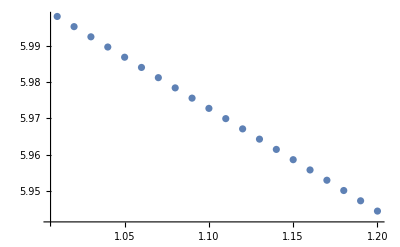

```mathematica
ListPlot[forplot]
```

```mathematica
refval=Table[0.5/((1-x^2)^(3/2))/.x->ii/100,{ii,101,120}]
```

{0.+175.459 ⅈ,0.+61.5741 ⅈ,0.+33.2693 ⅈ,0.+21.4504 ⅈ,0.+15.2365 ⅈ,0.+11.5065 ⅈ,0.+9.06499 ⅈ,0.+7.36614 ⅈ,0.+6.12896 ⅈ,0.+5.19566 ⅈ,0.+4.47154 ⅈ,0.+3.89668 ⅈ,0.+3.43151 ⅈ,0.+3.049 ⅈ,0.+2.73008 ⅈ,0.+2.46099 ⅈ,0.+2.23155 ⅈ,0.+2.03412 ⅈ,0.+1.86283 ⅈ,0.+1.71313 ⅈ}

```mathematica
forplotRef=Table[{(100+ii)/100.,Log[Im[refval[[ii]]]]//N},{ii,1,Length@numRes}]
```

{{1.01,5.16741},{1.02,4.12024},{1.03,3.50464},{1.04,3.06574},{1.05,2.72369},{1.06,2.44291},{1.07,2.20442},{1.08,1.99689},{1.09,1.81303},{1.1,1.64782},{1.11,1.49773},{1.12,1.36012},{1.13,1.233},{1.14,1.11481},{1.15,1.00433},{1.16,0.900563},{1.17,0.802697},{1.18,0.710063},{1.19,0.622097},{1.2,0.538324}}

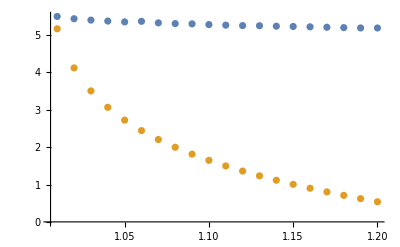

```mathematica
ListPlot[{forplot,forplotRef}]
```

```mathematica
(2^(n-1)√π Gamma[(1-n)/2])/Gamma[n/2]//FunctionExpand//Simplify
```

2^(-1+2 n) Gamma[1-n] Sin[(n π)/2]

```mathematica
Quit[]
```

#### that’s one approach

```mathematica
expandedEik=Series[eikonalFull,{s,0,30}];
expandedEik=expandedEik/.Subscript[y, b][0]->-1/.y1->12/10//Normal;
```

```mathematica
terms=CoefficientList[expandedEik,s];
```

```mathematica
sIntegration=Table[Integrate[terms[[ii]]//Simplify,{σ[1],0,1},{σ[2],0,1}],{ii,Length@terms}];
```

```mathematica
poly=Sum[sIntegration[[i]]*x^(i-1),{i,Length@sIntegration}]
```

(π^3 (465-586 √(2 π)))/(10 √11)+(π^3 (-15345+75401 √(2 π)) x^2)/(660 √11)+(π^3 (230175-6729628 √(2 π)) x^4)/(13200 √11)+(3 π^3 (-59675+10401892 √(2 π)) x^6)/(12320 √11)+(π^3 (8056125-8102291222 √(2 π)) x^8)/(633600 √11)+(7 π^3 (-690525+3901981097 √(2 π)) x^10)/(422400 √11)+(π^3 (48873825-1521787193588 √(2 π)) x^12)/(4659200 √11)+(13 π^3 (-2577960+435989978419 √(2 π)) x^14)/(3440640 √11)+(π^3 (3204726525-2911882325141249 √(2 π)) x^16)/(350945280 √11)+(π^3 (-22551779250+109157865785985253 √(2 π)) x^18)/(2614886400 √11)+(π^3 (24806957175-635326033296949187 √(2 π)) x^20)/(3027763200 √11)+(π^3 (-18861488100+2541875893420990787 √(2 π)) x^22)/(2411724800 √11)-(7 π^3 (-481641571125+339997791997378613611 √(2 π)) x^24)/(449839104000 √11)+(π^3 (-32677528133250+120367727404087546736849 √(2 π)) x^26)/(4534378168320 √11)+(π^3 (1015337481283125-19451930297955046773411419 √(2 π)) x^28)/(146107740979200 √11)+(3 π^3 (-7460850232836000+741330568619062427245322561 √(2 π)) x^30)/(3331928254054400 √11)

```mathematica
poly//N
```

-938.506+2459.81 x^2-11784. x^4+59220.4 x^6-299546. x^8+1.51521×10^6 x^10-7.65385×10^6 x^12+3.86032×10^7 x^14-1.94436×10^8 x^16+9.7824×10^8 x^18-4.9172×10^9 x^20+2.46985×10^10 x^22-1.23982×10^11 x^24+6.22065×10^11 x^26-3.11984×10^12 x^28+1.56416×10^13 x^30

```mathematica
polyVal=Table[{ii,poly/.x->ii//N},{ii,0,1,0.01}]
```

{{0.,-938.506},{0.01,-938.26},{0.02,-937.524},{0.03,-936.301},{0.04,-934.6},{0.05,-932.429},{0.06,-929.8},{0.07,-926.729},{0.08,-923.23},{0.09,-919.324},{0.1,-915.03},{0.11,-910.368},{0.12,-905.363},{0.13,-900.037},{0.14,-894.415},{0.15,-888.52},{0.16,-882.378},{0.17,-876.012},{0.18,-869.447},{0.19,-862.707},{0.2,-855.815},{0.21,-848.793},{0.22,-841.661},{0.23,-834.442},{0.24,-827.153},{0.25,-819.813},{0.26,-812.439},{0.27,-805.047},{0.28,-797.652},{0.29,-790.267},{0.3,-782.904},{0.31,-775.573},{0.32,-768.284},{0.33,-761.04},{0.34,-753.84},{0.35,-746.664},{0.36,-739.462},{0.37,-732.111},{0.38,-724.334},{0.39,-715.539},{0.4,-704.486},{0.41,-688.633},{0.42,-662.873},{0.43,-617.121},{0.44,-531.805},{0.45,-369.53},{0.46,-59.925},{0.47,527.528},{0.48,1631.59},{0.49,3683.29},{0.5,7450.98},{0.51,14287.8},{0.52,26549.},{0.53,48288.9},{0.54,86411.7},{0.55,152554.},{0.56,266134.},{0.57,459248.},{0.58,784459.},{0.59,1.32708×10^6},{0.6,2.22443×10^6},{0.61,3.69563×10^6},{0.62,6.08764×10^6},{0.63,9.94557×10^6},{0.64,1.61195×10^7},{0.65,2.59252×10^7},{0.66,4.1386×10^7},{0.67,6.55907×10^7},{0.68,1.03225×10^8},{0.69,1.61352×10^8},{0.7,2.50552×10^8},{0.71,3.86577×10^8},{0.72,5.92749×10^8},{0.73,9.03395×10^8},{0.74,1.36877×10^9},{0.75,2.06205×10^9},{0.76,3.08925×10^9},{0.77,4.60313×10^9},{0.78,6.82282×10^9},{0.79,1.00611×10^10},{0.8,1.47623×10^10},{0.81,2.15548×10^10},{0.82,3.13235×10^10},{0.83,4.5309×10^10},{0.84,6.52431×10^10},{0.85,9.35338×10^10},{0.86,1.33516×10^11},{0.87,1.89789×10^11},{0.88,2.68673×10^11},{0.89,3.78824×10^11},{0.9,5.32043×10^11},{0.91,7.44378×10^11},{0.92,1.03756×10^12},{0.93,1.44093×10^12},{0.94,1.99396×10^12},{0.95,2.74958×10^12},{0.96,3.77857×10^12},{0.97,5.17524×10^12},{0.98,7.0649×10^12},{0.99,9.61354×10^12},{1.,1.30404×10^13}}

```mathematica
fitfun=ref=Series[β/((1-x^2)^(3/2)),{x,0,30}]//Normal;
```

```mathematica
mdl=NonlinearModelFit[polyVal,fitfun,β,x]
```

FittedModel[1.84831×10^11+2.77246×10^11 x^2+3.46558×10^11 x^4+4.04317×10^11 x^6+4.54857×10^11 x^8+«7»+7.44776×10^11 x^24+7.73422×10^11 x^26+8.01044×10^11 x^28+8.27745×10^11 x^30]

```mathematica
ref=fitfun/.mdl["BestFitParameters"]//Normal
```

1.84831×10^11+2.77246×10^11 x^2+3.46558×10^11 x^4+4.04317×10^11 x^6+4.54857×10^11 x^8+5.00342×10^11 x^10+5.42038×10^11 x^12+5.80755×10^11 x^14+6.17052×10^11 x^16+6.51332×10^11 x^18+6.83899×10^11 x^20+7.14985×10^11 x^22+7.44776×10^11 x^24+7.73422×10^11 x^26+8.01044×10^11 x^28+8.27745×10^11 x^30

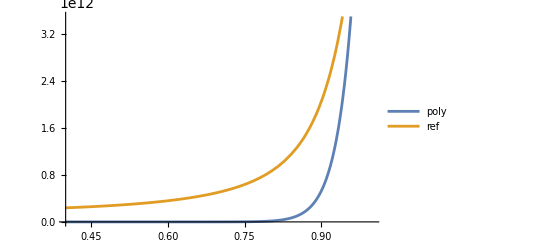

```mathematica
Plot[{poly,ref},{x,0.4,1},PlotLegends->"Expressions"]
```

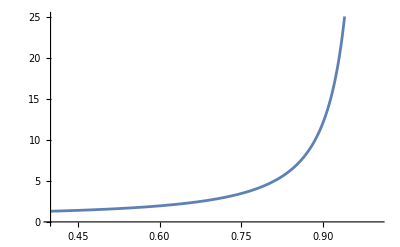

```mathematica
Plot[1/((1-x^2)^(3/2)),{x,0.4,1}]
```

```mathematica
ref=Series[β/((1-x^2)^(3/2)),{x,0,20}]//Normal
```

β+(3 x^2 β)/2+(15 x^4 β)/8+(35 x^6 β)/16+(315 x^8 β)/128+(693 x^10 β)/256+(3003 x^12 β)/1024+(6435 x^14 β)/2048+(109395 x^16 β)/32768+(230945 x^18 β)/65536+(969969 x^20 β)/262144

```mathematica
terms=(8 √2 π^(7/2) y1 Eps[a[0],b[0],v[1],v[2]] √(Subscript[y, 2][0]))/((1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))-(8 √2 π^(7/2) y1^3 Eps[a[0],b[0],v[1],v[2]] √(Subscript[y, 2][0]))/((1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))+(4 √2 π^(7/2) y1 Eps[a[0],b[0],v[1],v[2]] (Subscript[y, 2][0])^(3/2))/((1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))-(6 √2 π^(7/2) y1^3 Eps[a[0],b[0],v[1],v[2]] (Subscript[y, 2][0])^(3/2))/((1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))+(24 √2 π^(7/2) y1 Eps[a[0],b[0],v[1],v[2]] σ[2]^2 (Subscript[y, 2][0])^(3/2))/((1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))-(30 √2 π^(7/2) y1^3 Eps[a[0],b[0],v[1],v[2]] σ[2]^2 (Subscript[y, 2][0])^(3/2))/((1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))+(27 π^(7/2) y1 Eps[a[0],b[0],v[1],v[2]] (Subscript[y, 2][0])^(5/2))/(4 √2 (1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))-(45 π^(7/2) y1^3 Eps[a[0],b[0],v[1],v[2]] (Subscript[y, 2][0])^(5/2))/(4 √2 (1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))+(175 π^(7/2) y1 Eps[a[0],b[0],v[1],v[2]] σ[2]^2 (Subscript[y, 2][0])^(5/2))/(2 √2 (1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))-(285 π^(7/2) y1^3 Eps[a[0],b[0],v[1],v[2]] σ[2]^2 (Subscript[y, 2][0])^(5/2))/(2 √2 (1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))+(495 π^(7/2) y1 Eps[a[0],b[0],v[1],v[2]] σ[2]^4 (Subscript[y, 2][0])^(5/2))/(4 √2 (1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))-(705 π^(7/2) y1^3 Eps[a[0],b[0],v[1],v[2]] σ[2]^4 (Subscript[y, 2][0])^(5/2))/(4 √2 (1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))+(3 π^3)/(2 √(1-y1^2) √(Subscript[y, b][0]))-(√2 π^(7/2))/(√(1-y1^2) √(Subscript[y, b][0]))-(15 π^3 y1^2)/(2 √(1-y1^2) √(Subscript[y, b][0]))+(7 √2 π^(7/2) y1^2)/(√(1-y1^2) √(Subscript[y, b][0]))+(3 √2 π^(7/2))/(√(1-y1^2) (-1+σ[2]) σ[2] √(Subscript[y, b][0]))+(3 √2 π^(7/2) y1^2)/(√(1-y1^2) (σ[2]-σ[2]^2) √(Subscript[y, b][0]))+(3 √2 π^(7/2))/(√(1-y1^2) (σ[2]+σ[2]^2) √(Subscript[y, b][0]))-(3 √2 π^(7/2) y1^2)/(√(1-y1^2) (σ[2]+σ[2]^2) √(Subscript[y, b][0]))+(3 π^3 Subscript[y, 2][0])/(4 √(1-y1^2) √(Subscript[y, b][0]))+(π^(7/2) Subscript[y, 2][0])/(2 √2 √(1-y1^2) √(Subscript[y, b][0]))-(15 π^3 y1^2 Subscript[y, 2][0])/(4 √(1-y1^2) √(Subscript[y, b][0]))+(35 π^(7/2) y1^2 Subscript[y, 2][0])/(2 √2 √(1-y1^2) √(Subscript[y, b][0]))+(4 √2 π^(7/2) Subscript[y, 2][0])/((-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))-(12 √2 π^(7/2) y1^2 Subscript[y, 2][0])/((-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))+(10 √2 π^(7/2) y1^4 Subscript[y, 2][0])/((-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))-(√2 π^(7/2) (Log[1-σ[2]]-Log[-σ[2]]+1/(-1+σ[2])) σ[2] Subscript[y, 2][0])/(√(1-y1^2) √(Subscript[y, b][0]))-(7 √2 π^(7/2) y1^2 (Log[1-σ[2]]-Log[-σ[2]]+1/(-1+σ[2])) σ[2] Subscript[y, 2][0])/(√(1-y1^2) √(Subscript[y, b][0]))+(2 √2 π^(7/2) σ[2] Subscript[y, 2][0])/(√(1-y1^2) (-1+σ[2]) √(Subscript[y, b][0]))+(2 √2 π^(7/2) y1^2 σ[2] Subscript[y, 2][0])/(√(1-y1^2) (-1+σ[2]) √(Subscript[y, b][0]))+(2 √2 π^(7/2) σ[2] Subscript[y, 2][0])/(√(1-y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(2 √2 π^(7/2) y1^2 σ[2] Subscript[y, 2][0])/(√(1-y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(π^(7/2) (2+1/(-1+σ[2])+2 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]) Subscript[y, 2][0])/(√(2-2 y1^2) √(Subscript[y, b][0]))+(7 π^(7/2) y1^2 (2+1/(-1+σ[2])+2 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]) Subscript[y, 2][0])/(√(2-2 y1^2) √(Subscript[y, b][0]))+(√2 π^(7/2) σ[2] (-Log[σ[2]]+Log[1+σ[2]]-1/(1+σ[2])) Subscript[y, 2][0])/(√(1-y1^2) √(Subscript[y, b][0]))+(7 √2 π^(7/2) y1^2 σ[2] (-Log[σ[2]]+Log[1+σ[2]]-1/(1+σ[2])) Subscript[y, 2][0])/(√(1-y1^2) √(Subscript[y, b][0]))+(π^(7/2) (2+2 (Log[σ[2]]-Log[1+σ[2]]) σ[2]-1/(1+σ[2])) Subscript[y, 2][0])/(√(2-2 y1^2) √(Subscript[y, b][0]))+(7 π^(7/2) y1^2 (2+2 (Log[σ[2]]-Log[1+σ[2]]) σ[2]-1/(1+σ[2])) Subscript[y, 2][0])/(√(2-2 y1^2) √(Subscript[y, b][0]))+(9 π^3 (Subscript[y, 2][0])^2)/(16 √(1-y1^2) √(Subscript[y, b][0]))-(7 π^(7/2) (Subscript[y, 2][0])^2)/(2 √2 √(1-y1^2) √(Subscript[y, b][0]))-(45 π^3 y1^2 (Subscript[y, 2][0])^2)/(16 √(1-y1^2) √(Subscript[y, b][0]))+(53 π^(7/2) y1^2 (Subscript[y, 2][0])^2)/(√2 √(1-y1^2) √(Subscript[y, b][0]))+(63 π^(7/2) (Subscript[y, 2][0])^2)/(2 √2 (-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))-(111 π^(7/2) y1^2 (Subscript[y, 2][0])^2)/(√2 (-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))+(207 π^(7/2) y1^4 (Subscript[y, 2][0])^2)/(2 √2 (-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))-(33 π^(7/2) (Log[1-σ[2]]-Log[-σ[2]]+1/(-1+σ[2])) σ[2]^3 (Subscript[y, 2][0])^2)/(8 √(2-2 y1^2) √(Subscript[y, b][0]))-(735 π^(7/2) y1^2 (Log[1-σ[2]]-Log[-σ[2]]+1/(-1+σ[2])) σ[2]^3 (Subscript[y, 2][0])^2)/(8 √(2-2 y1^2) √(Subscript[y, b][0]))+(129 π^(7/2) σ[2]^3 (Subscript[y, 2][0])^2)/(32 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))+(831 π^(7/2) y1^2 σ[2]^3 (Subscript[y, 2][0])^2)/(32 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))+(129 π^(7/2) σ[2]^3 (Subscript[y, 2][0])^2)/(32 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(831 π^(7/2) y1^2 σ[2]^3 (Subscript[y, 2][0])^2)/(32 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(51 π^(7/2) σ[2]^2 (2+1/(-1+σ[2])+2 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]) (Subscript[y, 2][0])^2)/(16 √(2-2 y1^2) √(Subscript[y, b][0]))+(1869 π^(7/2) y1^2 σ[2]^2 (2+1/(-1+σ[2])+2 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]) (Subscript[y, 2][0])^2)/(16 √(2-2 y1^2) √(Subscript[y, b][0]))-(9 π^(7/2) σ[2] (3/2+1/(-1+σ[2])+3 σ[2]+3 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]^2) (Subscript[y, 2][0])^2)/(8 √(2-2 y1^2) √(Subscript[y, b][0]))-(567 π^(7/2) y1^2 σ[2] (3/2+1/(-1+σ[2])+3 σ[2]+3 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]^2) (Subscript[y, 2][0])^2)/(8 √(2-2 y1^2) √(Subscript[y, b][0]))+(9 π^(7/2) (4/3+1/(-1+σ[2])+2 σ[2]+4 σ[2]^2+4 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]^3) (Subscript[y, 2][0])^2)/(32 √(2-2 y1^2) √(Subscript[y, b][0]))+(567 π^(7/2) y1^2 (4/3+1/(-1+σ[2])+2 σ[2]+4 σ[2]^2+4 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]^3) (Subscript[y, 2][0])^2)/(32 √(2-2 y1^2) √(Subscript[y, b][0]))+(33 π^(7/2) σ[2]^3 (-Log[σ[2]]+Log[1+σ[2]]-1/(1+σ[2])) (Subscript[y, 2][0])^2)/(8 √(2-2 y1^2) √(Subscript[y, b][0]))+(735 π^(7/2) y1^2 σ[2]^3 (-Log[σ[2]]+Log[1+σ[2]]-1/(1+σ[2])) (Subscript[y, 2][0])^2)/(8 √(2-2 y1^2) √(Subscript[y, b][0]))+(51 π^(7/2) σ[2]^2 (2+2 (Log[σ[2]]-Log[1+σ[2]]) σ[2]-1/(1+σ[2])) (Subscript[y, 2][0])^2)/(16 √(2-2 y1^2) √(Subscript[y, b][0]))+(1869 π^(7/2) y1^2 σ[2]^2 (2+2 (Log[σ[2]]-Log[1+σ[2]]) σ[2]-1/(1+σ[2])) (Subscript[y, 2][0])^2)/(16 √(2-2 y1^2) √(Subscript[y, b][0]))-(9 π^(7/2) σ[2] (-1+3 σ[2]+6 σ[2]^2+6 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^2 (1+σ[2])) (Subscript[y, 2][0])^2)/(16 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))-(567 π^(7/2) y1^2 σ[2] (-1+3 σ[2]+6 σ[2]^2+6 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^2 (1+σ[2])) (Subscript[y, 2][0])^2)/(16 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(3 π^(7/2) (1+12 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^3 (1+σ[2])+2 σ[2] (-1+3 σ[2]+6 σ[2]^2)) (Subscript[y, 2][0])^2)/(32 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(189 π^(7/2) y1^2 (1+12 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^3 (1+σ[2])+2 σ[2] (-1+3 σ[2]+6 σ[2]^2)) (Subscript[y, 2][0])^2)/(32 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(15 π^3 (Subscript[y, 2][0])^3)/(32 √(1-y1^2) √(Subscript[y, b][0]))-(715 π^(7/2) (Subscript[y, 2][0])^3)/(32 √2 √(1-y1^2) √(Subscript[y, b][0]))-(75 π^3 y1^2 (Subscript[y, 2][0])^3)/(32 √(1-y1^2) √(Subscript[y, b][0]))+(6115 π^(7/2) y1^2 (Subscript[y, 2][0])^3)/(32 √2 √(1-y1^2) √(Subscript[y, b][0]))+(585 π^(7/2) (Subscript[y, 2][0])^3)/(4 √2 (-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))-(1095 π^(7/2) y1^2 (Subscript[y, 2][0])^3)/(2 √2 (-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))+(2115 π^(7/2) y1^4 (Subscript[y, 2][0])^3)/(4 √2 (-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))-(3585 π^(7/2) (Log[1-σ[2]]-Log[-σ[2]]+1/(-1+σ[2])) σ[2]^5 (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) √(Subscript[y, b][0]))-(190335 π^(7/2) y1^2 (Log[1-σ[2]]-Log[-σ[2]]+1/(-1+σ[2])) σ[2]^5 (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) √(Subscript[y, b][0]))+(4635 π^(7/2) σ[2]^5 (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))+(85605 π^(7/2) y1^2 σ[2]^5 (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))+(4635 π^(7/2) σ[2]^5 (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(85605 π^(7/2) y1^2 σ[2]^5 (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(7365 π^(7/2) σ[2]^4 (2+1/(-1+σ[2])+2 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) √(Subscript[y, b][0]))+(716475 π^(7/2) y1^2 σ[2]^4 (2+1/(-1+σ[2])+2 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) √(Subscript[y, b][0]))-(1095 π^(7/2) σ[2]^3 (-1-3 σ[2]+6 σ[2]^2+6 (Log[1-σ[2]]-Log[-σ[2]]) (-1+σ[2]) σ[2]^2) (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))-(188985 π^(7/2) y1^2 σ[2]^3 (-1-3 σ[2]+6 σ[2]^2+6 (Log[1-σ[2]]-Log[-σ[2]]) (-1+σ[2]) σ[2]^2) (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))+(476235 π^(7/2) y1^2 σ[2]^2 (4/3+1/(-1+σ[2])+2 σ[2]+4 σ[2]^2+4 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]^3) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) √(Subscript[y, b][0]))+(75 π^(7/2) (6/5+1/(-1+σ[2])+(3 σ[2])/2+2 σ[2]^2+3 σ[2]^3+6 σ[2]^4+6 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]^5) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) √(Subscript[y, b][0]))+(28725 π^(7/2) y1^2 (6/5+1/(-1+σ[2])+(3 σ[2])/2+2 σ[2]^2+3 σ[2]^3+6 σ[2]^4+6 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]^5) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) √(Subscript[y, b][0]))+(3585 π^(7/2) σ[2]^5 (-Log[σ[2]]+Log[1+σ[2]]-1/(1+σ[2])) (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) √(Subscript[y, b][0]))+(190335 π^(7/2) y1^2 σ[2]^5 (-Log[σ[2]]+Log[1+σ[2]]-1/(1+σ[2])) (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) √(Subscript[y, b][0]))+(7365 π^(7/2) σ[2]^4 (2+2 (Log[σ[2]]-Log[1+σ[2]]) σ[2]-1/(1+σ[2])) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) √(Subscript[y, b][0]))+(716475 π^(7/2) y1^2 σ[2]^4 (2+2 (Log[σ[2]]-Log[1+σ[2]]) σ[2]-1/(1+σ[2])) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) √(Subscript[y, b][0]))-(1095 π^(7/2) σ[2]^3 (-1+3 σ[2]+6 σ[2]^2+6 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^2 (1+σ[2])) (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))-(188985 π^(7/2) y1^2 σ[2]^3 (-1+3 σ[2]+6 σ[2]^2+6 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^2 (1+σ[2])) (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(615 π^(7/2) σ[2]^2 (-1+12 (Log[1-σ[2]]-Log[-σ[2]]) (-1+σ[2]) σ[2]^3+2 σ[2] (-1-3 σ[2]+6 σ[2]^2)) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))+(86175 π^(7/2) y1^2 σ[2] (5/4+5 (-Log[σ[2]]+Log[1+σ[2]]) σ[2]^4-1/(1+σ[2])-5/6 σ[2] (2-3 σ[2]+6 σ[2]^2)) (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) √(Subscript[y, b][0]))+(615 π^(7/2) σ[2]^2 (1+12 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^3 (1+σ[2])+2 σ[2] (-1+3 σ[2]+6 σ[2]^2)) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(158745 π^(7/2) y1^2 σ[2]^2 (1+12 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^3 (1+σ[2])+2 σ[2] (-1+3 σ[2]+6 σ[2]^2)) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))-(75 π^(7/2) σ[2] (-3+60 (Log[1-σ[2]]-Log[-σ[2]]) (-1+σ[2]) σ[2]^4+5 σ[2] (-1+2 σ[2] (-1-3 σ[2]+6 σ[2]^2))) (Subscript[y, 2][0])^3)/(2048 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))-(28725 π^(7/2) y1^2 σ[2] (-3+60 (Log[1-σ[2]]-Log[-σ[2]]) (-1+σ[2]) σ[2]^4+5 σ[2] (-1+2 σ[2] (-1-3 σ[2]+6 σ[2]^2))) (Subscript[y, 2][0])^3)/(2048 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))-(75 π^(7/2) σ[2] (-3+60 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^4 (1+σ[2])+5 σ[2] (1+2 σ[2] (-1+3 σ[2]+6 σ[2]^2))) (Subscript[y, 2][0])^3)/(2048 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(15 π^(7/2) (2+60 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^5 (1+σ[2])+σ[2] (-3+5 σ[2] (1+2 σ[2] (-1+3 σ[2]+6 σ[2]^2)))) (Subscript[y, 2][0])^3)/(2048 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(5745 π^(7/2) y1^2 (2+60 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^5 (1+σ[2])+σ[2] (-3+5 σ[2] (1+2 σ[2] (-1+3 σ[2]+6 σ[2]^2)))) (Subscript[y, 2][0])^3)/(2048 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]));
```

```mathematica
Integrate[#,{σ[2],0,1}]&/@terms
```

Integrate::idiv: Integral of (3 √2 π^(7/2))/(√(1-y1^2) (-1+σ[2]) σ[2] √y_b[0]) does not converge on {0,1}.

Integrate::idiv: Integral of (3 √2 π^(7/2) y1^2)/(√(1-y1^2) (σ[2]-σ[2]^2) √y_b[0]) does not converge on {0,1}.

Integrate::idiv: Integral of (3 √2 π^(7/2))/(√(1-y1^2) (σ[2]+σ[2]^2) √y_b[0]) does not converge on {0,1}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

$Aborted

```mathematica
Integrate[Coefficient[expandedEik,s,0],{σ[1],0,1}]
```

ConditionalExpression[-1/(1024 (1-y1^2)^(3/2) (-1+σ[2]^2) y_b[0]^(3/2))π^3 (128 √(2 π) y1 Eps[a[0],b[0],v[1],v[2]] (-1+σ[2]^2) √y_2[0] (-64-32 (1+6 σ[2]^2) y_2[0]-(27+350 σ[2]^2+495 σ[2]^4) y_2[0]^2+y1^2 (64+48 (1+5 σ[2]^2) y_2[0]+15 (3+38 σ[2]^2+47 σ[2]^4) y_2[0]^2))+(1536-7168 √(2 π)+768 y_2[0]-2816 √(2 π) y_2[0]+576 y_2[0]^2-17824 √(2 π) y_2[0]^2+480 y_2[0]^3-86305 √(2 π) y_2[0]^3-4635 √(2 π) σ[2]^6 y_2[0]^3+3 √(2 π) σ[2]^4 y_2[0]^2 (-1376+775 y_2[0])+σ[2]^2 (512 (-3+2 √(2 π))-256 (3+√(2 π)) y_2[0]+64 (-9+307 √(2 π)) y_2[0]^2+5 (-96+17339 √(2 π)) y_2[0]^3)-2 y1^2 (-512 (-9+20 √(2 π))-256 (-9+53 √(2 π)) y_2[0]-32 (-54+1433 √(2 π)) y_2[0]^2+3 √(2 π) σ[2]^4 (3744-2105 y_2[0]) y_2[0]^2-5 (-288+39533 √(2 π)) y_2[0]^3+40485 √(2 π) σ[2]^6 y_2[0]^3+σ[2]^2 (512 (-9+8 √(2 π))+256 (-9+41 √(2 π)) y_2[0]+64 (-27+505 √(2 π)) y_2[0]^2+5 (-288+32315 √(2 π)) y_2[0]^3))+y1^4 (512 (15-26 √(2 π))-256 (-15+103 √(2 π)) y_2[0]-32 (-90+2693 √(2 π)) y_2[0]^2-5 (-480+74861 √(2 π)) y_2[0]^3+85605 √(2 π) σ[2]^6 y_2[0]^3-3 √(2 π) σ[2]^4 y_2[0]^2 (-8864+4985 y_2[0])+σ[2]^2 (512 (-15+14 √(2 π))+256 (-15+91 √(2 π)) y_2[0]+320 (-9+179 √(2 π)) y_2[0]^2+5 (-480+60347 √(2 π)) y_2[0]^3))) y_b[0]), 1+Re[σ[2]]<0||Re[σ[2]]>1||σ[2]∉ℝ]

```mathematica
Integrate[Integrate[%292,{σ[1],0,1}],{σ[2],0,1}]
```

Undefined

```mathematica
Integrate[Coefficient[%292,Subscript[y, 2][0],0],{σ[1],0,1}]
```

ConditionalExpression[(π^3 (-615+926 √(2 π)+(615-194 √(2 π)) σ[2]^2))/(10 √61 (-1+σ[2]^2)), Re[σ[2]]<-1||Re[σ[2]]>1||σ[2]∉ℝ]

```mathematica
Integrate[(π^3 (-615+926 √(2 π)+(615-194 √(2 π)) σ[2]^2))/(10 √61 (-1+σ[2]^2)),σ[2]]//TrigExpand
```

-6/5 √122 π^(7/2) ArcTanh[σ[2]]+(123 π^3 σ[2])/(2 √61)-97/5 √(2/61) π^(7/2) σ[2]

```mathematica
%265//Expand
```

(6 √2 π^(7/2) σ[1]^2)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])-(6 √2 π^(7/2) y1^2 σ[1]^2)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])+(3 π^3 σ[1]^4)/(2 √(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])-(√2 π^(7/2) σ[1]^4)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])-(15 π^3 y1^2 σ[1]^4)/(2 √(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])+(7 √2 π^(7/2) y1^2 σ[1]^4)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])+(6 √2 π^(7/2) σ[2]^2)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])-(6 √2 π^(7/2) y1^2 σ[2]^2)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])-(3 π^3 σ[1]^2 σ[2]^2)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])+(2 √2 π^(7/2) σ[1]^2 σ[2]^2)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])+(15 π^3 y1^2 σ[1]^2 σ[2]^2)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])-(14 √2 π^(7/2) y1^2 σ[1]^2 σ[2]^2)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])+(3 π^3 σ[2]^4)/(2 √(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])-(√2 π^(7/2) σ[2]^4)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])-(15 π^3 y1^2 σ[2]^4)/(2 √(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])+(7 √2 π^(7/2) y1^2 σ[2]^4)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])

```mathematica
Integrate[%265,{σ[1],0,1}]
```

ConditionalExpression[(π^3 (3+√(2 π) (-2+12/(-1+σ[2]^2))+y1^2 (-15+√(2 π) (14-12/(-1+σ[2]^2)))))/(2 √(1-y1^2) √y_b[0]), Re[σ[2]]>1||Re[σ[2]]<-1||σ[2]∉ℝ]

```mathematica
Integrate[(π^3 (3+√(2 π) (-2+12/(-1+σ[2]^2))+y1^2 (-15+√(2 π) (14-12/(-1+σ[2]^2)))))/(2 √(1-y1^2) √(Subscript[y, b][0])),{σ[2],0,1}]
```

(π^3 (3-2 √(2 π) (1+Log[64])+y1^2 (-15+2 √(2 π) (7+Log[64]))))/(2 √(1-y1^2) √y_b[0])

```mathematica
(π^3 (3-2 √(2 π) (1+Log[64])+y1^2 (-15+2 √(2 π) (7+Log[64]))))/(2 √(1-y1^2) √(Subscript[y, b][0]))
```

(π^3 (3-2 √(2 π) (1+Log[64])+y1^2 (-15+2 √(2 π) (7+Log[64]))))/(2 √(1-y1^2) √y_b[0])

```mathematica
FourierTransform[(x^2)^(-n/2),x,s,Assumptions->{n>0},FourierParameters->{-1, 1}]/.s->1
```

(Gamma[1-n] Sin[(n π)/2])/π

#### another test

```mathematica
xpnd=eikonalFull/.dot[a[0],a[0]]->-s^2/.dot[b[0],b[0]]-> -nb^2/.y1->12/10;
```

```mathematica
expand=Series[xpnd,{s,0,30}]//Normal;
```

```mathematica
Integrate[expand/.s->1,{σ[1],0,1},{σ[2],0,1}]
```

1/(96907583922534088704000 √11 √-nb nb^(61/2))ⅈ (74323758219929547500743275420746595+3968 nb^2 (3768004601239977579992459676165+758574806809918530441698723525 nb^2+696 nb^4 (219622844069093818201787841+5 nb^2 (8861106910669456415663691+368 nb^2 (4864442545020330396228+984467343590648152521 nb^2+152 nb^4 (1313794008041470670+17 nb^2 (15724339289297925+3212711139966768 nb^2+1664 nb^4 (396809089908+82288817401 nb^2+48 nb^4 (361087455+78738149 nb^2+19123160 nb^4+7271880 nb^6))))))))) π^3

```mathematica
%294//Expand//PowerExpand//N
```

(7.17007×10^12)/nb^31+(1.44238×10^12)/nb^29+(2.90379×10^11)/nb^27+(5.85132×10^10)/nb^25+(1.18041×10^10)/nb^23+(2.38466×10^9)/nb^21+(4.82609×10^8)/nb^19+(9.7896×10^7)/nb^17+(1.99186×10^7)/nb^15+(4.06966×10^6)/nb^13+836415./nb^11+173453./nb^9+36533.7/nb^7+7966.48/nb^5+1934.82/nb^3+735.746/nb

```mathematica
eikonVals=Table[{ii/100,%295/.{nb->ii/100}},{ii,101,120}]//N
```

{{1.01,6.62722×10^12},{1.02,4.90826×10^12},{1.03,3.64629×10^12},{1.04,2.71693×10^12},{1.05,2.03041×10^12},{1.06,1.52177×10^12},{1.07,1.14379×10^12},{1.08,8.62094×10^11},{1.09,6.51562×10^11},{1.1,4.93773×10^11},{1.11,3.75188×10^11},{1.12,2.85827×10^11},{1.13,2.18308×10^11},{1.14,1.67159×10^11},{1.15,1.28312×10^11},{1.16,9.87331×10^10},{1.17,7.61555×10^10},{1.18,5.88798×10^10},{1.19,4.5629×10^10},{1.2,3.54414×10^10}}

```mathematica
refVals=Table[{ii/100,Im[11.8^10/((1-x^2)^(3/2))]/.x->ii/100},{ii,101,120}]//N
```

{{1.01,1.83665×10^13},{1.02,6.44537×10^12},{1.03,3.48252×10^12},{1.04,2.24535×10^12},{1.05,1.5949×10^12},{1.06,1.20446×10^12},{1.07,9.48894×10^11},{1.08,7.71063×10^11},{1.09,6.41559×10^11},{1.1,5.43865×10^11},{1.11,4.68066×10^11},{1.12,4.07891×10^11},{1.13,3.59199×10^11},{1.14,3.19159×10^11},{1.15,2.85776×10^11},{1.16,2.57608×10^11},{1.17,2.33592×10^11},{1.18,2.12925×10^11},{1.19,1.94995×10^11},{1.2,1.79325×10^11}}

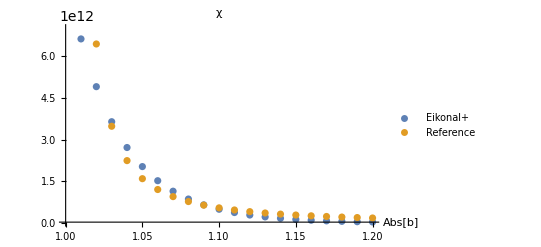

```mathematica
ListPlot[{eikonVals,refVals},PlotRange->{{1,1.2},{3*10^10,7*10^12}},AxesLabel->{Abs[b]},PlotLabel->"χ",PlotLegends->{"Eikonal+","Reference"}]
```

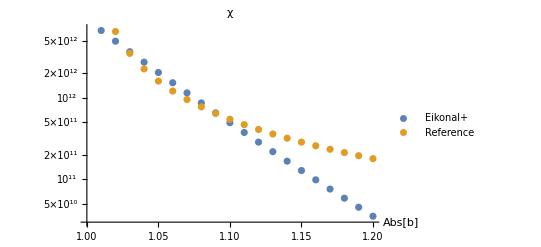

```mathematica
ListLogPlot[{eikonVals,refVals},PlotRange->{{1,1.2},{3*10^10,7*10^12}},AxesLabel->{Abs[b]},PlotLabel->"χ",PlotLegends->{"Eikonal+","Reference"}]
```

```mathematica
(30.54-29.52)/((30.54+29.52)/2)
```

0.033966

```mathematica
Series[1/((y^2-x^2)^(3/2)),{y,0,30}]//Normal//PowerExpand
```

ⅈ/x^3+(3 ⅈ y^2)/(2 x^5)+(15 ⅈ y^4)/(8 x^7)+(35 ⅈ y^6)/(16 x^9)+(315 ⅈ y^8)/(128 x^11)+(693 ⅈ y^10)/(256 x^13)+(3003 ⅈ y^12)/(1024 x^15)+(6435 ⅈ y^14)/(2048 x^17)+(109395 ⅈ y^16)/(32768 x^19)+(230945 ⅈ y^18)/(65536 x^21)+(969969 ⅈ y^20)/(262144 x^23)+(2028117 ⅈ y^22)/(524288 x^25)+(16900975 ⅈ y^24)/(4194304 x^27)+(35102025 ⅈ y^26)/(8388608 x^29)+(145422675 ⅈ y^28)/(33554432 x^31)+(300540195 ⅈ y^30)/(67108864 x^33)

```mathematica
%329/.y->1
```

1/((1-x^2)^(3/2))

```mathematica
Series[1/((1-x^2)^(3/2)),{x,1,0}]
```

(-1+x)^(3/2)/(2 √2 (1-x)^(3/2) (x-1)^(3/2))+√O[x-1]

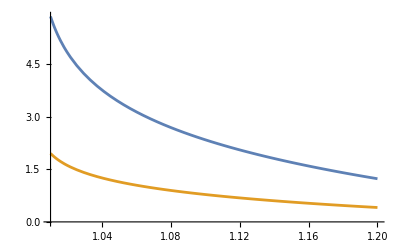

```mathematica
Plot[{Log[Im[1/((1-x^2)^(3/2))]],Log[-Im[1/((1-x^2)^(1/2))]]},{x,1.01,1.2}]
```

```mathematica
test=Series[xpnd,{s,1,0}]//Normal
```

(93 ⅈ π^3)/(2 √11 √(1-nb^2))+1/5 ⅈ √11 √(1-nb^2) π^3+(2 ⅈ (183+11 nb^2) π^2 EllipticK[-4/(1-nb^2)])/(5 √11 √(1-nb^2))+(250 ⅈ (1604/625+(121 nb^2)/625) π^2 ((-1+nb^2) EllipticE[-4/(1-nb^2)]-(-5+nb^2) EllipticK[-4/(1-nb^2)]))/(11 √11 √(1-nb^2) (-5+nb^2))-(60 ⅈ π^2 (1-σ[2]) (-47/25 EllipticK[-(-1+σ[2])^2/(-nb^2+σ[2]^2)] (1-nb^2+2 (-1+σ[2]) σ[2])-1/25 EllipticE[-(-1+σ[2])^2/(-nb^2+σ[2]^2)] (25+69 nb^2-50 σ[2]-44 σ[2]^2)))/(11 (1-nb^2+2 (-1+σ[2]) σ[2])^2 √(-nb^2+σ[2]^2))-(60 ⅈ π^2 (-1+σ[2]) (-47/25 EllipticK[-(-1+σ[2])^2/(-nb^2+σ[2]^2)] (1-nb^2+2 (-1+σ[2]) σ[2])-1/25 EllipticE[-(-1+σ[2])^2/(-nb^2+σ[2]^2)] (25+69 nb^2-50 σ[2]-44 σ[2]^2)))/(11 (1-nb^2+2 (-1+σ[2]) σ[2])^2 √(-nb^2+σ[2]^2))-(60 ⅈ π^2 (-1-σ[2]) (-1/25 EllipticE[-(1+σ[2])^2/(-nb^2+σ[2]^2)] (25+69 nb^2+50 σ[2]-44 σ[2]^2)+47/25 EllipticK[-(1+σ[2])^2/(-nb^2+σ[2]^2)] (-1+nb^2-2 σ[2] (1+σ[2]))))/(11 √(-nb^2+σ[2]^2) (1-nb^2+2 σ[2] (1+σ[2]))^2)-(60 ⅈ π^2 (1+σ[2]) (-1/25 EllipticE[-(1+σ[2])^2/(-nb^2+σ[2]^2)] (25+69 nb^2+50 σ[2]-44 σ[2]^2)+47/25 EllipticK[-(1+σ[2])^2/(-nb^2+σ[2]^2)] (-1+nb^2-2 σ[2] (1+σ[2]))))/(11 (-nb^2+σ[2]^2)^(5/2) (1+(1+σ[2])^2/(-nb^2+σ[2]^2))^2)+(20 ⅈ nb^2 π^2 (-1+σ[2]^2/nb^2) (1/25 EllipticE[-(σ[1]-σ[2])^2/(-nb^2+σ[2]^2)] (-nb^2+σ[2]^2) (-143 nb^4+286 nb^2 σ[1]^2-287 σ[1]^4-572 nb^2 σ[1] σ[2]+1148 σ[1]^3 σ[2]+572 nb^2 σ[2]^2-2008 σ[1]^2 σ[2]^2+1720 σ[1] σ[2]^3-716 σ[2]^4)-(-nb^2+σ[1]^2-2 σ[1] σ[2]+2 σ[2]^2) (-66/25 π (-nb^2+σ[2]^2) (-nb^2+σ[1]^2-2 σ[1] σ[2]+2 σ[2]^2)+1/25 EllipticK[-(σ[1]-σ[2])^2/(-nb^2+σ[2]^2)] (-11 nb^4+33 nb^2 σ[1]^2-94 σ[1]^4-66 nb^2 σ[1] σ[2]+376 σ[1]^3 σ[2]+55 nb^2 σ[2]^2-597 σ[1]^2 σ[2]^2+442 σ[1] σ[2]^3-138 σ[2]^4))))/(√11 (σ[1]-σ[2])^2 (-nb^2+σ[2]^2)^(7/2) (1+(σ[1]-σ[2])^2/(-nb^2+σ[2]^2))^2)+(10 ⅈ nb^2 π^2 (-1+σ[2]^2/nb^2) (-((-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2) (-66/25 π (-nb^2+σ[2]^2) (-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2)+1/25 EllipticK[-(σ[1]+σ[2])^2/(-nb^2+σ[2]^2)] (-11 nb^4+33 nb^2 σ[1]^2-94 σ[1]^4+66 nb^2 σ[1] σ[2]-376 σ[1]^3 σ[2]+55 nb^2 σ[2]^2-597 σ[1]^2 σ[2]^2-442 σ[1] σ[2]^3-138 σ[2]^4)))+EllipticE[-(σ[1]+σ[2])^2/(-nb^2+σ[2]^2)] (-nb^2+σ[2]^2) (13 (-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2)^2-36/25 (17 (σ[1]+σ[2])^4-26 (σ[1]+σ[2])^2 (nb^2-σ[2]^2)+13 (-nb^2+σ[2]^2)^2))))/(√11 (σ[1]+σ[2])^2 (-nb^2+σ[2]^2)^(3/2) (-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2)^2)+(10 ⅈ nb^2 π^2 (-1+σ[2]^2/nb^2) (-((-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2) (-66/25 π (-nb^2+σ[2]^2) (-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2)+1/25 EllipticK[-(σ[1]+σ[2])^2/(-nb^2+σ[2]^2)] (-11 nb^4+33 nb^2 σ[1]^2-94 σ[1]^4+66 nb^2 σ[1] σ[2]-376 σ[1]^3 σ[2]+55 nb^2 σ[2]^2-597 σ[1]^2 σ[2]^2-442 σ[1] σ[2]^3-138 σ[2]^4)))+EllipticE[-(σ[1]+σ[2])^2/(-nb^2+σ[2]^2)] (-nb^2+σ[2]^2) (13 (-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2)^2-36/25 (17 (σ[1]+σ[2])^4-26 (σ[1]+σ[2])^2 (nb^2-σ[2]^2)+13 (-nb^2+σ[2]^2)^2))))/(√11 (σ[1]+σ[2])^2 (-nb^2+σ[2]^2)^(7/2) (1+(σ[1]+σ[2])^2/(-nb^2+σ[2]^2))^2)

```mathematica
Series[test,{nb,1,0}]//Normal//FunctionExpand//Expand
```

```mathematica
NIntegrate[%513[[10]]//Simplify,{σ[1],0,1},{σ[2],0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumri: The integrand (52 ⅈ √11 π^2 EllipticE[-(σ[1]+σ[2])^2/(-1+σ[2]^2)] σ[1]^2)/(5 (σ[1]-σ[2])^2 (σ[1]+σ[2])^2 √(-1+σ[2]^2) (-1+σ[1]^2-2 σ[1] σ[2]+2 σ[2]^2)^2 (-1+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2)^2) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,3.97545×10^-31},{0.875,0.9375}}.

NIntegrate[Simplify[%513⟦10⟧],{σ[1],0,1},{σ[2],0,1}]

```mathematica
Table[prep=%338/.{nb->jj/100};res=NIntegrate[prep,{σ[1],0,1},{σ[2],0,1},WorkingPrecision->10],{jj,101,120}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in σ[2] near {σ[1],σ[2]} = {0.8248853797,0.1706117406}. NIntegrate obtained 107287.7876-180.2769105 ⅈ and 37185.90961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in σ[1] near {σ[1],σ[2]} = {0.838614822859194968576999133355587565657663590971633974974219,0.167539125421154874307996533422350262630654363886535899896877}. NIntegrate obtained 15285.787650709900274819970225528465627468827268522501016961-169.129970667596770521005222465296574094806819808176955164316 ⅈ and 961001.36272182986890489691267017153122076817352781048869752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in σ[2] near {σ[1],σ[2]} = {0.00104612956395250033665929961902964698692054118479267805911055,0.727824570173648093576999133355587565657663590971633974974219}. NIntegrate obtained 231404.793094017484211581435769047484198468924361701955066375-163.25613755174087354073345548978970897679980139273332901887 ⅈ and 369472.004248987939760136165151791766222194824034247947617995 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{107287.7876-180.2769105 ⅈ,15285.78765-169.12997 ⅈ,231404.7931-163.256 ⅈ,124889.3222-159.9483194 ⅈ,123706.0996-157.2525511 ⅈ,66977.7312-163.1141 ⅈ,176171.7813-154.7894794 ⅈ,66874.79428-153.8220024 ⅈ,666193.6588-153.9889826 ⅈ,2.548421989×10^6-151.4812778 ⅈ,234951.9703-149.4757193 ⅈ,183943.5567-148.7006839 ⅈ,210854.4808-149.958 ⅈ,186794.3155-148.3085 ⅈ,-1.464340581×10^6-148.1292487 ⅈ,290644.8946-147.52 ⅈ,106526.9201-146.4337482 ⅈ,139336.5624-145.7136404 ⅈ,-6.931394948×10^7-145.281749 ⅈ,136757.5035-146.766 ⅈ}

(93 ⅈ π^3)/(2 √11 √(1-nb^2))

#### yet another test

```mathematica
xpnd2=eikonalFull/.dot[a[0],a[0]]->-s^2/.dot[b[0],b[0]]-> -nb^2;
```

```mathematica
Series[xpnd2,{s,0,0}]//Normal//Simplify//Factor
```

-(3 π^3 (-1+5 y1^2))/(√(-nb^2) √(1-y1^2))

## Other stuff

```mathematica
FourPoint=m[1]^2/s[1,2]*((FV[v[1],Subscript[μ, 1]]F[1,Subscript[μ, 1],Subscript[μ, 2]]F[2,Subscript[μ, 2],Subscript[μ, 3]]FV[v[1],Subscript[μ, 3]])/Contract[FV[v[1],μ]FV[l[1],μ]])^2//Expand;
FourPoint//TraditionalForm
```

((m(1))^2 (OverBar[eps(1)]^μ_2)^2 (OverBar[eps(2)]^μ_3)^2 (OverBar[l(1)]^μ_1)^2 (OverBar[l(2)]^μ_2)^2 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)+((m(1))^2 (OverBar[eps(1)]^μ_1)^2 (OverBar[eps(2)]^μ_3)^2 (OverBar[l(1)]^μ_2)^2 (OverBar[l(2)]^μ_2)^2 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)-(2 (m(1))^2 OverBar[eps(1)]^μ_1 OverBar[eps(1)]^μ_2 (OverBar[eps(2)]^μ_3)^2 OverBar[l(1)]^μ_1 OverBar[l(1)]^μ_2 (OverBar[l(2)]^μ_2)^2 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)+((m(1))^2 (OverBar[eps(1)]^μ_2)^2 (OverBar[eps(2)]^μ_2)^2 (OverBar[l(1)]^μ_1)^2 (OverBar[l(2)]^μ_3)^2 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)+((m(1))^2 (OverBar[eps(1)]^μ_1)^2 (OverBar[eps(2)]^μ_2)^2 (OverBar[l(1)]^μ_2)^2 (OverBar[l(2)]^μ_3)^2 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)-(2 (m(1))^2 OverBar[eps(1)]^μ_1 OverBar[eps(1)]^μ_2 (OverBar[eps(2)]^μ_2)^2 OverBar[l(1)]^μ_1 OverBar[l(1)]^μ_2 (OverBar[l(2)]^μ_3)^2 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)-(2 (m(1))^2 (OverBar[eps(1)]^μ_2)^2 OverBar[eps(2)]^μ_2 OverBar[eps(2)]^μ_3 (OverBar[l(1)]^μ_1)^2 OverBar[l(2)]^μ_2 OverBar[l(2)]^μ_3 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)-(2 (m(1))^2 (OverBar[eps(1)]^μ_1)^2 OverBar[eps(2)]^μ_2 OverBar[eps(2)]^μ_3 (OverBar[l(1)]^μ_2)^2 OverBar[l(2)]^μ_2 OverBar[l(2)]^μ_3 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)+(4 (m(1))^2 OverBar[eps(1)]^μ_1 OverBar[eps(1)]^μ_2 OverBar[eps(2)]^μ_2 OverBar[eps(2)]^μ_3 OverBar[l(1)]^μ_1 OverBar[l(1)]^μ_2 OverBar[l(2)]^μ_2 OverBar[l(2)]^μ_3 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
Clear[FPKin]
FPKin[σ_,ξ_]:=FV[v[1],μ]FV[v[1],ρ](FV[l[1],μ]KD[ν,σ]-FV[l[1],ν]KD[μ,σ])(FV[l[2],ν]KD[ρ,ξ]-FV[l[2],ρ]KD[ν,ξ])/.KD->MT//Contract;
```

```mathematica
Pair[Momentum[l[1]],Momentum[l[1]]]=0;
Pair[Momentum[l[2]],Momentum[l[2]]]=0;
Pair[Momentum[Polarization[l[1],I]],Momentum[l[1]]]=0;
Pair[Momentum[Polarization[l[2],I]],Momentum[l[2]]]=0;
Pair[Momentum[v[1]],Momentum[v[1]]]=1;
Pair[Momentum[v[2]],Momentum[v[2]]]=1;
Contract[FPKin[Subscript[μ, 1],Subscript[ν, 1]]PolarizationVector[l[2],Subscript[ν, 1]]]Contract[FPKin[Subscript[μ, 2],Subscript[ν, 2]]PolarizationVector[l[2],Subscript[ν, 2]]]//TraditionalForm
```

(OverBar[v(1)]^μ_1 (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)])-(ε̄)^μ_1(l(2)) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-(OverBar[l(1)]·OverBar[l(2)]) OverBar[v(1)]^μ_1 (ε̄(l(2))·OverBar[v(1)])+OverBar[l(2)]^μ_1 (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])) (OverBar[v(1)]^μ_2 (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)])-(ε̄)^μ_2(l(2)) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-(OverBar[l(1)]·OverBar[l(2)]) OverBar[v(1)]^μ_2 (ε̄(l(2))·OverBar[v(1)])+OverBar[l(2)]^μ_2 (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]))

```mathematica
%338*FourVector[v[2],Subscript[α, 1]]FourVector[v[2],Subscript[α, 2]]*(1/2*(MT[Subscript[α, 1],Subscript[μ, 1]]MT[Subscript[α, 2],Subscript[μ, 2]]+MT[Subscript[α, 1],Subscript[μ, 2]]MT[Subscript[α, 2],Subscript[μ, 1]]-2/(d-2)MT[Subscript[α, 1],Subscript[α, 2]]MT[Subscript[μ, 1],Subscript[μ, 2]]))//Contract//TraditionalForm
```

1/2 (-(2 (ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)/(d-2)+((OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)])-(OverBar[l(1)]·OverBar[l(2)]) (ε̄(l(2))·OverBar[v(1)])) (2 (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)])^2 (ε̄(l(2))·OverBar[v(1)])-(2 (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+(2 (OverBar[l(1)]·OverBar[l(2)]) (ε̄(l(2))·OverBar[v(1)]))/(d-2)+2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (ε̄(l(2))·OverBar[v(1)])-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]))+2 (OverBar[l(2)]·OverBar[v(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(1)])^2+2 (OverBar[l(2)]·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(2)])^2-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)])^2+2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])+2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]))

```mathematica
%339/.Momentum[Polarization[l[2],ⅈ]]->Momentum[l[2]]
```

0

```mathematica
Collect[%339,Pair[Momentum[Polarization[l[2],I]],_]]//TraditionalForm
```

1/2 (OverBar[l(1)]·ε̄(l(2)))^2 (2 (OverBar[v(1)]·OverBar[v(2)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-(2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2))+(OverBar[l(1)]·ε̄(l(2))) (1/2 (ε̄(l(2))·OverBar[v(1)]) (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)])^2)-((ε̄(l(2)))^2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)])) (ε̄(l(2))·OverBar[v(1)])^2+(OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(2)])^2+1/2 (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
Uncontract[%346,Polarization[l[2],I],Pair->All,CartesianPair->All]//TraditionalForm
```

-((ḡ)^($AL($493)$AL($494)) (ε̄)^($AL($493))(l(2)) (ε̄)^($AL($494))(l(2)) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 OverBar[l(1)]^($AL($499)) OverBar[v(1)]^($AL($500)) (ε̄)^($AL($499))(l(2)) (ε̄)^($AL($500))(l(2)) (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 OverBar[l(1)]^($AL($501)) OverBar[l(1)]^($AL($502)) (ε̄)^($AL($501))(l(2)) (ε̄)^($AL($502))(l(2)) (2 (OverBar[v(1)]·OverBar[v(2)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-(2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2))+1/2 OverBar[v(1)]^($AL($503)) OverBar[v(1)]^($AL($504)) (ε̄)^($AL($503))(l(2)) (ε̄)^($AL($504))(l(2)) (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) OverBar[l(1)]^($AL($495)) OverBar[v(2)]^($AL($496)) (ε̄)^($AL($495))(l(2)) (ε̄)^($AL($496))(l(2)) (OverBar[l(2)]·OverBar[v(1)])^2+1/2 OverBar[v(1)]^($AL($497)) OverBar[v(2)]^($AL($498)) (ε̄)^($AL($497))(l(2)) (ε̄)^($AL($498))(l(2)) (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)+OverBar[v(2)]^($AL($505)) OverBar[v(2)]^($AL($506)) (ε̄)^($AL($505))(l(2)) (ε̄)^($AL($506))(l(2)) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2

```mathematica
FCCanonicalizeDummyIndices[%424,LorentzIndexNames->{μ,ν}]//TraditionalForm
```

-((ḡ)^μν (ε̄)^μ(l(2)) (ε̄)^ν(l(2)) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 OverBar[v(1)]^μ OverBar[v(1)]^ν (ε̄)^μ(l(2)) (ε̄)^ν(l(2)) (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 OverBar[l(1)]^μ OverBar[v(1)]^ν (ε̄)^μ(l(2)) (ε̄)^ν(l(2)) (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 OverBar[l(1)]^μ OverBar[l(1)]^ν (ε̄)^μ(l(2)) (ε̄)^ν(l(2)) (2 (OverBar[v(1)]·OverBar[v(2)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-(2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2))+OverBar[v(2)]^μ OverBar[v(2)]^ν (ε̄)^μ(l(2)) (ε̄)^ν(l(2)) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-2 OverBar[l(1)]^μ OverBar[v(2)]^ν (OverBar[v(1)]·OverBar[v(2)]) (ε̄)^μ(l(2)) (ε̄)^ν(l(2)) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2+1/2 OverBar[v(1)]^μ OverBar[v(2)]^ν (ε̄)^μ(l(2)) (ε̄)^ν(l(2)) (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
%428/.Pair[LorentzIndex[xx_],Momentum[Polarization[l[2],ⅈ]]]->MT[xx,f[xx]]//Contract//TraditionalForm
```

-((ḡ)^(f(μ)f(ν)) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 OverBar[v(1)]^(f(μ)) OverBar[v(1)]^(f(ν)) (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 OverBar[l(1)]^(f(μ)) OverBar[v(1)]^(f(ν)) (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 OverBar[l(1)]^(f(μ)) OverBar[l(1)]^(f(ν)) (2 (OverBar[v(1)]·OverBar[v(2)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-(2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2))+OverBar[v(2)]^(f(μ)) OverBar[v(2)]^(f(ν)) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-2 (OverBar[v(1)]·OverBar[v(2)]) OverBar[l(1)]^(f(μ)) OverBar[v(2)]^(f(ν)) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2+1/2 OverBar[v(1)]^(f(μ)) OverBar[v(2)]^(f(ν)) (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
%439/.f[xx_]->xx//TraditionalForm
```

-((ḡ)^μν (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 OverBar[v(1)]^μ OverBar[v(1)]^ν (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 OverBar[l(1)]^μ OverBar[v(1)]^ν (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 OverBar[l(1)]^μ OverBar[l(1)]^ν (2 (OverBar[v(1)]·OverBar[v(2)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-(2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2))+OverBar[v(2)]^μ OverBar[v(2)]^ν (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-2 OverBar[l(1)]^μ OverBar[v(2)]^ν (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2+1/2 OverBar[v(1)]^μ OverBar[v(2)]^ν (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
%433*FourVector[l[2],μ]*FourVector[l[2],ν]//Contract//Expand//TraditionalForm
```

0

```mathematica
%443*FourVector[v[2],Subscript[α, 1]]FourVector[v[2],Subscript[α, 2]]*(1/2*(MT[Subscript[α, 1],μ]MT[Subscript[α, 2],ν]+MT[Subscript[α, 1],ν]MT[Subscript[α, 2],μ]-2/(d-2)MT[Subscript[α, 1],Subscript[α, 2]]MT[μ,ν]))//Contract//TraditionalForm
```

1/2 (2 (1/2 (OverBar[l(1)]·OverBar[v(2)])^2 (2 (OverBar[v(1)]·OverBar[v(2)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-(2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2))+1/2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(2)]) (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))-((OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 (OverBar[v(1)]·OverBar[v(2)])^2 (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)])^2+(OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2+1/2 (OverBar[v(1)]·OverBar[v(2)]) (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2))-1/(d-2)2 (-(4 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 (OverBar[l(1)]·OverBar[v(1)]) (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+(OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)])^2+1/2 (OverBar[v(1)]·OverBar[v(2)]) (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)))

```mathematica
(%449)/Contract[FV[v[1],μ]FV[l[1],μ]]^2*(m[2]^4 m[1]^2)/s[1,2]//TraditionalForm
```

1/(2 (OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)(m(1))^2 (m(2))^4 (2 (1/2 (OverBar[l(1)]·OverBar[v(2)])^2 (2 (OverBar[v(1)]·OverBar[v(2)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-(2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2))+1/2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(2)]) (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))-((OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 (OverBar[v(1)]·OverBar[v(2)])^2 (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)])^2+(OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2+1/2 (OverBar[v(1)]·OverBar[v(2)]) (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2))-1/(d-2)2 (-(4 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 (OverBar[l(1)]·OverBar[v(1)]) (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+(OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)])^2+1/2 (OverBar[v(1)]·OverBar[v(2)]) (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)))

```mathematica
%453/.Pair[aa_,Momentum[l[2]]]->Pair[aa,Momentum[q-l[1]]]/.Pair[Momentum[v[1]],Momentum[v[2]]]->y1//ExpandScalarProduct//Expand//TraditionalForm
```

-((m(1))^2 (OverBar[l(1)]·OverBar[v(1)])^2 (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))+(2 (m(1))^2 (OverBar[l(1)]·OverBar[v(1)])^2 (m(2))^4)/((d-2)^2 (OverBar[l(1)]·OverBar[l(2)]))+((m(1))^2 (OverBar[l(1)]·OverBar[v(1)])^2 (m(2))^4)/(2 (OverBar[l(1)]·OverBar[l(2)]))+(2 y1^2 (m(1))^2 (OverBar[l(1)]·OverBar[v(2)])^2 (m(2))^4)/(OverBar[l(1)]·OverBar[l(2)])-((m(1))^2 (OverBar[l(1)]·OverBar[v(2)])^2 (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))-(2 y1^2 (m(1))^2 (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)])^2 (m(2))^4)/((OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))+((m(1))^2 (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)])^2 (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))+(y1^2 (m(1))^2 (q̄·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(2)])^2 (m(2))^4)/(2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)-((m(1))^2 (q̄·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(2)])^2 (m(2))^4)/(2 (d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)+(2 (m(1))^2 (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))-(4 (m(1))^2 (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (m(2))^4)/((d-2)^2 (OverBar[l(1)]·OverBar[l(2)]))-((m(1))^2 (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (m(2))^4)/(OverBar[l(1)]·OverBar[l(2)])+(y1 (m(1))^2 (q̄·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (m(2))^4)/(OverBar[l(1)]·OverBar[l(2)])+(y1 (m(1))^2 (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))-(2 y1 (m(1))^2 (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/(OverBar[l(1)]·OverBar[l(2)])-(2 y1 (m(1))^2 (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))+(3 y1 (m(1))^2 (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/(OverBar[l(1)]·OverBar[l(2)])-(2 y1^2 (m(1))^2 (q̄·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/(OverBar[l(1)]·OverBar[l(2)])+((m(1))^2 (q̄·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))+(y1 (m(1))^2 (q̄·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))-(y1 (m(1))^2 (q̄·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))+(2 y1^3 (m(1))^2 (q̄·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))-(2 y1 (m(1))^2 (q̄·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))+(y1^2 (m(1))^2 (q̄·OverBar[v(1)]) (q̄·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))-(y1^3 (m(1))^2 (q̄·OverBar[l(1)]) (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)+(y1 (m(1))^2 (q̄·OverBar[l(1)]) (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)-((m(1))^2 (q̄·OverBar[v(1)])^2 (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))+(2 (m(1))^2 (q̄·OverBar[v(1)])^2 (m(2))^4)/((d-2)^2 (OverBar[l(1)]·OverBar[l(2)]))+((m(1))^2 (q̄·OverBar[v(1)])^2 (m(2))^4)/(2 (OverBar[l(1)]·OverBar[l(2)]))+(y1^2 (m(1))^2 (q̄·OverBar[v(2)])^2 (m(2))^4)/(2 (OverBar[l(1)]·OverBar[l(2)]))-((m(1))^2 (q̄·OverBar[v(2)])^2 (m(2))^4)/(2 (d-2) (OverBar[l(1)]·OverBar[l(2)]))-(y1^2 (m(1))^2 (q̄·OverBar[l(1)]) (m(2))^4)/(OverBar[l(1)]·OverBar[l(2)])+((m(1))^2 (q̄·OverBar[l(1)]) (m(2))^4)/((d-2)^2 (OverBar[l(1)]·OverBar[l(2)]))-(y1 (m(1))^2 (q̄·OverBar[v(1)]) (q̄·OverBar[v(2)]) (m(2))^4)/(OverBar[l(1)]·OverBar[l(2)])+(y1^2 (m(1))^2 (q̄·OverBar[l(1)]) (q̄·OverBar[v(1)]) (m(2))^4)/((OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))-((m(1))^2 (q̄·OverBar[l(1)]) (q̄·OverBar[v(1)]) (m(2))^4)/((d-2)^2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))-(y1^3 (m(1))^2 (q̄·OverBar[l(1)]) (q̄·OverBar[v(2)]) (m(2))^4)/((OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))+(y1 (m(1))^2 (q̄·OverBar[l(1)]) (q̄·OverBar[v(2)]) (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))+(y1^4 (m(1))^2 (q̄·OverBar[l(1)])^2 (m(2))^4)/(2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)-(y1^2 (m(1))^2 (q̄·OverBar[l(1)])^2 (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)+((m(1))^2 (q̄·OverBar[l(1)])^2 (m(2))^4)/(2 (d-2)^2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
%468/.Pair[Momentum[q],Momentum[v[1]]]->0/.Pair[Momentum[q],Momentum[v[2]]]->0//TraditionalForm
```

-((m(1))^2 (m(2))^4 y1^2 (q̄·OverBar[l(1)])^2)/((d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)+((m(1))^2 (m(2))^4 (q̄·OverBar[l(1)])^2)/(2 (d-2)^2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)-((m(1))^2 (m(2))^4 (OverBar[l(1)]·OverBar[v(1)])^2)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))+(2 (m(1))^2 (m(2))^4 (OverBar[l(1)]·OverBar[v(1)])^2)/((d-2)^2 (OverBar[l(1)]·OverBar[l(2)]))-((m(1))^2 (m(2))^4 (OverBar[l(1)]·OverBar[v(2)])^2)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))+((m(1))^2 (m(2))^4 y1^4 (q̄·OverBar[l(1)])^2)/(2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)+(2 (m(1))^2 (m(2))^4 y1^2 (OverBar[l(1)]·OverBar[v(2)])^2)/(OverBar[l(1)]·OverBar[l(2)])+((m(1))^2 (m(2))^4 (OverBar[l(1)]·OverBar[v(1)])^2)/(2 (OverBar[l(1)]·OverBar[l(2)]))-(2 (m(1))^2 (m(2))^4 y1 (q̄·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(2)]))/((d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))+((m(1))^2 (m(2))^4 (q̄·OverBar[l(1)]))/((d-2)^2 (OverBar[l(1)]·OverBar[l(2)]))+((m(1))^2 (m(2))^4 y1 (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]))/((d-2) (OverBar[l(1)]·OverBar[l(2)]))+(2 (m(1))^2 (m(2))^4 y1^3 (q̄·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(2)]))/((OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))-((m(1))^2 (m(2))^4 y1^2 (q̄·OverBar[l(1)]))/(OverBar[l(1)]·OverBar[l(2)])-(2 (m(1))^2 (m(2))^4 y1 (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]))/(OverBar[l(1)]·OverBar[l(2)])

```mathematica
%469/.Pair[Momentum[aa_],Momentum[bb_]]->sp[aa,bb]/.sp[l[1],l[2]]->sp[l[1]+l[2],l[1]+l[2]]/.l[2]->q-l[1]/.sp[q,l[1]]->1/2 sp[q,q]/.sp[q,q]->Power[q,2]
```

(m[1]^2 m[2]^4)/(2 (-2+d)^2)-1/2 y1^2 m[1]^2 m[2]^4+(q^2 m[1]^2 m[2]^4)/(8 (-2+d)^2 sp[l[1],v[1]]^2)-(q^2 y1^2 m[1]^2 m[2]^4)/(4 (-2+d) sp[l[1],v[1]]^2)+(q^2 y1^4 m[1]^2 m[2]^4)/(8 sp[l[1],v[1]]^2)+(m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/(2 q^2)+(2 m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/((-2+d)^2 q^2)-(m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/((-2+d) q^2)-(y1 m[1]^2 m[2]^4 sp[l[1],v[2]])/((-2+d) sp[l[1],v[1]])+(y1^3 m[1]^2 m[2]^4 sp[l[1],v[2]])/sp[l[1],v[1]]-(2 y1 m[1]^2 m[2]^4 sp[l[1],v[1]] sp[l[1],v[2]])/q^2+(y1 m[1]^2 m[2]^4 sp[l[1],v[1]] sp[l[1],v[2]])/((-2+d) q^2)-(m[1]^2 m[2]^4 sp[l[1],v[2]]^2)/((-2+d) q^2)+(2 y1^2 m[1]^2 m[2]^4 sp[l[1],v[2]]^2)/q^2

```mathematica
Collect[%509,q]
```

(m[1]^2 m[2]^4)/(2 (-2+d)^2)-1/2 y1^2 m[1]^2 m[2]^4+q^2 ((m[1]^2 m[2]^4)/(8 (-2+d)^2 sp[l[1],v[1]]^2)-(y1^2 m[1]^2 m[2]^4)/(4 (-2+d) sp[l[1],v[1]]^2)+(y1^4 m[1]^2 m[2]^4)/(8 sp[l[1],v[1]]^2))-(y1 m[1]^2 m[2]^4 sp[l[1],v[2]])/((-2+d) sp[l[1],v[1]])+(y1^3 m[1]^2 m[2]^4 sp[l[1],v[2]])/sp[l[1],v[1]]+1/q^2(1/2 m[1]^2 m[2]^4 sp[l[1],v[1]]^2+(2 m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/(-2+d)^2-(m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/(-2+d)-2 y1 m[1]^2 m[2]^4 sp[l[1],v[1]] sp[l[1],v[2]]+(y1 m[1]^2 m[2]^4 sp[l[1],v[1]] sp[l[1],v[2]])/(-2+d)-(m[1]^2 m[2]^4 sp[l[1],v[2]]^2)/(-2+d)+2 y1^2 m[1]^2 m[2]^4 sp[l[1],v[2]]^2)

```mathematica
%509/.sp[l[1],v[2]]->0
```

(m[1]^2 m[2]^4)/(2 (-2+d)^2)-1/2 y1^2 m[1]^2 m[2]^4+(q^2 m[1]^2 m[2]^4)/(8 (-2+d)^2 sp[l[1],v[1]]^2)-(q^2 y1^2 m[1]^2 m[2]^4)/(4 (-2+d) sp[l[1],v[1]]^2)+(q^2 y1^4 m[1]^2 m[2]^4)/(8 sp[l[1],v[1]]^2)+(m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/(2 q^2)+(2 m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/((-2+d)^2 q^2)-(m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/((-2+d) q^2)

```mathematica
Collect[%649,q]
```

(m[1]^2 m[2]^4)/(2 (-2+d)^2)-1/2 y1^2 m[1]^2 m[2]^4+q^2 ((m[1]^2 m[2]^4)/(8 (-2+d)^2 sp[l[1],v[1]]^2)-(y1^2 m[1]^2 m[2]^4)/(4 (-2+d) sp[l[1],v[1]]^2)+(y1^4 m[1]^2 m[2]^4)/(8 sp[l[1],v[1]]^2))+(1/2 m[1]^2 m[2]^4 sp[l[1],v[1]]^2+(2 m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/(-2+d)^2-(m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/(-2+d))/q^2

```mathematica
Coefficient[%650,q,2]//Factor;
%/.-1-2 y1^2+d y1^2->Collect[-1-2 y1^2+d y1^2,y1]
```

((-1+(-2+d) y1^2)^2 m[1]^2 m[2]^4)/(8 (-2+d)^2 sp[l[1],v[1]]^2)

```mathematica
Coefficient[%650,q,0]
```

(m[1]^2 m[2]^4)/(2 (-2+d)^2)-1/2 y1^2 m[1]^2 m[2]^4

```mathematica
Coefficient[%650,q,-2];
Collect[%,sp[l[1],v[1]]]
```

(1/2 m[1]^2 m[2]^4+(2 m[1]^2 m[2]^4)/(-2+d)^2-(m[1]^2 m[2]^4)/(-2+d)) sp[l[1],v[1]]^2

```mathematica
1/2 m[1]^2 m[2]^4+(2 m[1]^2 m[2]^4)/(-2+d)^2-(m[1]^2 m[2]^4)/(-2+d)//Factor//Cancel
```

((12-6 d+d^2) m[1]^2 m[2]^4)/(2 (-2+d)^2)

```mathematica
(d-3)/(d-2)//Expand
```

-3/(-2+d)+d/(-2+d)

```mathematica
Solve[xx*(-3+d)(-2+d)==(12-6 d+d^2),xx]
```

{{xx→(12-6 d+d^2)/((-3+d) (-2+d))}}

```mathematica
Q=PolynomialQuotient[12-6 d+d^2,(-3+d)(-2+d),d]
```

1

```mathematica
R=PolynomialRemainder[12-6 d+d^2,(-3+d)(-2+d),d]
```

6-d

```mathematica
div=Q+R/((-3+d)(-2+d))
```

1+(6-d)/((-3+d) (-2+d))

```mathematica
%663/.(12-6 d+d^2)->div//Expand
```

(3 m[1]^2 m[2]^4)/((-3+d) (-2+d)^3)+(m[1]^2 m[2]^4)/(2 (-2+d)^2)-(d m[1]^2 m[2]^4)/(2 (-3+d) (-2+d)^3)

```mathematica
(-3+3/(-3+d)+d)//Factor
```

(12-6 d+d^2)/(-3+d)

```mathematica
Coefficient[%510,q,2]//Factor;
%/.-1-2 y1^2+d y1^2->Collect[-1-2 y1^2+d y1^2,y1]
```

((-1+(-2+d) y1^2)^2 m[1]^2 m[2]^4)/(8 (-2+d)^2 sp[l[1],v[1]]^2)

```mathematica
Coefficient[%510,q,-2]//Factor;
Collect[%/.sp[l[1],v[1]]->0, sp[l[1],v[2]]^2]/.(4-2 d+16 y1^2-16 d y1^2+4 d^2 y1^2->Factor[4-2 d+16 y1^2-16 d y1^2+4 d^2 y1^2])
```

((-1-4 y1^2+2 d y1^2) m[1]^2 m[2]^4 sp[l[1],v[2]]^2)/(-2+d)

```mathematica
Coefficient[%510,q,0]//Factor;
%/.sp[l[1],v[2]]->0//Cancel//Factor;
Collect[%//Expand,y1]/.-(2 m[1]^2 m[2]^4)/(-2+d)^2+(2 d m[1]^2 m[2]^4)/(-2+d)^2-(d^2 m[1]^2 m[2]^4)/(2 (-2+d)^2)->Simplify[-(2 m[1]^2 m[2]^4)/(-2+d)^2+(2 d m[1]^2 m[2]^4)/(-2+d)^2-(d^2 m[1]^2 m[2]^4)/(2 (-2+d)^2)];
Collect[%,{m[1],m[2]}]
```

(1/(2 (-2+d)^2)-y1^2/2) m[1]^2 m[2]^4

```mathematica
-(2 m[1]^2 m[2]^4)/(-2+d)^2+(2 d m[1]^2 m[2]^4)/(-2+d)^2-(d^2 m[1]^2 m[2]^4)/(2 (-2+d)^2)//Simplify
```

-1/2 m[1]^2 m[2]^4

```mathematica
-1-2 y1^2+d y1^2//Factor
```

-1-2 y1^2+d y1^2

```mathematica
Expand[(q-l1)^2]
```

l1^2-2 l1 q+q^2

```mathematica
Solve[l2^2==l1^2-2 x+q^2,x]
```

{{x→1/2 (l1^2-l2^2+q^2)}}

```mathematica
x^2/(x-b)//Apart
```

b+x+b^2/(-b+x)

```mathematica
sp[q,l[1]]/(sp[q,l[1]]-sp[l[1],l[1]])/.sp[q,l[1]]->x/.sp[l[1],l[1]]->a;
%//Apart;
%/.x->sp[q,l[1]]/.a->sp[l[1],l[1]]
```

1+sp[l[1],l[1]]/(sp[q,l[1]]-sp[l[1],l[1]])

```mathematica
x^2/((x-y)
```

```mathematica
FCCanonicalizeDummyIndices[ Pair[LorentzIndex[$AL[$404]],Momentum[l[1]]] Pair[LorentzIndex[$AL[$404]],Momentum[l[2]]],LorentzIndexNames->{μ,ν}]
```

Pair[LorentzIndex[μ],Momentum[l[1]]] Pair[LorentzIndex[μ],Momentum[l[2]]]

```mathematica
?ReplaceIndices
```

Missing[UnknownSymbol,ReplaceIndices ]

```mathematica
$AL[$228]
```

$AL[$228]

```mathematica
Pair[Momentum[l[2]],Momentum[Polarization[l[2],ⅈ]]]//TraditionalForm
```

OverBar[l(2)]·ε̄(l(2))

```mathematica
*FourVector[v[2],Subscript[α, 1]]FourVector[v[2],Subscript[α, 2]]*(1/2*(MT[Subscript[α, 1],Subscript[μ, 1]]MT[Subscript[α, 2],Subscript[μ, 2]]+MT[Subscript[α, 1],Subscript[μ, 2]]MT[Subscript[α, 2],Subscript[μ, 1]]-2/(d-2)MT[Subscript[α, 1],Subscript[α, 2]]MT[Subscript[μ, 1],Subscript[μ, 2]]))
```

```mathematica
FPKin*FV[l[1],σ]FV[l[2],ξ]/.KD->MT//Contract//TraditionalForm//FullSimplify
```

0

```mathematica
FV[v[1],Subscript[μ, 1]]F[1,Subscript[μ, 1],Subscript[μ, 2]]F[2,Subscript[μ, 2],Subscript[μ, 3]]FV[v[1],Subscript[μ, 3]]//TraditionalForm
```

OverBar[v(1)]^μ_1 OverBar[v(1)]^μ_3 (OverBar[eps(1)]^μ_2 OverBar[l(1)]^μ_1-OverBar[eps(1)]^μ_1 OverBar[l(1)]^μ_2) (OverBar[eps(2)]^μ_3 OverBar[l(2)]^μ_2-OverBar[eps(2)]^μ_2 OverBar[l(2)]^μ_3)

```mathematica
%187/.FV[eps[1],xx_]->KD[xx,ρ]Pair[LorentzIndex[ρ],Momentum[eps[1]]]//TraditionalForm
```

OverBar[v(1)]^μ_1 OverBar[v(1)]^μ_3 (OverBar[eps(2)]^μ_3 OverBar[l(2)]^μ_2-OverBar[eps(2)]^μ_2 OverBar[l(2)]^μ_3) (OverBar[eps(1)]^ρ OverBar[l(1)]^μ_1 (δ̄)^(ρ μ_2)-OverBar[eps(1)]^ρ OverBar[l(1)]^μ_2 (δ̄)^(ρ μ_1))

```mathematica
Collect[%193,FV[eps[1],xx_]]//TraditionalForm
```

OverBar[v(1)]^μ_1 OverBar[v(1)]^μ_3 (OverBar[eps(2)]^μ_3 OverBar[l(2)]^μ_2-OverBar[eps(2)]^μ_2 OverBar[l(2)]^μ_3) (OverBar[eps(1)]^ρ OverBar[l(1)]^μ_1 (δ̄)^(ρ μ_2)-OverBar[eps(1)]^ρ OverBar[l(1)]^μ_2 (δ̄)^(ρ μ_1))

```mathematica
Contract[FourVector[w,μ]FourVector[w,μ]]//TraditionalForm
```

(w̄)^2

```mathematica
Contract[Pair[LorentzIndex[μ],Momentum[l[1]]] ,FourVector[l[1],μ]]
```

Contract[Pair[LorentzIndex[μ],Momentum[l[1]]],Pair[LorentzIndex[μ],Momentum[l[1]]]]

```mathematica
%140Pair[LorentzIndex[μ],Momentum[l[1]]]Pair[LorentzIndex[ν],Momentum[l[1]]]//TraditionalForm//Contract
```

(2 (m(1))^2 (OverBar[eps(2)]·OverBar[l(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)]))-(2 (m(1))^2 (OverBar[eps(1)]·OverBar[eps(2)]) (OverBar[eps(2)]·OverBar[l(1)]) (OverBar[eps(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2)/((OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)])) (OverBar[l(1)]·OverBar[v(1)]))+(2 (m(1))^2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[eps(2)]·OverBar[v(1)])^2)/(OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)]))-(2 (m(1))^2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[eps(1)]·OverBar[l(2)]) (OverBar[eps(1)]·OverBar[v(1)]) (OverBar[eps(2)]·OverBar[v(1)])^2)/((OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)])) (OverBar[l(1)]·OverBar[v(1)]))-(2 (m(1))^2 (OverBar[eps(1)]·OverBar[eps(2)]) (OverBar[eps(1)]·OverBar[l(2)]) (OverBar[eps(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]))/(OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)]))-(2 (m(1))^2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[eps(2)]·OverBar[l(1)]) (OverBar[eps(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]))/(OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)]))+(2 (m(1))^2 (OverBar[eps(1)]·OverBar[l(2)]) (OverBar[eps(2)]·OverBar[l(1)]) (OverBar[eps(1)]·OverBar[v(1)]) (OverBar[eps(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]))/((OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)])) (OverBar[l(1)]·OverBar[v(1)]))+(2 (m(1))^2 (OverBar[eps(1)]·OverBar[eps(2)]) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[eps(1)]·OverBar[v(1)]) (OverBar[eps(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]))/((OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)])) (OverBar[l(1)]·OverBar[v(1)]))

```mathematica
Pair[LorentzIndex[μ],l[1]]
```

Pair[l[1],LorentzIndex[μ]]

```mathematica
ThreePoint[l_]:=m[2]^2(Contract[FV[eps[l],μ]FV[v[2],μ]])^2
```

```mathematica
ThreePoint[1]
```

m[2]^2 Pair[Momentum[eps[1]],Momentum[v[2]]]^2

```mathematica
factorPolVector2[expr_,vec_]:=Module[
{a,res=0,term, epspos,factored},
factored=Collect[expr,FV[vec,id_]](*factor out of the expression the target pol vec*);
For[ a=1,a<=Length[factored],a++,
term=factored[[a]](*itterate over every term of the expression*);
epspos= Position[term,vec][[1]][[1]];(*find the position of the pol vec in each term*)
term = (term/term[[epspos]])//Contract; (*remove the pol vec from each term*)
res+=term (*add everything together*);
];
res 
(*the result should be the expression without the pol vector, i.e if Num = (F_mu)(eps_mu) 
this function returns F_mu*)
]
```

```mathematica
factorPolVector2[FourPoint,eps[1]]//TraditionalForm
```

(2 (m(1))^2 OverBar[eps(2)]^2 OverBar[l(2)]^2 OverBar[v(1)]^4)/((OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)])) (OverBar[l(1)]·OverBar[v(1)])^2)-(2 (m(1))^2 OverBar[v(1)]^4 (OverBar[eps(2)]·OverBar[l(2)])^2)/((OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)])) (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
Quit[]
```

Uncontract[m[2]^2 SP[eps[1],v[2]]]

```mathematica
Quit[]
```

Quitp[]

ConditionalExpression[0, ]

## Try expanding the integrand and integrating term by term

### IBP

```mathematica
ClearAll[repIBPVar]
repIBPVar={Eps[args___]:>Eps[args],a_[i_]:> ToExpression[StringJoin[ToString[a],ToString[i]]]/;a=!=List&&a=!=c&&a=!=e&&a=!=g&&a=!=Momentum&&a=!=LorentzIndex};
```

```mathematica
Eps[a,v[1],v[2]]/.repIBPVar
```

Eps[a,v[1],v[2]]

```mathematica
SetDim[d];
Declare[{q,l1,v1,v2,a,b},Vector,{y1,y2,y3,y4,y5,y6,y7,y8,yb,t},Number]
SetConstraints[{v1,v2,a,b,q},
sp[v1,v1]=1;
sp[v2,v2]=1;
sp[v1,v2]=y1;
sp[a,a]=y2;
sp[b,b]=yb;
sp[q,q]=y4;
sp[a,q]=y5;
sp[b,q]=y6;
sp[q,v1]=0;
sp[q,v2]=0;
sp[b,a]=0;
sp[b,v1]=0;
sp[b,v2]=0;
sp[a,v1]=0;
sp[a,v2]=0;
];
```

Executing
a·a=y2;a·b=0;a·q=y5;a·v1=0;a·v2=0;b·b=yb;b·q=y6;b·v1=0;b·v2=0;q·q=y4;q·v1=0;q·v2=0;v1·v1=1;v1·v2=y1;v2·v2=1;

```mathematica
dotIBPlistCut={{dot[l[1],l[1]],dot[q-l[1],q-l[1]],dot[l[1],v[2]],dot[l[1],v[1]],dot[a,l[1]],dot[b,l[1]]}};
```

```mathematica
ds1=dotIBPlistCut[[1]]/.dot->sp/.repIBPVar
```

{l1·l1,(-l1+q)·(-l1+q),l1·v2,l1·v1,a·l1,b·l1}

```mathematica
ds1//Length
```

6

dotIBPlistCut2 = {{dot[l[1], l[1]], dot[q - l[1], q - l[1]], dot[l[1], v[2]], dot[q, v[1]], dot[q, v[2]], -t + dot[b, q], dot[q, q], dot[a, l[1]], dot[a, q], dot[b, l[1]], dot[l[1], v[1]]}};

ds2 = dotIBPlistCut2[[1]] /. dot -> sp /. repIBPVar

{l1·l1,(-l1+q)·(-l1+q),l1·v2,q·v1,q·v2,-t+b·q,q·q,a·l1,a·q,b·l1,l1·v1}

#### don’t run for using

```mathematica
NewDsBasis[ga1,ds1,{l1},SectorsPattern->{_,_,_,_,0,0},CutDs->{1,1,1,0,0,0},Directory->"IBP",SolvejSector->True]
```

NewDsBasis::ovrw: Warning: definitions for ga1 has been found. They may interfere with the upcoming definitions. Clearing definitions…

ga1 is valid basis. The definitions of the basis will be saved in "IBP" directory.
    Ds[ga1] — denominators,
    SPs[ga1] — scalar products involving loop momenta,
    LMs[ga1] — loop momenta,
    EMs[ga1] — external momenta,
    Parameters[ga1] — parameters (invariants, masses, dimension),
    Toj[ga1] — rules to transform scalar products to denominators,
    CutDs[ga1] — flag vector of cut denominators.

Generating IBP…

Identities are generated.
    IBP[ga1] — integration-by-part identities,
    LI[ga1] — Lorentz invariance identities.

Analyzing sectors…

Found 14(2) zero(nonzero) sectors out of 16.
    ZeroSectors[ga1] — zero sectors,
    NonZeroSectors[ga1] — nonzero sectors,
    SimpleSectors[ga1] — simple sectors (no nonzero subsectors),
    BasisSectors[ga1] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[ga1] — a rule to nullify all zero j[ga1…],
    CutDs[ga1] — a flag list of cut denominators (1=cut).

Finding symmetries…

Found 0 mapped sectors and 2 unique sectors.
    UniqueSectors[ga1] — unique sectors.
    MappedSectors[ga1] — mapped sectors.
    SR[ga1][…] — symmetry relations for j[ga1,…] from UniqueSectors[ga1].
    jSymmetries[ga1,…] — symmetry rules for the sector js[ga1,…] in UniqueSectors[ga1].
    jRules[ga1,…] — reduction rules for j[ga1,…] from MappedSectors[ga1].
    SectorsMappings[ga1] gives the list of mappings of all sectors from MappedSectors[ga1] to UniqueSectors[ga1].

Solving sectors…

About to solve 2 unique sectors of ga1 basis.

Sector js[ga1,1,1,1,0,0,0]

Finished in 1 seconds.
    jRules[ga1, 1, 1, 1, 0, 0, 0] — reduction rules for the sector.
    MIs[ga1] — list of master integrals appended with 1 integrals (j[ga1, 1, 1, 1, 0, 0, 0]).

Sector js[ga1,1,1,1,1,0,0]

Finished in 1 seconds.
    jRules[ga1, 1, 1, 1, 1, 0, 0] — reduction rules for the sector.
    MIs[ga1] — list of master integrals appended with 1 integrals (j[ga1, 1, 1, 1, 1, 0, 0]).

ga1

```mathematica
MIs[ga1]
```

{j[ga1,1,1,1,0,0,0],j[ga1,1,1,1,1,0,0]}

#### solve the master integral

```mathematica
Dinv[j[ga1,1,1,1,0,0,0],yb]
Dinv[j[ga1,1,1,1,0,0,0],y1]
Dinv[j[ga1,1,1,1,0,0,0],y2]
Dinv[j[ga1,1,1,1,0,0,0],y4]
```

0

0

0

(y2 yb j[ga1,0,2,1,0,0,0])/(2 (-y2 y6^2+y2 y4 yb-y5^2 yb))-(y2 yb j[ga1,1,1,1,0,0,0])/(2 (-y2 y6^2+y2 y4 yb-y5^2 yb))+(y5 yb j[ga1,1,2,1,0,-1,0])/(y2 y6^2-y2 y4 yb+y5^2 yb)+(y2 y6 j[ga1,1,2,1,0,0,-1])/(y2 y6^2-y2 y4 yb+y5^2 yb)-j[ga1,1,2,1,0,0,0]+(y2 y4 yb j[ga1,1,2,1,0,0,0])/(2 (-y2 y6^2+y2 y4 yb-y5^2 yb))

```mathematica
rhs=Dinv[j[ga1,1,1,1,0,0,0],y4]//IBPReduce
```

((-5+d) j[ga1,1,1,1,0,0,0])/(2 y4)

```mathematica
sol=DSolve[D[jj[y4],y4]==rhs/. j[ga1,1,1,1,0,0,0]->jj[y4],jj[y4],y4]//Flatten
```

{jj[y4]→y4^(1/2 (-5+d)) C[1]}

```mathematica
sol=sol/.jj[y4]->j[ga1,1,1,1,0,0,0]/.C[1]->(2^(5-d)Pi^2 Sec[Pi/2 d])/Gamma[d/2-1]*c/.Rule->RuleDelayed
```

{j[ga1,1,1,1,0,0,0]:>(2^(5-d) c π^2 y4^(1/2 (-5+d)) Sec[(d π)/2])/Gamma[-1+d/2]}

### do the expansion

```mathematica
Get["/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/IBP/ga1"]
```

/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/IBP

```mathematica
sol={j[ga1,1,1,1,0,0,0]:>(2^(5-d) c π^2 y4^(1/2 (-5+d)) Sec[(d π)/2])/Gamma[-1+d/2]};
```

```mathematica
forLiteRed={Pair[Momentum[xx_],Momentum[yy_]]:>dot[xx,yy],Eps[Momentum[aa_],Momentum[bb_],Momentum[cc_],Momentum[dd_]]->Eps[aa,bb,cc,dd]};
spRules={sp[aa_+bb_+cc_,aa_+bb_+cc_]->Distribute[sp[aa+bb+cc,aa+bb+cc]],sp[aa_+bb_,aa_+bb_]->Distribute[sp[aa+bb,aa+bb]],sp[-aa_,bb_]->-sp[aa,bb],sp[aa_,-bb_]->-sp[aa,bb]};
```

```mathematica
integrand=LoopIntegrand/.forLiteRed;
```

```mathematica
epsPos=Position[integrand,Eps[__]];
tensorPart=Table[integrand[[epsPos[[ii]][[1]]]],{ii,Length@epsPos}]//Total;
```

```mathematica
scalarPart=Complement[integrand,tensorPart];
```

```mathematica
scalarPartExpandPrep = scalarPart/.dot[a,xx_]->s*dot[a[0],xx]/.y2->s^2*y2[0];
```

```mathematica
expanded=Series[scalarPartExpandPrep,{s,0,16}];
ord=Coefficient[expanded,s,0]/.a[0]->a/.y2[0]->y2/.SupIndex->Power
```

1/(-2+d)^2-y1^2+y4/(4 (-2+d)^2 dot[l[1],v[1]]^2)-(y1^2 y4)/(2 (-2+d) dot[l[1],v[1]]^2)+(y1^4 y4)/(4 dot[l[1],v[1]]^2)+dot[l[1],v[1]]^2/y4-dot[l[1],v[1]]^2/((-2+d) y4)

```mathematica
FourDivergence[Pair[Momentum[bb],Momentum[bb]],FourVector[bb,μ]]
```

2 Pair[LorentzIndex[μ],Momentum[bb]]

```mathematica
ClearAll[diffopp,qIntegral]
qIntegral[pw_]:=1/(√Pi)*(2^(d-2+2pw)*Exp[-I*Pi*pw]*Exp[-I*Pi*((d-2)/2+pw)])/(√(y1^2-1)*(Pair[Momentum[bb],Momentum[bb]])^((d-2)/2+pw))*Gamma[(d-2)/2+pw]/Gamma[-pw];
diffopp[f_]:=Contract[FV[a,μ] FourDivergence[f,FV[bb,μ]]]
diffopp[f_,0]:=f
diffopp[f_,1]:=I*diffopp[f]
diffopp[f_,n_]:=diffopp[f,n]=I*diffopp[diffopp[f,n-1]]
```

```mathematica
props=1/(dot[l[1],l[1]]dot[q-l[1],q-l[1]]dot[l[1],v[2]]);
```

#### Scalar part

```mathematica
Expand[ord*props]/.dot->sp/.repIBPVar//.spRules//.Toj[ga1]//IBPReduce//Simplify;
ord0q=%/.sol//Simplify;
ord0Sol=ord0q/.Power[y4,pw_]->qIntegral[pw]/.bb->b/.d->4//Simplify
```

-(3 c π^(3/2) (-1+5 y1^2))/(4 √(-1+y1^2) √yb)

```mathematica
xx=-(3 c π^(3/2) (-1+5 y1^2))/(4 √(-1+y1^2) √yb)/.(1/√yb):>1/bb;
D[xx,bb]/.c->-Pi^(-1/2)
```

-(3 π (-1+5 y1^2))/(4 bb^2 √(-1+y1^2))

```mathematica
ord2=Coefficient[expanded,s,2]/.a[0]->a/.y2[0]->y2;
Expand[ord2*props]/.dot->sp/.repIBPVar//.spRules//.Toj[ga1]//IBPReduce//Simplify;
ord2q=%/.sol//Expand;
Table[coef=Coefficient[ord2q,y5,ii-1];coef/. Power[y4,pw_]:>diffopp[qIntegral[pw],ii-1]/.Momentum[bb]->Momentum[b],{ii,Length@CoefficientList[ord2q,y5]}]//Total//Simplify;
ord2Sol=Series[%,{d,4,0}]/.Pair[Momentum[a],Momentum[b]]->0//Normal//Simplify
```

-(c π^(3/2) (15-102 y1^2+95 y1^4) y2)/(16 (-1+y1^2)^(3/2) yb^(3/2))

```mathematica
xx=-(c π^(3/2) (15-102 y1^2+95 y1^4) y2)/(16 (-1+y1^2)^(3/2) yb^(3/2))/.1/yb^(3/2)->1/bb^3;
D[xx,bb]/.c->-1/(√Pi)
```

-(3 π (15-102 y1^2+95 y1^4) y2)/(16 bb^4 (-1+y1^2)^(3/2))

```mathematica
ord4=Coefficient[expanded,s,4]/.a[0]->a/.y2[0]->y2;
Expand[ord4*props]/.dot->sp/.repIBPVar//.spRules//.Toj[ga1]//IBPReduce//Simplify;
ord4q=%/.sol//Expand;
Table[coef=Coefficient[ord4q,y5,ii-1];coef/. Power[y4,pw_]:>diffopp[qIntegral[pw],ii-1]/.Momentum[bb]->Momentum[b],{ii,Length@CoefficientList[ord4q,y5]}]//Total//Simplify;
ord4Sol=Series[%,{d,4,0}]/.Pair[Momentum[a],Momentum[b]]->0//Normal//Simplify
```

-(c π^(3/2) (35-250 y1^2+239 y1^4) y2^2)/(32 (-1+y1^2)^(3/2) yb^(5/2))

```mathematica
D[-(c π^(3/2) (35-250 y1^2+239 y1^4) y2^2)/(32 (-1+y1^2)^(3/2) yb^(5/2)),yb]/.c->-2/(√Pi)
```

-(5 π (35-250 y1^2+239 y1^4) y2^2)/(32 (-1+y1^2)^(3/2) yb^(7/2))

```mathematica
ord6=Coefficient[expanded,s,6]/.a[0]->a/.y2[0]->y2;
Expand[ord6*props]/.dot->sp/.repIBPVar//.spRules//.Toj[ga1]//IBPReduce//Simplify;
ord6q=%/.sol//Expand;
Table[coef=Coefficient[ord6q,y5,ii-1];coef/. Power[y4,pw_]:>diffopp[qIntegral[pw],ii-1]/.Momentum[bb]->Momentum[b],{ii,Length@CoefficientList[ord6q,y5]}]//Total//Simplify;
ord6Sol=Series[%,{d,4,0}]/.Pair[Momentum[a],Momentum[b]]->0//Normal//Simplify
```

-(15 c π^(3/2) (21-154 y1^2+149 y1^4) y2^3)/(256 (-1+y1^2)^(3/2) yb^(7/2))

```mathematica
-(15 c π^(3/2) (21-154 y1^2+149 y1^4) y2^3)/(256 (-1+y1^2)^(3/2) yb^(7/2))
```

```mathematica
ord8=Coefficient[expanded,s,8]/.a[0]->a/.y2[0]->y2;
Expand[ord8*props]/.dot->sp/.repIBPVar//.spRules//.Toj[ga1]//IBPReduce//Simplify;
ord8q=%/.sol//Expand;
Table[coef=Coefficient[ord8q,y5,ii-1];coef/. Power[y4,pw_]:>diffopp[qIntegral[pw],ii-1]/.Momentum[bb]->Momentum[b],{ii,Length@CoefficientList[ord8q,y5]}]//Total//Simplify;
ord8Sol=Series[%,{d,4,0}]/.Pair[Momentum[a],Momentum[b]]->0//Normal//Simplify
```

-(7 c π^(3/2) (99-738 y1^2+719 y1^4) y2^4)/(512 (-1+y1^2)^(3/2) yb^(9/2))

```mathematica
-(7 c π^(3/2) (99-738 y1^2+719 y1^4) y2^4)/(512 (-1+y1^2)^(3/2) yb^(9/2))
```

```mathematica
ord=Coefficient[expanded,s,14]/.a[0]->a/.y2[0]->y2;
Expand[ord*props]/.dot->sp/.repIBPVar//.spRules//.Toj[ga1]//IBPReduce//Simplify;
ordq=%/.sol//Expand;
Table[coef=Coefficient[ordq,y5,ii-1];coef/. Power[y4,pw_]:>diffopp[qIntegral[pw],ii-1]/.Momentum[bb]->Momentum[b],{ii,Length@CoefficientList[ordq,y5]}]//Total;
ord10Sol=Series[%,{d,4,0}]/.Pair[Momentum[a],Momentum[b]]->0//Normal
```

-(429 (522240 c π^(3/2) y2^7 yb^7-3993600 c π^(3/2) y1^2 y2^7 yb^7+3930112 c π^(3/2) y1^4 y2^7 yb^7))/(134217728 (-1+y1) (1+y1) √(-1+y1^2) yb^(29/2))

```mathematica
-(429 (522240 c π^(3/2) y2^7 yb^7-3993600 c π^(3/2) y1^2 y2^7 yb^7+3930112 c π^(3/2) y1^4 y2^7 yb^7))/(134217728 (-1+y1) (1+y1) √(-1+y1^2) yb^(29/2))//Simplify
```

-(429 c π^(3/2) (255-1950 y1^2+1919 y1^4) y2^7)/(65536 (-1+y1^2)^(3/2) yb^(15/2))

```mathematica
-(99 c π^(3/2) (65-494 y1^2+485 y1^4) y2^6)/(4096 (-1+y1^2)^(3/2) yb^(13/2))
```

```mathematica
-(21 c π^(3/2) (143-1078 y1^2+1055 y1^4) y2^5)/(2048 (-1+y1^2)^(3/2) yb^(11/2))
```

#### Tensor part

```mathematica
tensorPart=(ⅈ y1 Cosh[dot[a,l[1]]] Eps[a,q,v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(2 (dot[a,q]-dot[a,l[1]]))+(ⅈ y1 y4 Cosh[dot[a,l[1]]] Eps[a,q,v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(4 (-2+d) (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 Cosh[dot[a,l[1]]] Eps[a,q,v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(4 (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]]^2)-(ⅈ y1 Cosh[dot[a,l[1]]] Eps[a,l[1],q,v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(2 (-2+d) (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]])+(ⅈ y1^3 Cosh[dot[a,l[1]]] Eps[a,l[1],q,v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(2 (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]])-(ⅈ y1 Cosh[dot[a,l[1]]] dot[l[1],v[1]] Eps[a,l[1],q,v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(y4 (dot[a,q]-dot[a,l[1]]))-(ⅈ y1 Cosh[dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(2 (dot[a,q]-dot[a,l[1]]))-(ⅈ y1 y4 Cosh[dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(4 (-2+d) (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]]^2)+(ⅈ y1^3 y4 Cosh[dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(4 (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]]^2)-(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Eps[a,l[1],q,v[2]] Sinh[dot[a,l[1]]])/(2 (-2+d) dot[a,l[1]] dot[l[1],v[1]])+(ⅈ y1^3 Cosh[dot[a,q]-dot[a,l[1]]] Eps[a,l[1],q,v[2]] Sinh[dot[a,l[1]]])/(2 dot[a,l[1]] dot[l[1],v[1]])-(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] dot[l[1],v[1]] Eps[a,l[1],q,v[2]] Sinh[dot[a,l[1]]])/(y4 dot[a,l[1]])+(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,l[1]]])/(2 dot[a,l[1]])+(ⅈ y1 y4 Cosh[dot[a,q]-dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,l[1]]])/(4 (-2+d) dot[a,l[1]] dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 Cosh[dot[a,q]-dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,l[1]]])/(4 dot[a,l[1]] dot[l[1],v[1]]^2);
```

```mathematica
tensorPart(*/.dot[a,xx_]->s*dot[a[0],xx]/.Eps[a,xx_,yy_,zz_]->s*Eps[a[0],xx,yy,zz]/.y2->s^2*y2[0]*)
```

(ⅈ y1 Cosh[dot[a,l[1]]] Eps[a,q,v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(2 (dot[a,q]-dot[a,l[1]]))+(ⅈ y1 y4 Cosh[dot[a,l[1]]] Eps[a,q,v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(4 (-2+d) (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 Cosh[dot[a,l[1]]] Eps[a,q,v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(4 (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]]^2)-(ⅈ y1 Cosh[dot[a,l[1]]] Eps[a,l[1],q,v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(2 (-2+d) (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]])+(ⅈ y1^3 Cosh[dot[a,l[1]]] Eps[a,l[1],q,v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(2 (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]])-(ⅈ y1 Cosh[dot[a,l[1]]] dot[l[1],v[1]] Eps[a,l[1],q,v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(y4 (dot[a,q]-dot[a,l[1]]))-(ⅈ y1 Cosh[dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(2 (dot[a,q]-dot[a,l[1]]))-(ⅈ y1 y4 Cosh[dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(4 (-2+d) (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]]^2)+(ⅈ y1^3 y4 Cosh[dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(4 (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]]^2)-(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Eps[a,l[1],q,v[2]] Sinh[dot[a,l[1]]])/(2 (-2+d) dot[a,l[1]] dot[l[1],v[1]])+(ⅈ y1^3 Cosh[dot[a,q]-dot[a,l[1]]] Eps[a,l[1],q,v[2]] Sinh[dot[a,l[1]]])/(2 dot[a,l[1]] dot[l[1],v[1]])-(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] dot[l[1],v[1]] Eps[a,l[1],q,v[2]] Sinh[dot[a,l[1]]])/(y4 dot[a,l[1]])+(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,l[1]]])/(2 dot[a,l[1]])+(ⅈ y1 y4 Cosh[dot[a,q]-dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,l[1]]])/(4 (-2+d) dot[a,l[1]] dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 Cosh[dot[a,q]-dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,l[1]]])/(4 dot[a,l[1]] dot[l[1],v[1]]^2)

```mathematica
tensorPartExpandPrep = tensorPart/.dot[a,xx_]->s*dot[a[0],xx]/.Eps[a,xx_,yy_,zz_]->s*Eps[a[0],xx,yy,zz]/.y2->s^2*y2[0];
```

```mathematica
Texpanded=Series[tensorPartExpandPrep,{s,0,14}];
```

```mathematica
Export["tensorExpand2.txt",Texpanded]
```

tensorExpand2.txt

```mathematica
Directory[]
```

/home/kpapad

```mathematica
Texpanded=<<"tensorExpand.txt";
```

```mathematica
Cases[Texpanded,Eps[__],Infinity]//DeleteDuplicates
```

{Eps[a[0],q,v[1],v[2]],Eps[a[0],l[1],q,v[2]],Eps[a[0],l[1],v[1],v[2]]}

```mathematica
epsRule=Eps[a,b,v[1],v[2]]->√(-1+y1^2) √y2 √yb;
```

```mathematica
Clear[u,proj]
u[1][id_]=(y1*FourVector[v[2],id]-FourVector[v[1],id])/(y1^2-1);
u[2][id_]=(y1*FourVector[v[1],id]-FourVector[v[2],id])/(y1^2-1);
proj[id1_,id2_]:=MTD[id1,id2]-FourVector[v[1],id1]*u[1][id2]-FourVector[v[2],id1]u[2][id2]
```

```mathematica
Clear[decompL1]
decompL1[id_]:=(dot[q,l[1]]FourVector[q,id])/y4+dot[l[1],v[1]]u[1][id]+dot[l[1],v[2]] u[2][id]
```

```mathematica
(proj[μ,ν]-(FourVector[q,μ]FourVector[q,ν])/y4)(proj[μ,ν]-(FourVector[q,μ]FourVector[q,ν])/y4)//Contract//Simplify
```

-3+D

```mathematica
FCMetricTensor[μ,ν]FCMetricTensor[μ,ν]//Contract
```

4

```mathematica
?MTD
```

```mathematica
Clear[projDer,qIntTens]
projDer[fff_,id_List]:=Module[{res=fff},Do[ res=Contract[ proj[ id[[ii]],dum] FourDivergence[ res,FourVector[bb,dum]]],{ii,Length@id}];res]
projDer[fff_,id_List]:=fff/;Length[id]==0
qIntTens[fff_,idname_]:=Module[{coef,res,mus},res=Table[
coef=Coefficient[fff,y5,ii-1];
mus=Table[Subscript[idname, jj],{jj,1,ii-1}](*this is supposed to create the index names of bb *);
coef/. Power[y4,pw_]:>Product[I*FourVector[aa,mus[[kk]] ],{kk,Length@mus}]projDer[qIntegral[pw],mus],{ii,Length@CoefficientList[fff,y5]}]//Total//Simplify]
```

```mathematica
Product[I*FourVector[aa,{}[[kk]]],{kk,1,0}]
```

1

```mathematica
tord1
```

1/2 ⅈ y1 Eps[a,q,v[1],v[2]]+(ⅈ y1 y4 Eps[a,q,v[1],v[2]])/(4 (-2+d) dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 Eps[a,q,v[1],v[2]])/(4 dot[l[1],v[1]]^2)-(ⅈ y1 Eps[a,l[1],q,v[2]])/((-2+d) dot[l[1],v[1]])+(ⅈ y1^3 Eps[a,l[1],q,v[2]])/dot[l[1],v[1]]-(2 ⅈ y1 dot[l[1],v[1]] Eps[a,l[1],q,v[2]])/y4

```mathematica
tord1=Coefficient[Texpanded,s,1]/.a[0]->a/.y2[0]->y2;
%/.Eps[a,l[1],XX__]->Eps[a,LorentzIndex[μ],XX]decompL1[μ]//Contract;
%/.Momentum[XX_]->XX;
Expand[%*props]//.dot:>sp/.repIBPVar//.spRules/.Toj[ga1]//IBPReduce//Expand;
%/.sol;
%/.expr_*Eps[a,q,v[1],v[2]]:>Eps[a,LorentzIndex[μ],v[1],v[2]]T[qIntTens[expr,ν]];
%/.T[expr_]:>I*projDer[expr,{μ}]/.bb->b//Contract;
tord1Sol=%/.Momentum[aa_]->aa/.d->4//Together//Simplify
```

(c π^(3/2) y1 (-3+5 y1^2) Eps[a,b,v[1],v[2]])/((-1+y1^2)^(3/2) yb^(3/2))

```mathematica
tord1Sol/.epsRule
```

(c π^(3/2) y1 (-3+5 y1^2) √y2)/((-1+y1^2) yb)

```mathematica
xx=%557/.(1/yb):>1/bb^2;
D[xx,bb]/.c->-Pi^(-1/2)
```

(2 π y1 (-3+5 y1^2) √y2)/(bb^3 (-1+y1^2))

```mathematica
decompL1[μ]
```

-(dot[q,l[1]] Pair[LorentzIndex[μ],Momentum[q]])/y4+(dot[l[1],v[2]] (y1 Pair[LorentzIndex[μ],Momentum[v[1]]]-Pair[LorentzIndex[μ],Momentum[v[2]]]))/(-1+y1^2)+(dot[l[1],v[1]] (-Pair[LorentzIndex[μ],Momentum[v[1]]]+y1 Pair[LorentzIndex[μ],Momentum[v[2]]]))/(-1+y1^2)

```mathematica
Eps[a,LorentzIndex[μ],q,v[2]]FourVector[v[1],μ]//Contract
```

-Eps[a,q,Momentum[v[1]],v[2]]

```mathematica
SameQ[Coefficient[Texpanded,s,3],Texpanded[[3]][[3]]]
```

True

```mathematica
Clear[l1Projl1,projNew,Tint3,ScalarInt,Tint]
projNew[id1_,id2_]:=proj[id1,id2]-(FV[q,id1]FV[q,id2])/y4;
l1Projl1=Contract[FV[l[1],dum1]FV[l[1],dum2]projNew[dum1,dum2] ]//.forLiteRed;
ScalarInt[arg_,pw_]:=props*arg/dot[l[1],v[1]]^pw//.dot:>sp/.repIBPVar//.spRules/.Toj[ga1]//Expand//IBPReduce
Tint3[id1_,id2_,id3_,λ_]:=u[1][id1]u[1][id2]u[1][id3]ScalarInt[1,λ-3]+1/y4^3 FV[q,id1]FV[q,id2]FV[q,id3]ScalarInt[(dot[q,l[1]])^3,λ]+ScalarInt[l1Projl1,λ-1 ] 3/(d-3)(FCSymmetrize[f[id1,id2,id3],{id1,id2,id3}]/.f[XX_,YY_,ZZ_]->u[1][XX]projNew[YY,ZZ])+ScalarInt[ dot[q,l[1]]l1Projl1,λ] 3/((d-3)y4)(FCSymmetrize[f[id1,id2,id3],{id1,id2,id3}]/.f[XX_,YY_,ZZ_]->FV[q,XX]projNew[YY,ZZ])+ScalarInt[dot[q,l[1]]^2,λ-1] 3/y4^2(FCSymmetrize[f[id1,id2,id3],{id1,id2,id3}]/.f[XX_,YY_,ZZ_]->u[1][XX]FV[q,YY]FV[q,ZZ])+ScalarInt[dot[q,l[1]],λ-2] 3/y4(FCSymmetrize[f[id1,id2,id3],{id1,id2,id3}]/.f[XX_,YY_,ZZ_]->u[1][XX]u[1][YY]FV[q,ZZ])

Tint[id1_,id2_,λ_]:=u[1][id1]u[1][id2]ScalarInt[1,λ-2]+(FourVector[q,id1]FourVector[q,id2])/y4^2 ScalarInt[(dot[l[1],q])^2,λ]+(u[1][id1]FourVector[q,id2]+u[1][id2]FourVector[q,id1])/y4 ScalarInt[dot[l[1],q],λ-1]+projNew[id1,id2]/(d-3)ScalarInt[l1Projl1,λ]
```

```mathematica
(FCSymmetrize[f[id1,id2,id3],{id1,id2,id3}]/.f[XX_,YY_,ZZ_]->u[1][XX]FV[q,YY]FV[q,ZZ])(FCSymmetrize[f[id1,id2,id3],{id1,id2,id3}]/.f[XX_,YY_,ZZ_]->FV[v[1],XX]FV[q,YY]FV[q,ZZ])//Contract//Simplify
```

y4^2/3

```mathematica
u[1][id1]u[1][id2]u[1][id3]FourVector[v[1],id1]FourVector[v[1],id2]FourVector[v[1],id3]//Contract
```

1

```mathematica
(FCSymmetrize[f[id1,id2,id3],{id1,id2,id3}]/.f[XX_,YY_,ZZ_]->u[1][XX]projNew[YY,ZZ])(FCSymmetrize[f[id1,id2,id3],{id1,id2,id3}]/.f[XX_,YY_,ZZ_]->FourVector[v[1],XX]projNew[YY,ZZ])//Contract//Simplify
```

1/3 (-3+D)

```mathematica
(FCSymmetrize[f[id1,id2,id3],{id1,id2,id3}]/.f[XX_,YY_,ZZ_]->FV[q,XX]projNew[YY,ZZ])(FCSymmetrize[f[id1,id2,id3],{id1,id2,id3}]/.f[XX_,YY_,ZZ_]->FV[q,XX]projNew[YY,ZZ])//Contract//Simplify
```

1/3 (-3+D) y4

```mathematica
(FCSymmetrize[f[id1,id2,id3],{id1,id2,id3}]/.f[XX_,YY_,ZZ_]->u[1][XX]u[1][YY]FV[q,ZZ])(FCSymmetrize[f[id1,id2,id3],{id1,id2,id3}]/.f[XX_,YY_,ZZ_]->FourVector[v[1],XX]FourVector[v[1],YY]FV[q,ZZ])//Contract//Simplify
```

y4/3

```mathematica
tord3=Coefficient[Texpanded,s,3]/.a[0]->a/.y2[0]->y2//Expand;
pos=Position[tord3,Power[dot[a,l[1]],pw_]];
stuffWadotl1PW=Table[tord3[[pos[[ii]][[1]] ]],{ii,Length@pos}]//Total;
rest=Complement[tord3,stuffWadotl1PW];
```

```mathematica
SameQ[Expand[stuffWadotl1PW+stuffWadotl1+restTrue],tord3//Expand]
```

True

```mathematica
Contract[FV[a,Subscript[μ, 1]]FV[a,Subscript[μ, 2]]Tint[Subscript[μ, 1],Subscript[μ, 2],2]]
```

-((-4+d) j[ga1,1,1,1,0,0,0] Pair[Momentum[a],Momentum[q]]^2)/((-1+y1) (1+y1) y4)+(j[ga1,1,1,1,0,0,0] (y2-Pair[Momentum[a],Momentum[q]]^2/y4))/((-1+y1) (1+y1))

```mathematica
stuffWadotl1PW/.Eps[a,l[1],q,v[2]]->0
```

1/3 ⅈ y1 dot[a,l[1]]^2 Eps[a,q,v[1],v[2]]+(ⅈ y1 y4 dot[a,l[1]]^2 Eps[a,q,v[1],v[2]])/(6 (-2+d) dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 dot[a,l[1]]^2 Eps[a,q,v[1],v[2]])/(6 dot[l[1],v[1]]^2)

```mathematica
stuffWadotl1PW;
%/.Eps[a,l[1],q,v[2]]->0
%/.what_*(dot[a,l[1]])^2*Power[dot[l[1],v[1]],-2]->what*Contract[FV[a,Subscript[μ, 1]]FV[a,Subscript[μ, 2]]Tint[Subscript[μ, 1],Subscript[μ, 2],2]];
%/.what_*(dot[a,l[1]])^2->what*Contract[FV[a,Subscript[μ, 1]]FV[a,Subscript[μ, 2]]Tint[Subscript[μ, 1],Subscript[μ, 2],0]];
contrib1=%/.sol/.forLiteRed/.dot->sp//Expand(*//Expand;*)
```

1/3 ⅈ y1 dot[a,l[1]]^2 Eps[a,q,v[1],v[2]]+(ⅈ y1 y4 dot[a,l[1]]^2 Eps[a,q,v[1],v[2]])/(6 (-2+d) dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 dot[a,l[1]]^2 Eps[a,q,v[1],v[2]])/(6 dot[l[1],v[1]]^2)

-(ⅈ 2^(3-d) c π^2 y1 y2 y4^(-3/2+d/2) Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d) Gamma[-1+d/2])+(ⅈ 2^(4-d) c π^2 y1 y2 y4^(-3/2+d/2) Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d) (-1+y1) (1+y1) Gamma[-1+d/2])-(ⅈ 2^(4-d) c π^2 y1^3 y2 y4^(-3/2+d/2) Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-1+y1) (1+y1) Gamma[-1+d/2])+(ⅈ 2^(3-d) c π^2 y1 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 Gamma[-1+d/2])+(ⅈ 2^(3-d) c π^2 y1 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d) Gamma[-1+d/2])+(ⅈ 2^(4-d) c π^2 y1 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/((-2+d) (-1+y1) (1+y1) Gamma[-1+d/2])-(ⅈ 2^(4-d) c d π^2 y1 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d) (-1+y1) (1+y1) Gamma[-1+d/2])-(ⅈ 2^(4-d) c π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/((-1+y1) (1+y1) Gamma[-1+d/2])+(ⅈ 2^(4-d) c d π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-1+y1) (1+y1) Gamma[-1+d/2])

```mathematica
contrib1/.d->4//Simplify
```

-(ⅈ c π^2 y1 ((-3+5 y1^2) y2 y4+(5-7 y1^2) y5^2) Eps[a,q,v[1],v[2]])/(12 (-1+y1^2) √y4)

```mathematica
stuffWadotl1PW;
%/.Eps[a,q,v[1],v[2]]->0
%/.expr_*(dot[a,l[1]])^2 Eps[a,l[1],q,v[2]]*Power[dot[l[1],v[1]],-1]->-expr*Contract[FV[a,Subscript[μ, 1]]FV[a,Subscript[μ, 2]]LC[LorentzIndex[ν]][Momentum[a],Momentum[q],Momentum[v[2]]]Tint3[Subscript[μ, 1],Subscript[μ, 2],ν,1]];
%/.expr_*(dot[a,l[1]])^2 Eps[a,l[1],q,v[2]]*Power[dot[l[1],v[1]],1]->-expr*Contract[FV[a,Subscript[μ, 1]]FV[a,Subscript[μ, 2]]LC[LorentzIndex[ν]][Momentum[a],Momentum[q],Momentum[v[2]]]Tint3[Subscript[μ, 1],Subscript[μ, 2],ν,-1]];
%/.forLiteRed/.dot->sp//Expand//Simplify;
contrib2=%/.sol//Expand
```

-(2 ⅈ y1 dot[a,l[1]]^2 Eps[a,l[1],q,v[2]])/(3 (-2+d) dot[l[1],v[1]])+(2 ⅈ y1^3 dot[a,l[1]]^2 Eps[a,l[1],q,v[2]])/(3 dot[l[1],v[1]])-(4 ⅈ y1 dot[a,l[1]]^2 dot[l[1],v[1]] Eps[a,l[1],q,v[2]])/(3 y4)

(ⅈ 2^(3-d) c π^2 y1 y2 y4^(-3/2+d/2) Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1^2) Gamma[-1+d/2])+(ⅈ 2^(4-d) c π^2 y1 y2 y4^(-3/2+d/2) Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 d (-1+y1^2) Gamma[-1+d/2])+(5 ⅈ 2^(3-d) c π^2 y1^3 y2 y4^(-3/2+d/2) Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1^2) Gamma[-1+d/2])-(ⅈ 2^(4-d) c π^2 y1^3 y2 y4^(-3/2+d/2) Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 d (-1+y1^2) Gamma[-1+d/2])-(ⅈ 2^(4-d) c d π^2 y1^3 y2 y4^(-3/2+d/2) Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1^2) Gamma[-1+d/2])+(ⅈ 2^(3-d) c π^2 y1 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1^2) Gamma[-1+d/2])-(ⅈ 2^(4-d) c π^2 y1 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 d (-1+y1^2) Gamma[-1+d/2])-(ⅈ 2^(3-d) c d π^2 y1 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1^2) Gamma[-1+d/2])+(5 ⅈ 2^(3-d) c π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1^2) Gamma[-1+d/2])+(ⅈ 2^(4-d) c π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 d (-1+y1^2) Gamma[-1+d/2])-(7 ⅈ 2^(3-d) c d π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1^2) Gamma[-1+d/2])+(ⅈ 2^(4-d) c d^2 π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1^2) Gamma[-1+d/2])

```mathematica
contrib2/.d->4//Simplify
```

-(ⅈ c π^2 y1 (3 (-3+7 y1^2) y2 y4+(13-33 y1^2) y5^2) Eps[a,q,v[1],v[2]])/(144 (-1+y1^2) √y4)

```mathematica
pos2=Position[rest,dot[a,l[1]]];
stuffWadotl1=Table[rest[[pos2[[ii]][[1]] ]],{ii,Length@pos2}]//Total;
restTrue=Complement[rest,stuffWadotl1];
```

```mathematica
batch1
```

-1/6 ⅈ y1 dot[a,q] dot[a,l[1]] Eps[a,q,v[1],v[2]]-(ⅈ y1 y4 dot[a,q] dot[a,l[1]] Eps[a,q,v[1],v[2]])/(12 (-2+d) dot[l[1],v[1]]^2)+(ⅈ y1^3 y4 dot[a,q] dot[a,l[1]] Eps[a,q,v[1],v[2]])/(12 dot[l[1],v[1]]^2)

```mathematica
stuffWadotl1;
batch1=stuffWadotl1/.Eps[a,l[1],q,v[2]]->0/.Eps[a,l[1],v[1],v[2]]->0;
batch1Res=Expand[batch1*props]//.dot:>sp/.repIBPVar//.spRules/.Toj[ga1]//Expand//IBPReduce;
batch2=stuffWadotl1/.Eps[a,q,v[1],v[2]]->0;
batch2/.expr_*dot[a,l[1]]Eps[a,l[1],q,v[2]]*Power[dot[l[1],v[1]],-1]->-expr*Contract[ FourVector[a,Subscript[μ, 1]]LC[LorentzIndex[ν]][Momentum[a],Momentum[q],Momentum[v[2]]]Tint[Subscript[μ, 1],ν,1]];
%/.expr_*dot[a,l[1]]Eps[a,l[1],q,v[2]]*Power[dot[l[1],v[1]],1]->-expr*Contract[ FourVector[a,Subscript[μ, 1]]LC[LorentzIndex[ν]][Momentum[a],Momentum[q],Momentum[v[2]]]Tint[Subscript[μ, 1],ν,-1]];
%/.expr_*dot[a,l[1]]Eps[a,l[1],v[1],v[2]]*Power[dot[l[1],v[1]],-2]->-expr*Contract[ FourVector[a,Subscript[μ, 1]]LC[LorentzIndex[ν]][Momentum[a],Momentum[v[1]],Momentum[v[2]]]Tint[Subscript[μ, 1],ν,2]];
%/.expr_*dot[a,l[1]]Eps[a,l[1],v[1],v[2]]->-expr*Contract[FourVector[a,Subscript[μ, 1]]LC[LorentzIndex[ν]][Momentum[a],Momentum[v[1]],Momentum[v[2]]]Tint[Subscript[μ, 1],ν,0]];
%/.forLiteRed/.dot->sp;
contrib3=(%+batch1Res)/.sol//Expand
```

-(ⅈ 2^(3-d) c π^2 y1 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 Gamma[-1+d/2])-(ⅈ 2^(3-d) c π^2 y1 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d) Gamma[-1+d/2])-(ⅈ 2^(7-d) c π^2 y1 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d) (-1+y1) (1+y1) Gamma[-1+d/2])+(5 ⅈ 2^(3-d) c d π^2 y1 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d) (-1+y1) (1+y1) Gamma[-1+d/2])+(ⅈ 2^(4-d) c π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/((-1+y1) (1+y1) Gamma[-1+d/2])-(7 ⅈ 2^(4-d) c π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d) (-1+y1) (1+y1) Gamma[-1+d/2])-(ⅈ 2^(4-d) c d π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-1+y1) (1+y1) Gamma[-1+d/2])+(11 ⅈ 2^(3-d) c d π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d) (-1+y1) (1+y1) Gamma[-1+d/2])-(ⅈ 2^(4-d) c d^2 π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d) (-1+y1) (1+y1) Gamma[-1+d/2])+(ⅈ 2^(4-d) c π^2 y1 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d) (-1+y1^2) Gamma[-1+d/2])-(ⅈ 2^(5-d) c π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-1+y1^2) Gamma[-1+d/2])+(ⅈ 2^(4-d) c π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d) (-1+y1^2) Gamma[-1+d/2])

```mathematica
contrib3/.d->4//Simplify
```

-(ⅈ c π^2 y1 (-3+5 y1^2) y5^2 Eps[a,q,v[1],v[2]])/(4 (-1+y1^2) √y4)

```mathematica
restTrue
%/.Eps[a,l[1],q,v[2]]->-LC[LorentzIndex[μ]][Momentum[a],Momentum[q],Momentum[v[2]]]decompL1[μ]//Contract;
%/.Eps[a,l[1],v[1],v[2]]->-LC[LorentzIndex[ν]][Momentum[a],Momentum[v[1]],Momentum[v[2]]]decompL1[ν]//Contract;
%/.forLiteRed/.dot->sp;
Expand[%*props]//.dot:>sp/.repIBPVar//.spRules/.Toj[ga1]//Expand//IBPReduce;
contrib4=%/.sol//Simplify
```

1/12 ⅈ y1 dot[a,q]^2 Eps[a,q,v[1],v[2]]+(ⅈ y1 y4 dot[a,q]^2 Eps[a,q,v[1],v[2]])/(24 (-2+d) dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 dot[a,q]^2 Eps[a,q,v[1],v[2]])/(24 dot[l[1],v[1]]^2)-(ⅈ y1 dot[a,q]^2 Eps[a,l[1],q,v[2]])/(3 (-2+d) dot[l[1],v[1]])+(ⅈ y1^3 dot[a,q]^2 Eps[a,l[1],q,v[2]])/(3 dot[l[1],v[1]])-(2 ⅈ y1 dot[a,q]^2 dot[l[1],v[1]] Eps[a,l[1],q,v[2]])/(3 y4)+1/6 ⅈ y1 dot[a,q]^2 Eps[a,l[1],v[1],v[2]]+(ⅈ y1 y4 dot[a,q]^2 Eps[a,l[1],v[1],v[2]])/(12 (-2+d) dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 dot[a,q]^2 Eps[a,l[1],v[1],v[2]])/(12 dot[l[1],v[1]]^2)

(ⅈ 2^(4-d) c (-3+d) π^2 y1 (-3+(-3+2 d) y1^2) y4^(1/2 (-5+d)) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d) (-1+y1) (1+y1) Gamma[-1+d/2])

```mathematica
contrib4/.d->4
```

(ⅈ c π^2 y1 (-3+5 y1^2) y5^2 Eps[a,q,v[1],v[2]])/(6 (-1+y1) (1+y1) √y4)

```mathematica
final=contrib1+contrib2+contrib3+contrib4//Together//Expand
```

-(5 ⅈ 2^(3-d) c π^2 y1 y2 y4^(-3/2+d/2) Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1) (1+y1) Gamma[-1+d/2])+(ⅈ 2^(4-d) c π^2 y1 y2 y4^(-3/2+d/2) Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 d (-1+y1) (1+y1) Gamma[-1+d/2])+(ⅈ 2^(3-d) c d π^2 y1 y2 y4^(-3/2+d/2) Eps[a,q,v[1],v[2]] Sec[(d π)/2])/((-2+d)^2 (-1+y1) (1+y1) Gamma[-1+d/2])-(ⅈ 2^(3-d) c π^2 y1^3 y2 y4^(-3/2+d/2) Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1) (1+y1) Gamma[-1+d/2])-(ⅈ 2^(4-d) c π^2 y1^3 y2 y4^(-3/2+d/2) Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 d (-1+y1) (1+y1) Gamma[-1+d/2])+(5 ⅈ 2^(3-d) c d π^2 y1^3 y2 y4^(-3/2+d/2) Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1) (1+y1) Gamma[-1+d/2])-(ⅈ 2^(4-d) c d^2 π^2 y1^3 y2 y4^(-3/2+d/2) Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1) (1+y1) Gamma[-1+d/2])-(19 ⅈ 2^(3-d) c π^2 y1 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1) (1+y1) Gamma[-1+d/2])-(ⅈ 2^(4-d) c π^2 y1 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 d (-1+y1) (1+y1) Gamma[-1+d/2])+(5 ⅈ 2^(3-d) c d π^2 y1 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/((-2+d)^2 (-1+y1) (1+y1) Gamma[-1+d/2])-(ⅈ 2^(3-d) c d^2 π^2 y1 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/((-2+d)^2 (-1+y1) (1+y1) Gamma[-1+d/2])-(23 ⅈ 2^(3-d) c π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1) (1+y1) Gamma[-1+d/2])+(ⅈ 2^(4-d) c π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 d (-1+y1) (1+y1) Gamma[-1+d/2])+(29 ⅈ 2^(3-d) c d π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1) (1+y1) Gamma[-1+d/2])-(13 ⅈ 2^(3-d) c d^2 π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1) (1+y1) Gamma[-1+d/2])+(ⅈ 2^(4-d) c d^3 π^2 y1^3 y4^(-5/2+d/2) y5^2 Eps[a,q,v[1],v[2]] Sec[(d π)/2])/(3 (-2+d)^2 (-1+y1) (1+y1) Gamma[-1+d/2])

```mathematica
final/.d->4//Simplify
```

-(ⅈ c π^2 y1 (-5+9 y1^2) (y2 y4-y5^2) Eps[a,q,v[1],v[2]])/(16 (-1+y1^2) √y4)

```mathematica
final/.expr_*Eps[a,q,v[1],v[2]]:>-LC[LorentzIndex[μ]][Momentum[a],Momentum[v[1]],Momentum[v[2]] ]T[qIntTens[expr,α]];
%/.T[expr_]:>I*projDer[expr,{μ}];
%//Contract;
%/.bb->b/.aa->a;
%//.forLiteRed/.dot->sp/.Momentum[AA_]:>AA;
Series[%,{d,4,0}]/.sp[b,v[i_]]->0//Simplify
```

(3 c π^(3/2) y1 (-5+9 y1^2) y2 Eps[a,b,v[1],v[2]])/(4 (-1+y1^2)^(3/2) yb^(5/2))+O[d-4]^1

```mathematica
tord5=Coefficient[Texpanded,s,5]/.a[0]->a/.y2[0]->y2//Expand;
%/.Eps[a,l[1],XX__]->Eps[a,LorentzIndex[μ],XX]decompL1[μ]//Contract;
%/.Momentum[XX_]->XX;
Expand[%*props]//.dot:>sp/.repIBPVar//.spRules/.Toj[ga1]//IBPReduce//Expand;
%/.sol;
%/.expr_*Eps[a,q,v1,v2]:>Eps[a,LorentzIndex[μ],v[1],v[2]]T[qIntTens[expr,ν]];
%/.T[expr_]:>I*projDer[expr,{μ}];
%//Contract;
%/.bb->b/.aa->a;
%/.Momentum[XX_]->XX;
 Series[%,{d,4,0}]/.Pair[a,b]->0//Simplify
(*%/.Eps[a,l[1],XX__]->Eps[a,LorentzIndex[μ],XX]decompL1[μ]//Contract;
%/.Momentum[XX_]->XX;
Expand[%*props]//.dot:>sp/.repIBPVar//.spRules/.Toj[ga1]//IBPReduce//Expand;
%/.sol;
%/.expr_*Eps[a,q,v1,v2]:>Eps[a,LorentzIndex[μ],v[1],v[2]]T[expr/.Power[y4,pw_]:>qIntegral[pw]];
%/.y5^4*expr_:>D[ D[ D[  D[  expr,FourVector[bb,Subscript[ν, 1]]],FourVector[bb,Subscript[ν, 2]]],FourVector[bb,Subscript[ν, 3]]],FourVector[bb,Subscript[ν, 4]] ]*FourVector[I*aa,Subscript[ν, 1]]*FourVector[I*aa,Subscript[ν, 2]]FourVector[I*aa,Subscript[ν, 3]]FourVector[I*aa,Subscript[ν, 4]];
%/.T[expr_]:>I*D[expr,FourVector[bb,μ]];
%//Contract;
%/.bb->b/.aa->a/.Pair[Momentum[b],Momentum[v[i_] ] ]->0/.Pair[Momentum[a],Momentum[b]]->0;
%/.d->4/.Momentum[b]->b//Simplify*)
(*%/.tensorRules2/.T[0]->0;
%/.T[expr_]:>FourDivergence[expr/.y5->Pair[Momentum[aa],Momentum[q]]/.y2->Pair[Momentum[aa],Momentum[aa]] ,FourVector[aa,μ]]/.aa->a//Contract;
%/.Pair[Momentum[a],Momentum[q]]:>y5/.Momentum[xxx_]:>xxx/.dot:>sp/.sol;
Collect[%,Eps[a,q,v[1],v[2]]]/.Eps[a,q,v[1],v[2]]*expr_:>Eps[a,LorentzIndex[ν],v[1],v[2]]T[expr//Expand];
%/.T[expr_]:>T[qIntFun[expr]];
%/.T[expr_]:>FourDivergence[expr/.yb->Pair[Momentum[bb],Momentum[bb]],FourVector[bb,ν]]/.bb->b//Contract;
tord5Sol=%/.Momentum[XX_]->XX/.d->4//Simplify*)
```

(c π^(3/2) y1 (-59+107 y1^2) y2^2 Eps[a,b,v[1],v[2]])/(8 (-1+y1^2)^(3/2) yb^(7/2))+O[d-4]^1

```mathematica
(c π^(3/2) y1 (-59+107 y1^2) y2^2 Eps[a,b,v[1],v[2]])/(8 (-1+y1^2)^(3/2) yb^(7/2))+O[d-4]^1/.epsRule
```

(c π^(3/2) y1 (-59+107 y1^2) y2^(5/2))/(8 (-1+y1^2) yb^3)+O[d-4]^1

```mathematica
tord7=Coefficient[Texpanded,s,7]/.a[0]->a/.y2[0]->y2//Expand;
%/.tensorRules2/.T[0]->0;
%/.T[expr_]:>FourDivergence[expr/.y5->Pair[Momentum[aa],Momentum[q]]/.y2->Pair[Momentum[aa],Momentum[aa]] ,FourVector[aa,μ]]/.aa->a//Contract;
%/.Pair[Momentum[a],Momentum[q]]:>y5/.Momentum[xxx_]:>xxx/.dot:>sp/.sol;
Collect[%,Eps[a,q,v[1],v[2]]]/.Eps[a,q,v[1],v[2]]*expr_:>Eps[a,LorentzIndex[ν],v[1],v[2]]T[expr//Expand];
%/.T[expr_]:>T[qIntFun[expr]];
%/.T[expr_]:>FourDivergence[expr/.yb->Pair[Momentum[bb],Momentum[bb]],FourVector[bb,ν]]/.bb->b//Contract;
tord7Sol=%/.Momentum[XX_]->XX/.d->4//Simplify
```

-(ⅈ c π^(3/2) y1 (-79+127 y1^2) y2^3 Eps[a,b,v[1],v[2]])/(8 (-1+y1^2)^(3/2) yb^(9/2))

```mathematica
rules={v[1]->{1,0,0,0},
v[2]->{y1,√(y1^2-1),0,0},
b[0]->{0,0,0,I*√yb},
a[0]->{0,0,I*√y2,0}};
mt=DiagonalMatrix[{1,-1,-1,-1}];
lc=LeviCivitaTensor[4];
```

```mathematica
contraction=lc.(mt.a[0]).(mt.b[0]).(mt.v[1]).(mt.v[2])/.rules
```

√(-1+y1^2) √y2 √yb

```mathematica
epsRule=Eps[a,b,v[1],v[2]]->contraction;
```

```mathematica
result8=ord0Sol+ord2Sol+ord4Sol+ord6Sol+ord8Sol+tord1Sol+tord3Sol+tord5Sol+tord7Sol//.epsRule
```

-(7 c π^(3/2) (99-738 y1^2+719 y1^4) y2^4)/(512 (-1+y1^2)^(3/2) yb^(9/2))-(ⅈ c π^(3/2) y1 (-79+127 y1^2) y2^(7/2))/(8 (-1+y1^2) yb^4)-(15 c π^(3/2) (21-154 y1^2+149 y1^4) y2^3)/(256 (-1+y1^2)^(3/2) yb^(7/2))-(ⅈ c π^(3/2) y1 (-15+23 y1^2) y2^(5/2))/(2 (-1+y1^2) yb^3)-(c π^(3/2) (35-250 y1^2+239 y1^4) y2^2)/(32 (-1+y1^2)^(3/2) yb^(5/2))-(ⅈ c π^(3/2) y1 (-5+7 y1^2) y2^(3/2))/((-1+y1^2) yb^2)-(c π^(3/2) (15-102 y1^2+95 y1^4) y2)/(16 (-1+y1^2)^(3/2) yb^(3/2))-(2 ⅈ c π^(3/2) y1 √y2)/yb-(3 c π^(3/2) (-1+5 y1^2))/(4 √(-1+y1^2) √yb)

```mathematica
resultN=result8/.y2->-s^2/.yb-> -nb^2/.y1->6/5/.s->1
```

-(7791 c π^(3/2))/(220 nb^8)-(1359 c π^(3/2))/(55 nb^6)-(762 c π^(3/2))/(55 nb^4)-(12 c π^(3/2))/(5 nb^2)-(2306493 c π^(3/2))/(28160 √11 (-nb^2)^(9/2))+(202887 c π^(3/2))/(2816 √11 (-nb^2)^(7/2))-(106619 c π^(3/2))/(1760 √11 (-nb^2)^(5/2))+(8139 c π^(3/2))/(176 √11 (-nb^2)^(3/2))-(93 c π^(3/2))/(4 √11 √(-nb^2))

```mathematica
numRes=Table[resultN/.c->1/.{nb->jj/100},{jj,101,120}]//N
```

{-398.958+449.334 ⅈ,-374.595+423.921 ⅈ,-352.036+400.43 ⅈ,-331.127+378.688 ⅈ,-311.73+358.543 ⅈ,-293.718+339.856 ⅈ,-276.977+322.502 ⅈ,-261.405+306.368 ⅈ,-246.906+291.353 ⅈ,-233.395+277.363 ⅈ,-220.794+264.315 ⅈ,-209.032+252.133 ⅈ,-198.044+240.748 ⅈ,-187.772+230.097 ⅈ,-178.16+220.124 ⅈ,-169.161+210.775 ⅈ,-160.727+202.005 ⅈ,-152.818+193.768 ⅈ,-145.395+186.026 ⅈ,-138.424+178.743 ⅈ}

```mathematica
Table[{(100+ii)/100.,Im[numRes[[ii]]]},{ii,Length@numRes}]
```

{{1.01,449.334},{1.02,423.921},{1.03,400.43},{1.04,378.688},{1.05,358.543},{1.06,339.856},{1.07,322.502},{1.08,306.368},{1.09,291.353},{1.1,277.363},{1.11,264.315},{1.12,252.133},{1.13,240.748},{1.14,230.097},{1.15,220.124},{1.16,210.775},{1.17,202.005},{1.18,193.768},{1.19,186.026},{1.2,178.743}}

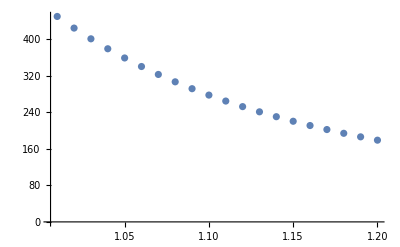

```mathematica
ListPlot[%1292]
```